```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
Get["MergerTransport/Merger2DProton.m"]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
Table[i,{i,12,12.2,0.001}]
```

{12.,12.001,12.002,12.003,12.004,12.005,12.006,12.007,12.008,12.009,12.01,12.011,12.012,12.013,12.014,12.015,12.016,12.017,12.018,12.019,12.02,12.021,12.022,12.023,12.024,12.025,12.026,12.027,12.028,12.029,12.03,12.031,12.032,12.033,12.034,12.035,12.036,12.037,12.038,12.039,12.04,12.041,12.042,12.043,12.044,12.045,12.046,12.047,12.048,12.049,12.05,12.051,12.052,12.053,12.054,12.055,12.056,12.057,12.058,12.059,12.06,12.061,12.062,12.063,12.064,12.065,12.066,12.067,12.068,12.069,12.07,12.071,12.072,12.073,12.074,12.075,12.076,12.077,12.078,12.079,12.08,12.081,12.082,12.083,12.084,12.085,12.086,12.087,12.088,12.089,12.09,12.091,12.092,12.093,12.094,12.095,12.096,12.097,12.098,12.099,12.1,12.101,12.102,12.103,12.104,12.105,12.106,12.107,12.108,12.109,12.11,12.111,12.112,12.113,12.114,12.115,12.116,12.117,12.118,12.119,12.12,12.121,12.122,12.123,12.124,12.125,12.126,12.127,12.128,12.129,12.13,12.131,12.132,12.133,12.134,12.135,12.136,12.137,12.138,12.139,12.14,12.141,12.142,12.143,12.144,12.145,12.146,12.147,12.148,12.149,12.15,12.151,12.152,12.153,12.154,12.155,12.156,12.157,12.158,12.159,12.16,12.161,12.162,12.163,12.164,12.165,12.166,12.167,12.168,12.169,12.17,12.171,12.172,12.173,12.174,12.175,12.176,12.177,12.178,12.179,12.18,12.181,12.182,12.183,12.184,12.185,12.186,12.187,12.188,12.189,12.19,12.191,12.192,12.193,12.194,12.195,12.196,12.197,12.198,12.199,12.2}

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

### show single core timing

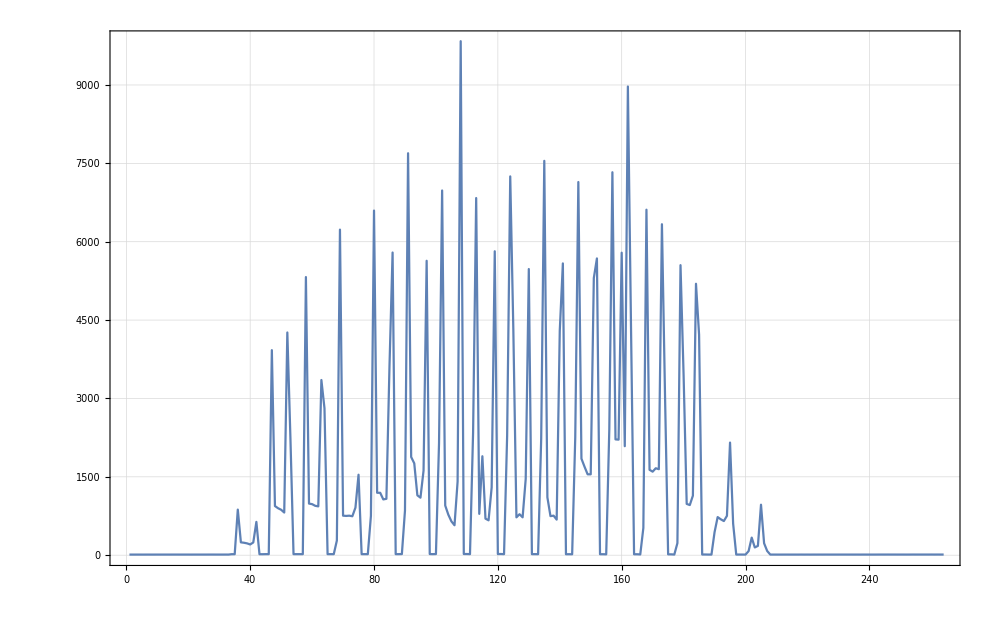

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

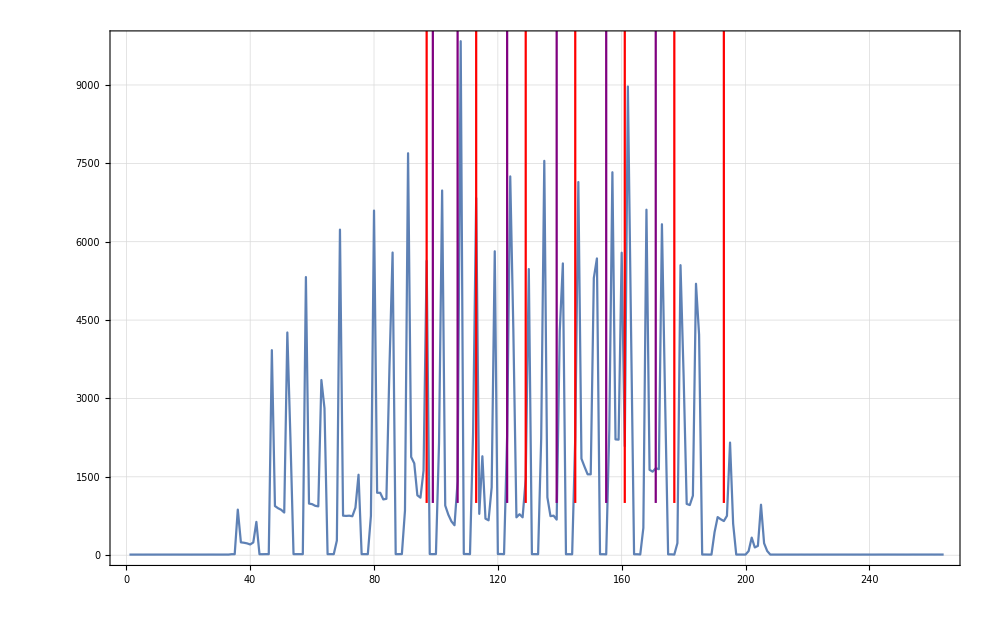

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
(xStart-xEnd)/24
```

-0.001875

```mathematica
158/220.
```

0.718182

```mathematica
158+62
```

220

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.757116
```

0.757116

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
Clear[BinCenters]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
xStart=-0.06999999999999999;
xEnd=0.045;
yStart=1.0540019999999999-R;
yEnd=0.9440019999999999-R;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinBoundariesYHalf[[1]]
```

{{-0.07,-0.065},{0.286884,0.296884}}

```mathematica
XYBinCentersYHalf[[1]]
```

{0.0209375,-0.026818}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

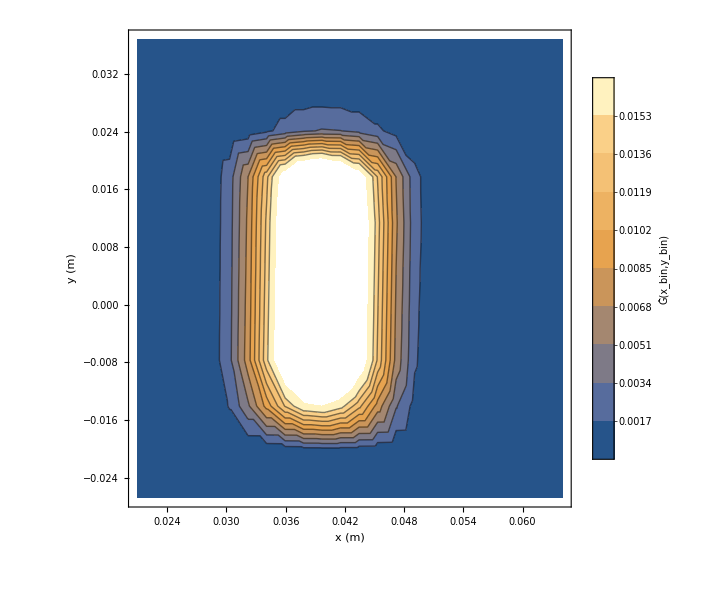

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

```mathematica
0.01*0.035
```

0.00035

```mathematica
0.02*0.05
```

0.001

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a1050/"];
```

```mathematica
d0SubFileNamesa1050P=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_da0_a1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_179-264.txt}

```mathematica
d0Spectruma1050P=Flatten[Table[Import[d0SubFileNamesa1050P[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050P]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d1050PSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]/Total[d0Spectruma1050P[[All,2]]]}]];
```

# dalpha, k=97.07

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1050/"];
```

```mathematica
dAlphaSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_179-264.txt}

```mathematica
dAlphaSpectruma0=Flatten[Table[Import[dAlphaSubFileNamesa0[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1040/"];
```

```mathematica
dAlphaSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_179-264.txt}

```mathematica
dAlphaSpectruma1040=Flatten[Table[Import[dAlphaSubFileNamesa1040[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1045/"];
```

```mathematica
dAlphaSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_179-264.txt}

```mathematica
dAlphaSpectruma1045=Flatten[Table[Import[dAlphaSubFileNamesa1045[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1045]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1055/"];
```

```mathematica
dAlphaSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_179-264.txt}

```mathematica
dAlphaSpectruma1055=Flatten[Table[Import[dAlphaSubFileNamesa1055[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1055]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1060/"];
```

```mathematica
dAlphaSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectruma1060=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesa1060,1];
```

```mathematica
dAlphaSpectruma1060[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000114515,0.000184805,0.000179744,0.000174875,0.000170191,0.000165646,0.000010631,0.,0.,0.,0.,0.00208322,0.00335448,0.00326392,0.00317675,0.00309282,0.00299578,0.000207217,0.,0.,0.,0.,0.00929392,0.0149753,0.0145837,0.0142061,0.0138419,0.0132834,0.00105432,0.,0.,0.,7.85747×10^-6,0.0241814,0.0390404,0.0380869,0.0371627,0.0362673,0.0344372,0.00311712,0.,0.,0.,0.0000994742,0.0461065,0.0749538,0.073444,0.0719523,0.0704979,0.0663773,0.00696375,0.,0.,0.,0.000359707,0.0695109,0.114023,0.112425,0.110812,0.109204,0.102377,0.0118254,0.,0.,0.,0.000644083,0.086333,0.142981,0.141995,0.140934,0.139836,0.131063,0.016007,0.,0.,0.,0.000818567,0.0897408,0.149729,0.1496,0.149415,0.149195,0.139876,0.0179104,0.,0.,0.,0.000872587,0.0811859,0.136282,0.136895,0.137409,0.137896,0.129115,0.0173718,0.,0.,0.,0.000845437,0.0628334,0.106529,0.10785,0.109074,0.110264,0.103298,0.0146209,0.,0.,0.,0.000667292,0.0393762,0.06762,0.0693104,0.0709273,0.0725289,0.068283,0.0101124,0.,0.,0.,0.000346991,0.0180153,0.0314942,0.0329486,0.0343894,0.035846,0.0341913,0.00540924,0.,0.,0.,0.0000759947,0.00552551,0.00980404,0.0104646,0.0111522,0.0118759,0.0114018,0.0019883,0.,0.,0.,2.96194×10^-6,0.00121318,0.00217354,0.00237672,0.00259275,0.00282247,0.00277463,0.000475478,0.,0.,0.,0.,0.000116968,0.000221071,0.000258751,0.000300942,0.000348035,0.000369349,0.0000579729,0.,0.,0.,0.,8.80772×10^-7,2.11344×10^-6,3.21047×10^-6,4.59463×10^-6,6.53823×10^-6,8.64622×10^-6,1.15482×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,xStart,xEnd},{y,yStart,yEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200032,-0.029995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

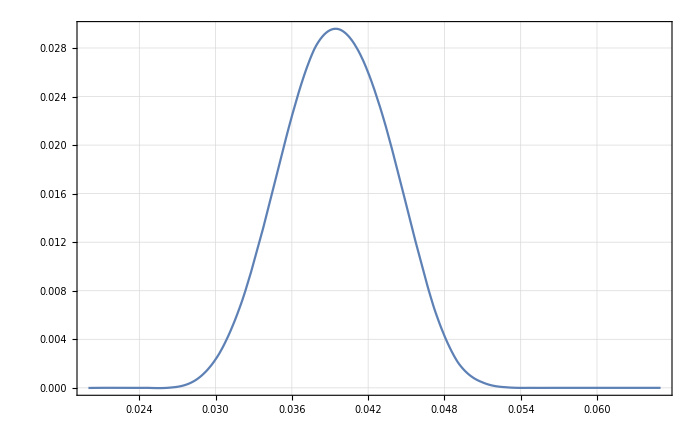

```mathematica
Plot[RefSpectrumInter[x,0.],{x,xStart,xEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

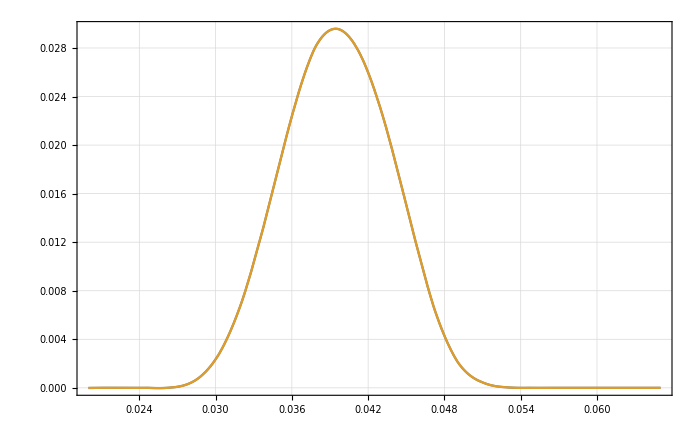

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,xStart,xEnd},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

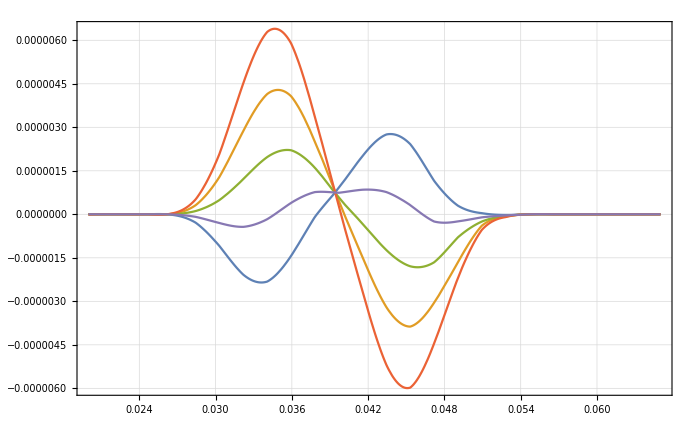

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,xStart,xEnd},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dAlphaSpectruma1040[[All,2]]//Length
```

362

```mathematica
dAlphaSpectruma1055[[All,2]]//Length
```

264

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

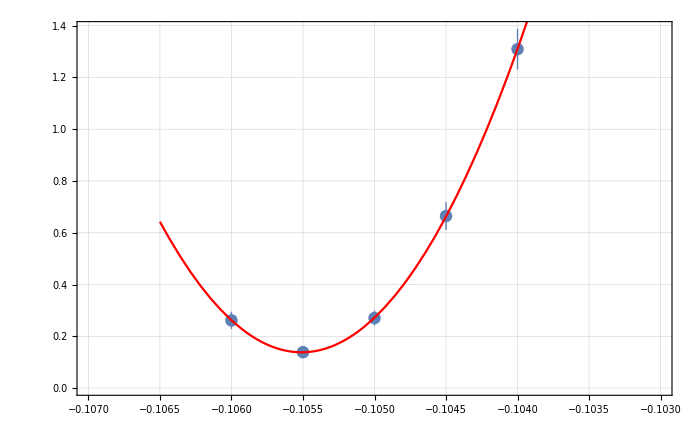
{{{1.30928×10^-9,6.64616×10^-10,2.70495×10^-10,1.38769×10^-10,2.61511×10^-10},{7.86811×10^-11,5.31884×10^-11,2.90487×10^-11,1.67193×10^-11,3.31935×10^-11}},a0 =  | -0.10551
FittedModel[1.38332×10^-10+0.000514142 (0.10551+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10551 | 0.0000414574 | -2545.01 | 1.5439×10^-7
scale | 0.000514142 | 0.000043962 | 11.6952 | 0.00723196
yoffset | 1.38332×10^-10 | 1.41633×10^-11 | 9.76692 | 0.010321 | 
 | DF | SS | MS
Model | 3 | 650.7 | 216.9
Error | 2 | 0.00474935 | 0.00237467
Uncorrected Total | 5 | 650.705 | 
Corrected Total | 4 | 286.56 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
(-0.1055096205659537+0.105)/-0.105
```

0.00485353

```mathematica
0.004853529199559075*1/(5*10^-5)
```

97.0706

```mathematica
0.1*10^-3*97.07
```

0.009707

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
AlphaInvest[[2,1,1,2]]
```

-0.10551

```mathematica
(AlphaInvest[[2,1,1,2]]+0.105)/(-0.105)/(5*10^-5)
```

97.0706

```mathematica
0.004853529199559075/(5*10^-5)
```

97.0706

# drF, k=4.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1050/"];
```

```mathematica
drFSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drF_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_179-264.txt}

```mathematica
drFSpectruma0=Flatten[Table[Import[drFSubFileNamesa0[[i]],"Table"],{i,1,Length[drFSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1040/"];
```

```mathematica
drFSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_179-264.txt}

```mathematica
drFSpectruma1040=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1040,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1045/"];
```

```mathematica
drFSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1045=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1045,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1055/"];
```

```mathematica
drFSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_drF_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_179-264.txt}

```mathematica
drFSpectruma1055=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

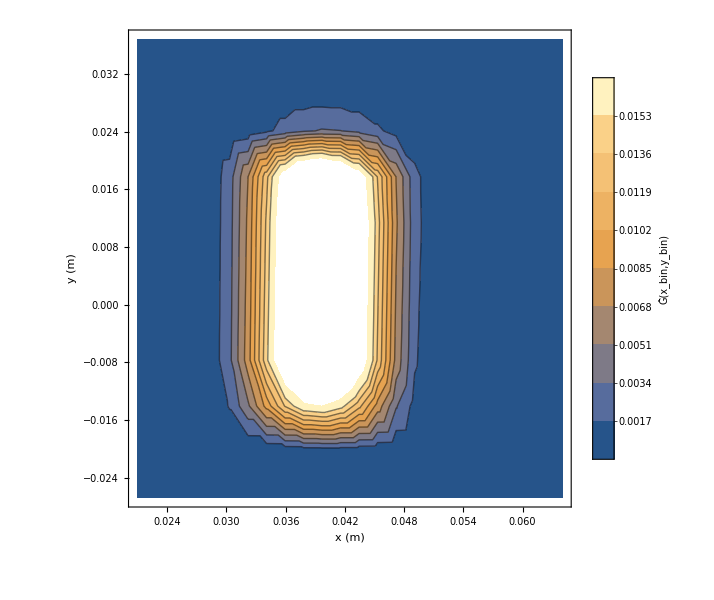

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1060/"];
```

```mathematica
drFSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drFSpectruma1060=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1060,1];
```

```mathematica
drFSpectruma1055[[All,2]]//Length
```

264

```mathematica
drFSpectruma1060[[All,2]]//Length
```

256

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47425×10^-7,6.02744×10^-7,5.91973×10^-7,5.81468×10^-7,5.71224×10^-7,5.61233×10^-7,5.51489×10^-7,5.41986×10^-7,5.32718×10^-7,4.75389×10^-8,0.,0.0000879969,0.000119268,0.000117147,0.000115078,0.000113059,0.000111091,0.00010917,0.000107297,0.00010543,0.0000104977,0.,0.000701745,0.000952878,0.00093608,0.000919691,0.000903701,0.000888099,0.000872877,0.000858025,0.000839179,0.0000834952,3.5836×10^-6,0.00239433,0.00325997,0.00320344,0.00314825,0.00309437,0.00304178,0.00299043,0.00294031,0.00284975,0.000327453,0.000037155,0.00559804,0.00767238,0.00754283,0.00741622,0.0072925,0.00717161,0.00705348,0.00693807,0.00664837,0.000848306,0.000165113,0.0105384,0.0145972,0.0143612,0.0141301,0.0139039,0.0136825,0.0134658,0.0132537,0.0125429,0.00178018,0.000466438,0.0171219,0.0240336,0.0236801,0.0233297,0.022985,0.0226459,0.0223126,0.021985,0.0205558,0.00321438,0.00096978,0.0246906,0.0351399,0.0347259,0.0342925,0.0338625,0.0334367,0.0330126,0.0325974,0.0301499,0.00514795,0.00159149,0.0322596,0.0464223,0.0460451,0.0455901,0.0451366,0.0446842,0.0442341,0.0437851,0.0401522,0.0544281,0.0540196,0.0492595,0.00942923,0.00266363,0.0428271,0.0626197,0.0626168,0.0623765,0.0621288,0.0618731,0.0616107,0.0613375,0.05573,0.011033,0.00295451,0.0436845,0.0643068,0.0645062,0.0644428,0.06436,0.0642704,0.064177,0.0640722,0.0580227,0.0118582,0.00307535,0.0419021,0.0620969,0.0624748,0.062525,0.0625699,0.0626116,0.062647,0.0626745,0.0564962,0.0119396,0.00302753,0.0378254,0.056474,0.0569931,0.0571759,0.0573524,0.0575234,0.057676,0.0578325,0.0519097,0.0113495,0.00278236,0.0317647,0.0478165,0.0484712,0.0487879,0.0490987,0.0494035,0.049702,0.0499907,0.0446863,0.010074,0.00232516,0.0244053,0.0370302,0.0377635,0.0381813,0.0385945,0.0390033,0.0394075,0.0398029,0.0354729,0.00833864,0.00171419,0.0167922,0.0256606,0.0263695,0.0268248,0.0272801,0.0277306,0.0281806,0.0286239,0.0254997,0.00619068,0.00108409,0.0098629,0.015269,0.015852,0.0162725,0.0166946,0.0171238,0.0175441,0.0179669,0.0160051,0.00404876,0.000562323,0.00473851,0.00745261,0.00782324,0.00811736,0.00841886,0.00872724,0.00904185,0.00936082,0.00832003,0.00225943,0.000226292,0.00197739,0.00313934,0.00331034,0.00345557,0.00360644,0.00376261,0.00392418,0.0040914,0.00361137,0.00103357,0.0000710994,0.000718059,0.00114017,0.00121167,0.00127949,0.00135001,0.00142319,0.00149911,0.00157783,0.00141378,0.000393956,0.0000121256,0.000189393,0.000301593,0.000326884,0.000353033,0.000380663,0.000409764,0.000440381,0.000472558,0.000439617,0.00011556,4.52877×10^-7,0.0000258848,0.0000418482,0.0000476277,0.0000539891,0.0000609723,0.000068562,0.0000768318,0.0000858192,0.0000850529,0.0000185858,0.,6.46386×10^-7,1.16186×10^-6,1.71743×10^-6,2.60735×10^-6,2.55523×10^-6,3.22825×10^-6,4.01108×10^-6,5.00119×10^-6,5.74377×10^-6,1.0528×10^-6}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250021,-0.0199964} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
drFSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]]}]];
```

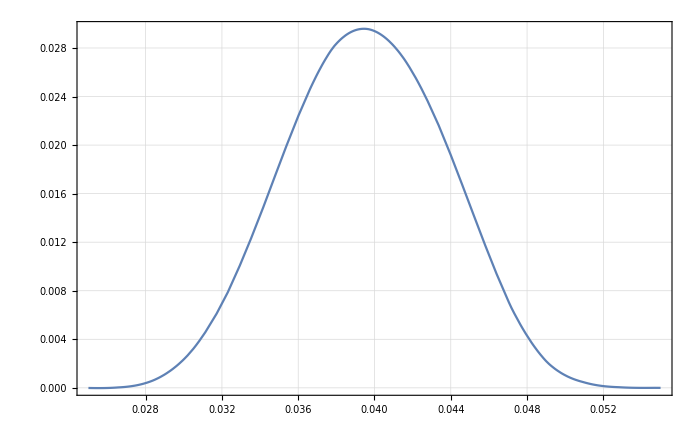

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drFSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]]}]];
drFSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]]}]];
drFSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}]];
```

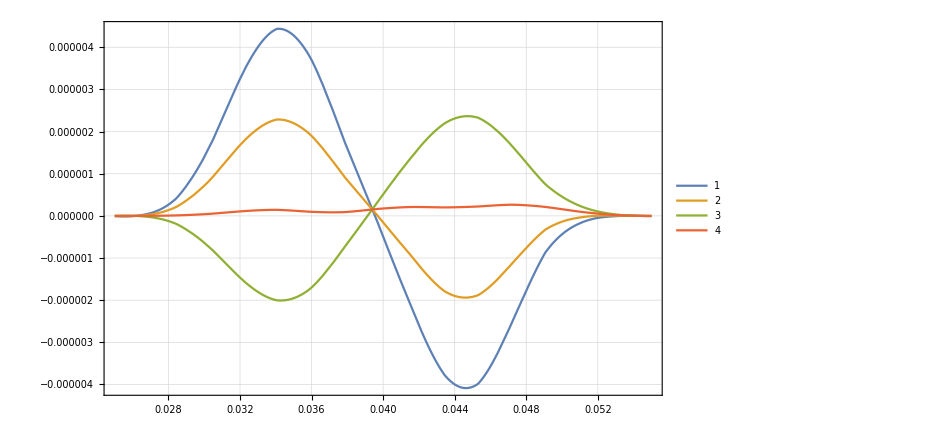

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drFSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rFDataList={drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]],drFSpectruma1060[[All,2]]/Total[drFSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

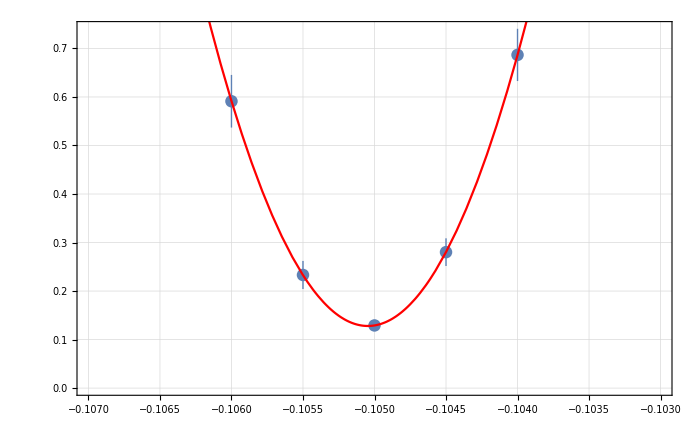
{{{6.86703×10^-10,2.80175×10^-10,1.29136×10^-10,2.33128×10^-10,5.91184×10^-10},{5.38263×10^-11,2.85119×10^-11,1.12789×10^-11,2.89544×10^-11,5.42352×10^-11}},a0 =  | -0.105047
FittedModel[1.28043×10^-10+0.000509836 (0.105047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105047 | 0.0000275451 | -3813.62 | 6.87583×10^-8
scale | 0.000509836 | 0.0000382191 | 13.3398 | 0.0055726
yoffset | 1.28043×10^-10 | 1.06022×10^-11 | 12.077 | 0.00678645 | 
 | DF | SS | MS
Model | 3 | 574.056 | 191.352
Error | 2 | 0.000169658 | 0.0000848291
Uncorrected Total | 5 | 574.056 | 
Corrected Total | 4 | 181.206 |  | ,-Graphics-}

```mathematica
rFInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rFDataList,bList, 4]
```

```mathematica
(rFInvest[[2,1,1,2]]+0.105)/-0.105
```

0.000442949

```mathematica
0.000442948920583481/(10^-4)
```

4.42949

# drA, k=157.04

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/"];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/Cluster_Try"];
```

```mathematica
drASubFileNamesa1040Cluster=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040Cluster=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040Cluster,1];
```

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

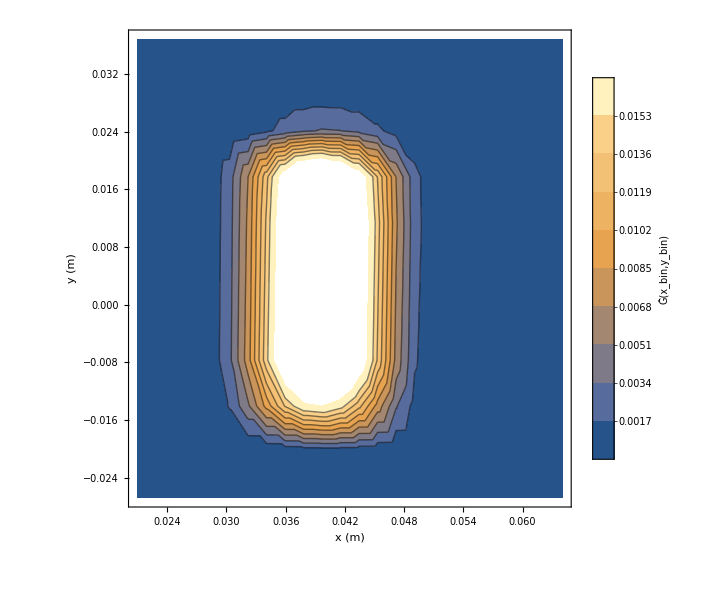

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

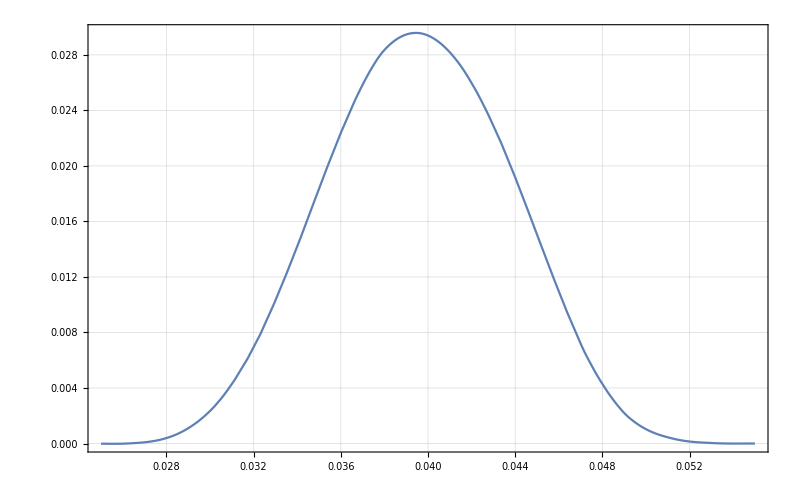

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drASpectruma1040InterCluster=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040Cluster[[All,2]]/Total[drASpectruma1040Cluster[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

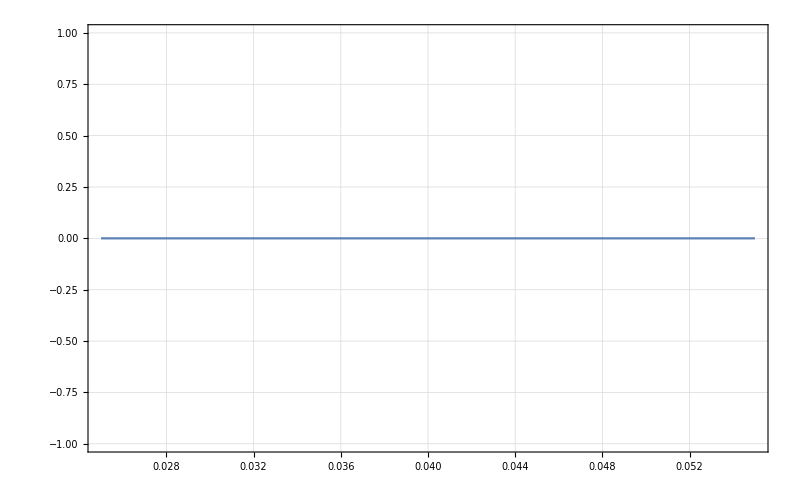

```mathematica
Plot[drASpectruma1040Inter[x,0.]-drASpectruma1040InterCluster[x,0.],{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
1.97*10^-3
```

0.00197

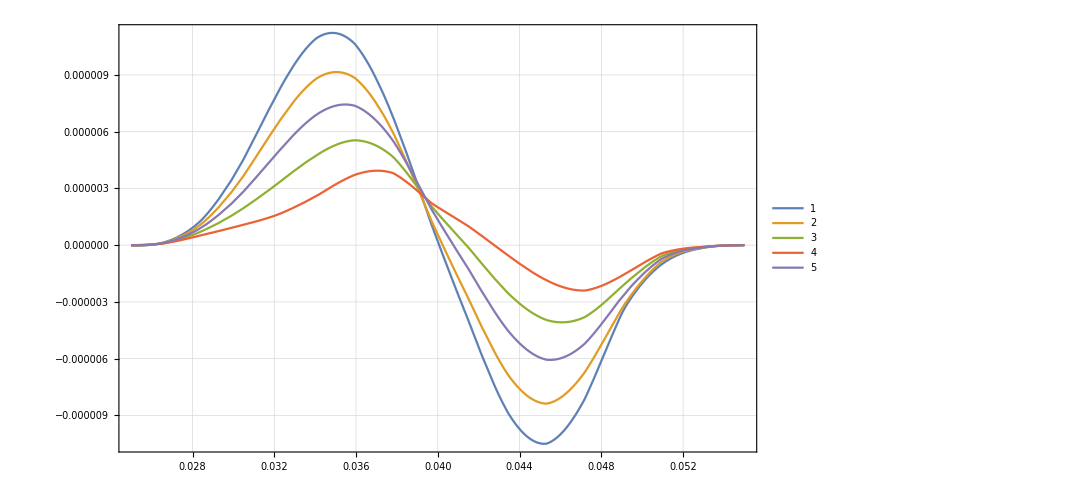

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1065/"];
```

```mathematica
drASubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1065=Flatten[Import[#,"Table"]&/@drASubFileNamesa1065,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1070/"];
```

```mathematica
drASubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1070=Flatten[Import[#,"Table"]&/@drASubFileNamesa1070,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1075/"];
```

```mathematica
drASubFileNamesa1075=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1075_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1075=Flatten[Import[#,"Table"]&/@drASubFileNamesa1075,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1075[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList2={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1065[[All,2]]/Total[drASpectruma1065[[All,2]]],drASpectruma1070[[All,2]]/Total[drASpectruma1070[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1075}

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107,-0.1075}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

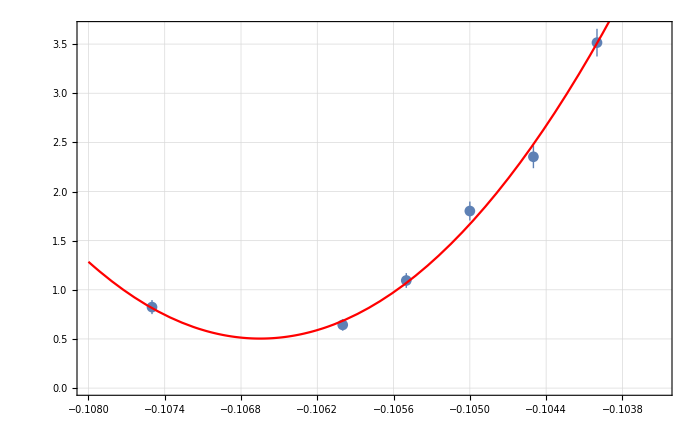
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[5.03778×10^-10+0.000428131 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000571871 | -1864.91 | 3.40012×10^-10
scale | 0.000428131 | 0.0000281651 | 15.2008 | 0.00061823
yoffset | 5.03778×10^-10 | 4.57292×10^-11 | 11.0166 | 0.00160176 | 
 | DF | SS | MS
Model | 3 | 1842.46 | 614.155
Error | 3 | 3.75941 | 1.25314
Uncorrected Total | 6 | 1846.22 | 
Corrected Total | 5 | 527.277 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

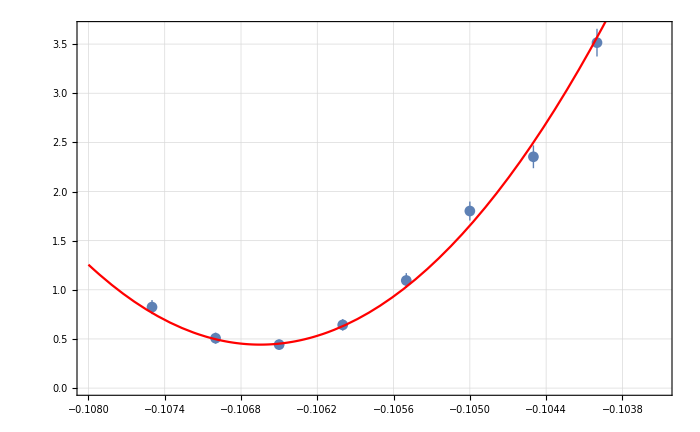
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,4.42288×10^-10,5.07741×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,5.08038×10^-11,5.64233×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[4.42288×10^-10+0.000445521 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000513687 | -2076.14 | 4.92061×10^-16
scale | 0.000445521 | 0.0000263228 | 16.9253 | 0.000013168
yoffset | 4.42288×10^-10 | 2.94575×10^-11 | 15.0145 | 0.0000237319 | 
 | DF | SS | MS
Model | 3 | 1997.37 | 665.79
Error | 5 | 5.62228 | 1.12446
Uncorrected Total | 8 | 2002.99 | 
Corrected Total | 7 | 744.691 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList,bList, 4]
```

```mathematica
((-0.10664865012298552+0.105)/-0.105)/(10^-4)
```

157.014

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

157.014

```mathematica
((-0.10664865012298552+0.105)/-0.105)/(10^-4)
```

157.014

# dB, k=69.93

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1050/"];
```

```mathematica
dBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_179-264.txt}

```mathematica
dBSpectruma0=Flatten[Table[Import[dBSubFileNamesa0[[i]],"Table"],{i,1,Length[dBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1040/"];
```

```mathematica
dBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_179-264.txt}

```mathematica
dBSpectruma1040=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1045/"];
```

```mathematica
dBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_179-264.txt}

```mathematica
dBSpectruma1045=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1055/"];
```

```mathematica
dBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_179-264.txt}

```mathematica
dBSpectruma1055=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

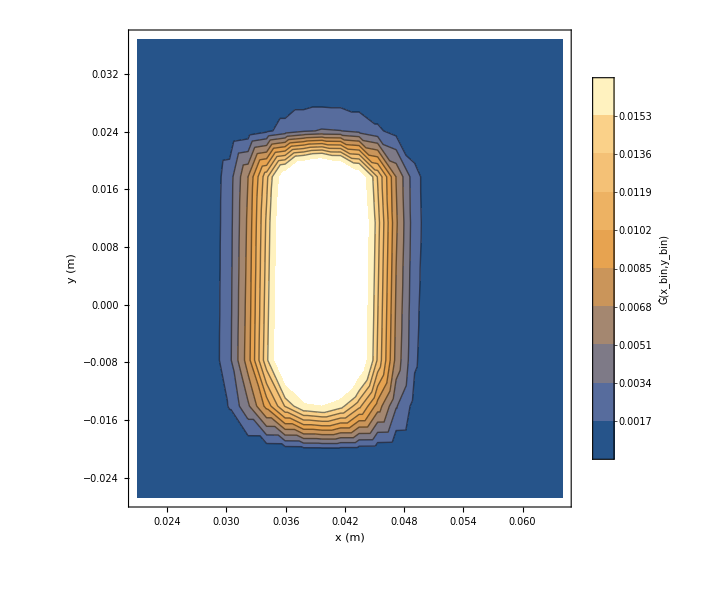

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1060/"];
```

```mathematica
dBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBSpectruma1060=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]]}]];
dBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]]}]];
dBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}]];
dBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]}]];
```

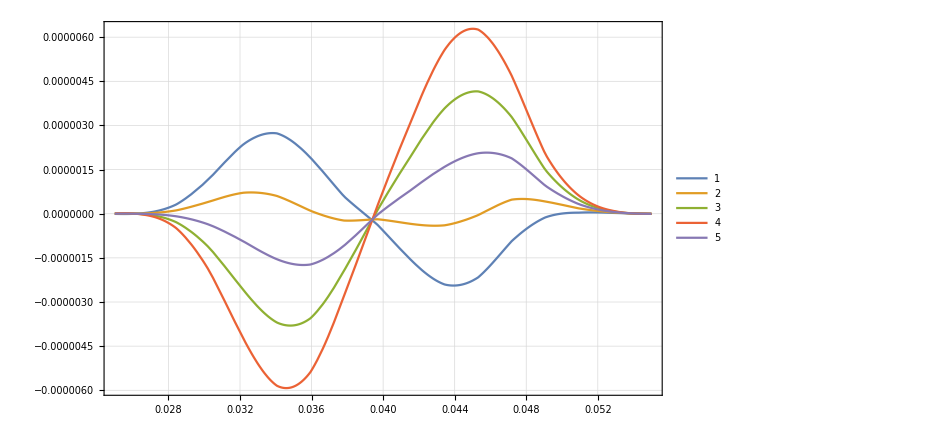

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

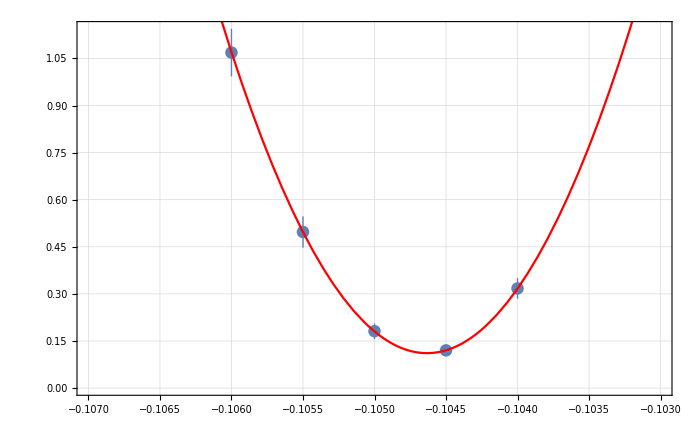
{{{3.17415×10^-10,1.20191×10^-10,1.81208×10^-10,4.97177×10^-10,1.06859×10^-9},{3.27248×10^-11,1.16634×10^-11,2.47023×10^-11,4.97713×10^-11,7.57612×10^-11}},a0 =  | -0.104633
FittedModel[1.11361×10^-10+0.000512848 (0.104633+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104633 | 0.00003187 | -3283.12 | 9.27742×10^-8
scale | 0.000512848 | 0.0000411871 | 12.4517 | 0.00638805
yoffset | 1.11361×10^-10 | 1.1474×10^-11 | 9.70545 | 0.0104501 | 
 | DF | SS | MS
Model | 3 | 552.813 | 184.271
Error | 2 | 0.00192816 | 0.000964081
Uncorrected Total | 5 | 552.815 | 
Corrected Total | 4 | 222.042 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
.106*6.930
```

0.73458

```mathematica
.75*.1
```

0.075

```mathematica
.15*69.93
```

10.4895

```mathematica
.15*69.93
```

10.4895

```mathematica
(BInvest[[2,1,1,2]]+0.105)/-0.105
```

-0.00349668

```mathematica
-0.003496680950444102/(5*10^-5)
```

-69.9336

```mathematica
.1*97.07
```

9.707

```mathematica
Sqrt[10.489500000000001^2+9.707^2]
```

14.2918

```mathematica
14*10^-3.
```

0.014

```mathematica
%*100
```

1.4

```mathematica
18*4
```

72

```mathematica
1/7.83
```

0.127714

# drRxB, k=43.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1050/"];
```

```mathematica
drRxBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_179-264.txt}

```mathematica
drRxBSpectruma0=Flatten[Table[Import[drRxBSubFileNamesa0[[i]],"Table"],{i,1,Length[drRxBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1040/"];
```

```mathematica
drRxBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_179-264.txt}

```mathematica
drRxBSpectruma1040=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1045/"];
```

```mathematica
drRxBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_179-264.txt}

```mathematica
drRxBSpectruma1045=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1055/"];
```

```mathematica
drRxBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_179-264.txt}

```mathematica
drRxBSpectruma1055=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

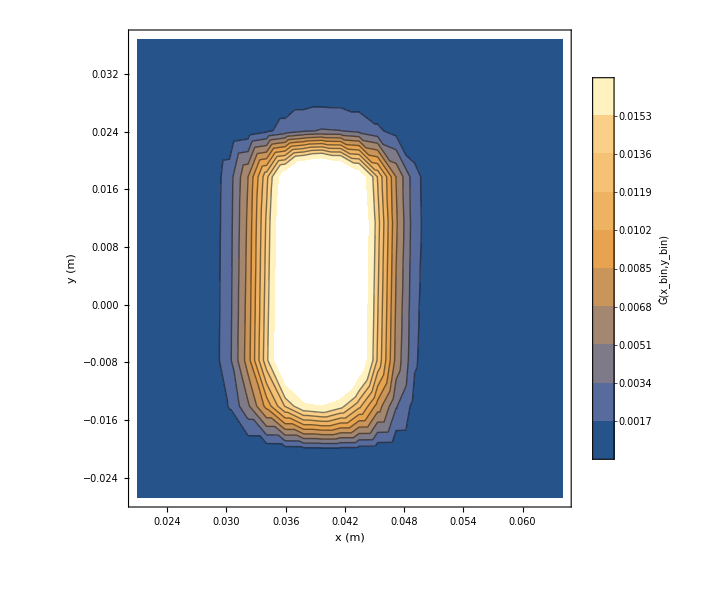

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1060/"];
```

```mathematica
drRxBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drRxBSpectruma1060=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drRxBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drRxBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]]}]];
drRxBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]]}]];
drRxBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}]];
drRxBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]}]];
```

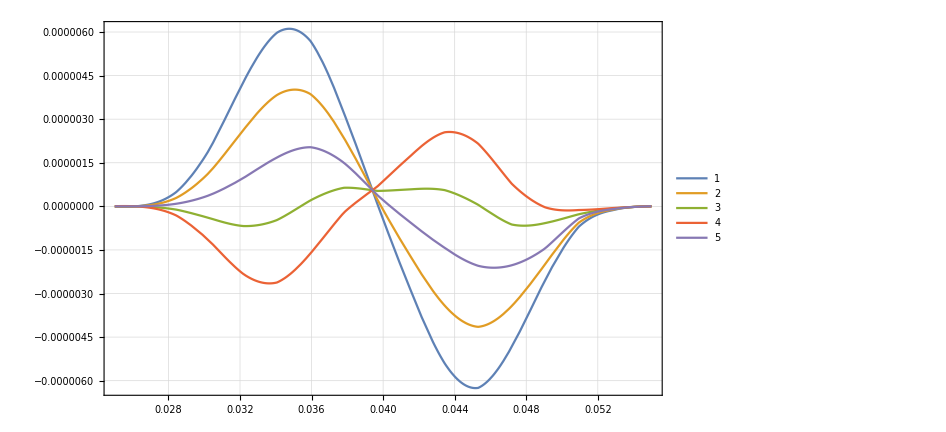

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drRxBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rRxBDataList={drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

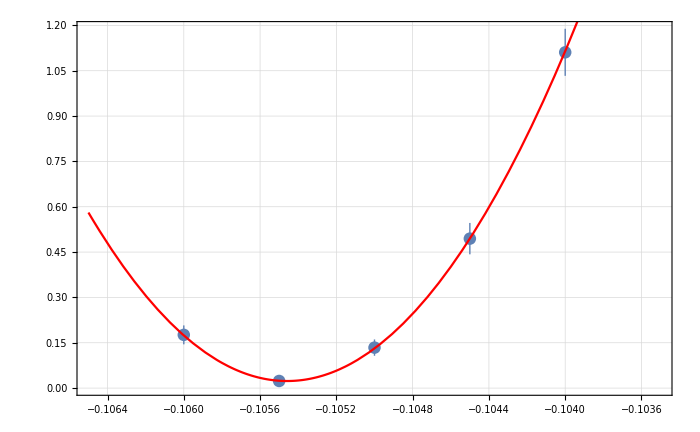
{{{1.11093×10^-9,4.94473×10^-10,1.33884×10^-10,2.35734×10^-11,1.76109×10^-10},{7.78298×10^-11,5.18879×10^-11,2.69823×10^-11,1.22177×10^-11,3.12751×10^-11}},a0 =  | -0.105458
FittedModel[2.34228×10^-11+0.000513376 (0.105458+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105458 | 0.000036153 | -2916.99 | 1.17525×10^-7
scale | 0.000513376 | 0.0000412367 | 12.4495 | 0.00639024
yoffset | 2.34228×10^-11 | 1.12144×10^-11 | 2.08863 | 0.171959 | 
 | DF | SS | MS
Model | 3 | 354.587 | 118.196
Error | 2 | 0.020374 | 0.010187
Uncorrected Total | 5 | 354.607 | 
Corrected Total | 4 | 272.567 |  | ,-Graphics-}

```mathematica
rRxBInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rRxBDataList,bList, 4]
```

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

43.6187

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

0.436187

# dG1, k=0.135

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1050/"];
```

```mathematica
dG1SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_179-264.txt}

```mathematica
dG1Spectruma0=Flatten[Table[Import[dG1SubFileNamesa0[[i]],"Table"],{i,1,Length[dG1SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1040/"];
```

```mathematica
dG1SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG1_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_179-264.txt}

```mathematica
dG1Spectruma1040=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1045/"];
```

```mathematica
dG1SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_179-264.txt}

```mathematica
dG1Spectruma1045=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1055/"];
```

```mathematica
dG1SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_179-264.txt}

```mathematica
dG1Spectruma1055=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

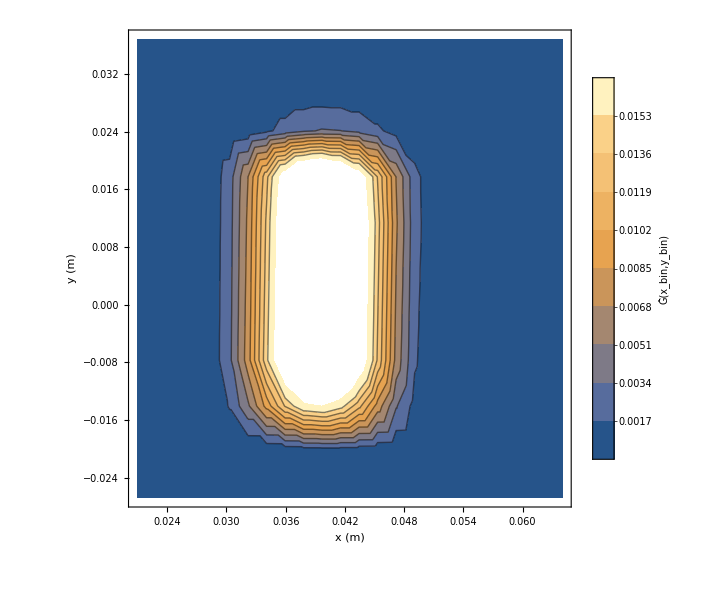

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1060/"];
```

```mathematica
dG1SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG1Spectruma1060=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG1Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG1Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]]}]];
dG1Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]]}]];
dG1Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}]];
dG1Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]}]];
```

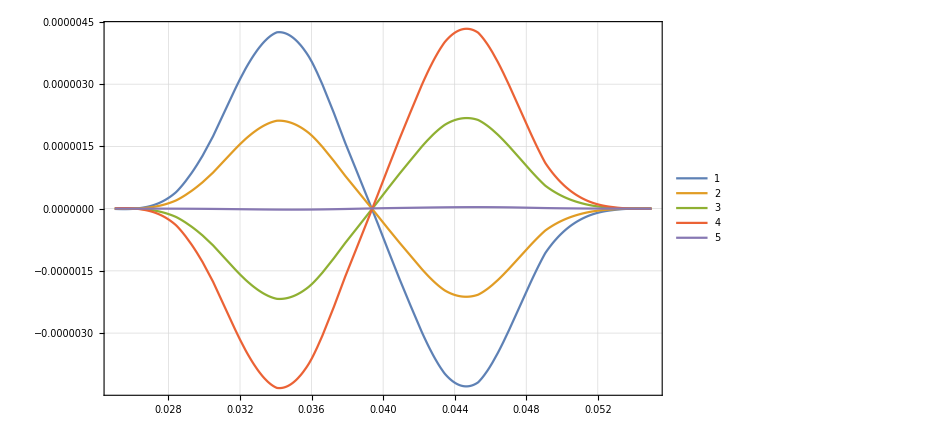

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG1Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

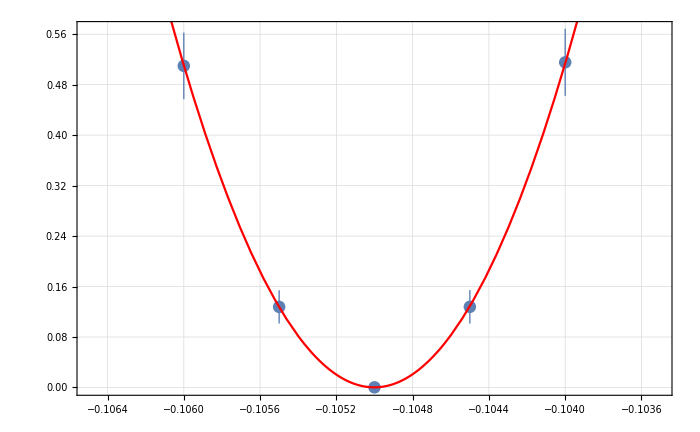
{{{5.15438×10^-10,1.2786×10^-10,2.17303×10^-13,1.2776×10^-10,5.09835×10^-10},{5.31564×10^-11,2.65551×10^-11,1.19504×10^-12,2.63586×10^-11,5.27491×10^-11}},a0 =  | -0.105001
FittedModel[2.15056×10^-13+0.000512007 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258456 | -4062.65 | 6.05873×10^-8
scale | 0.000512007 | 0.0000335399 | 15.2656 | 0.00426372
yoffset | 2.15056×10^-13 | 1.19452×10^-12 | 0.180036 | 0.873715 | 
 | DF | SS | MS
Model | 3 | 234.149 | 78.0496
Error | 2 | 0.00318623 | 0.00159312
Uncorrected Total | 5 | 234.152 | 
Corrected Total | 4 | 233.044 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((BInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.134947

# dG2, k=0.069

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1050/"];
```

```mathematica
dG2SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_179-264.txt}

```mathematica
dG2Spectruma0=Flatten[Table[Import[dG2SubFileNamesa0[[i]],"Table"],{i,1,Length[dG2SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1040/"];
```

```mathematica
dG2SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG2_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_179-264.txt}

```mathematica
dG2Spectruma1040=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1045/"];
```

```mathematica
dG2SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_179-264.txt}

```mathematica
dG2Spectruma1045=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1055/"];
```

```mathematica
dG2SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_179-264.txt}

```mathematica
dG2Spectruma1055=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»}] must be a valid array.

ListContourPlot[Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625},{-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822},0.197555 Symbol[]}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1060/"];
```

```mathematica
dG2SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG2Spectruma1060=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG2Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]]}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»}] does not contain a list of data and coordinates.

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG2Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]]}]];
dG2Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]]}]];
dG2Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}]];
dG2Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]}]];
```

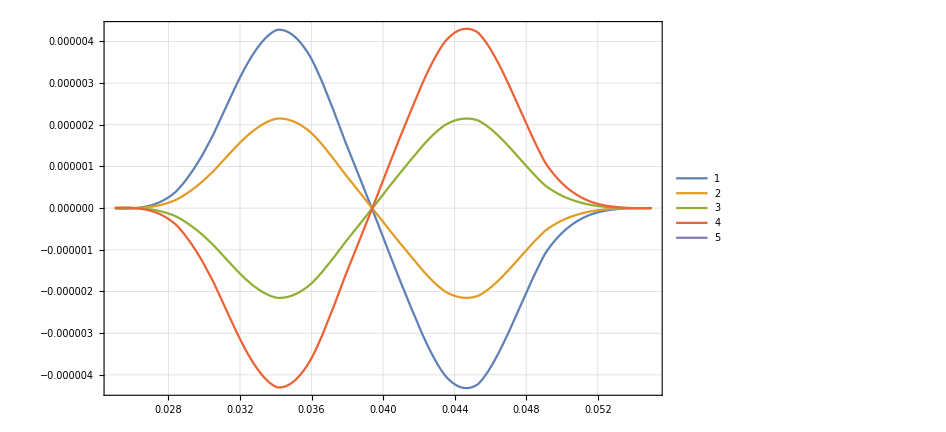

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG2Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
BDataList={dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]],dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

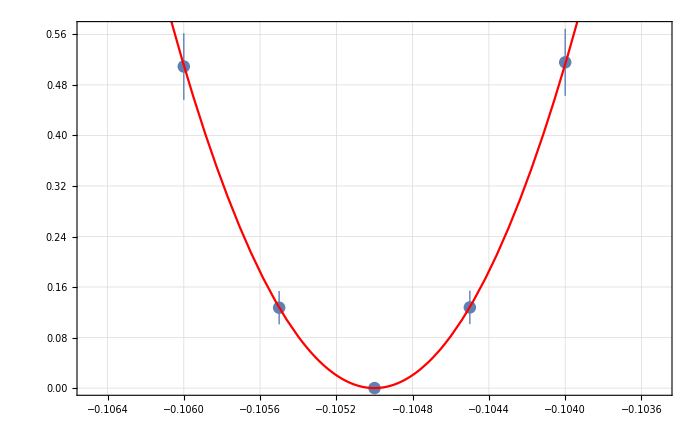
{{{5.15775×10^-10,1.27743×10^-10,2.5683×10^-17,1.27295×10^-10,5.09157×10^-10},{5.30913×10^-11,2.64645×10^-11,1.03735×10^-14,2.63815×10^-11,5.27903×10^-11}},a0 =  | -0.105001
FittedModel[5.79854×10^-24+0.000511976 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258279 | -4065.4 | 6.05054×10^-8
scale | 0.000511976 | 0.0000334707 | 15.2963 | 0.00424674
yoffset | 5.79854×10^-24 | 2.17491×10^-14 | 2.66611×10^-10 | 1. | 
 | DF | SS | MS
Model | 3 | 233.979 | 77.9929
Error | 2 | 0.00612162 | 0.00306081
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
g2Invest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((-0.10500072280654503+0.105)/-0.105)/(10^-4)
```

0.0688387

```mathematica
((g2Invest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.0688387

# drd, k=187.97

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drD_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_179-264.txt}

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1035/"];
```

```mathematica
drDSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_179-264.txt}

```mathematica
drDSpectruma1035=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1030/"];
```

```mathematica
drDSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_179-264.txt}

```mathematica
drDSpectruma1030=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1020/"];
```

```mathematica
drDSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_179-264.txt}

```mathematica
drDSpectruma1020=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_179-264.txt}

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

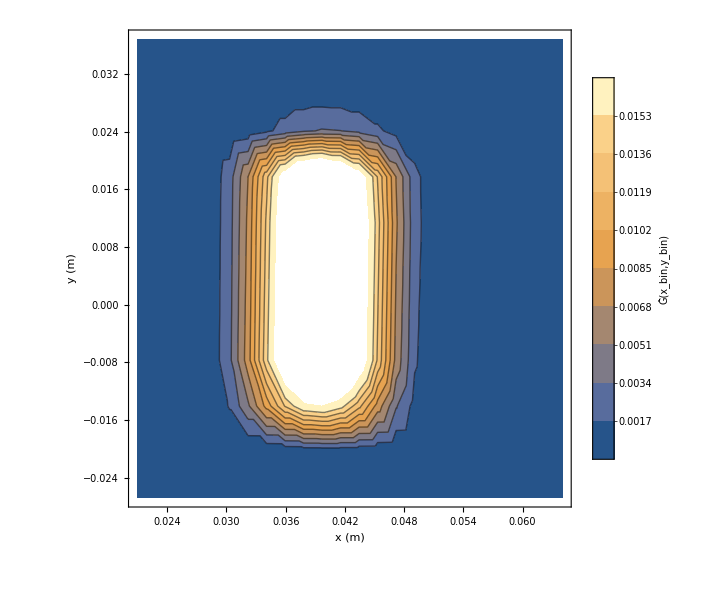

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

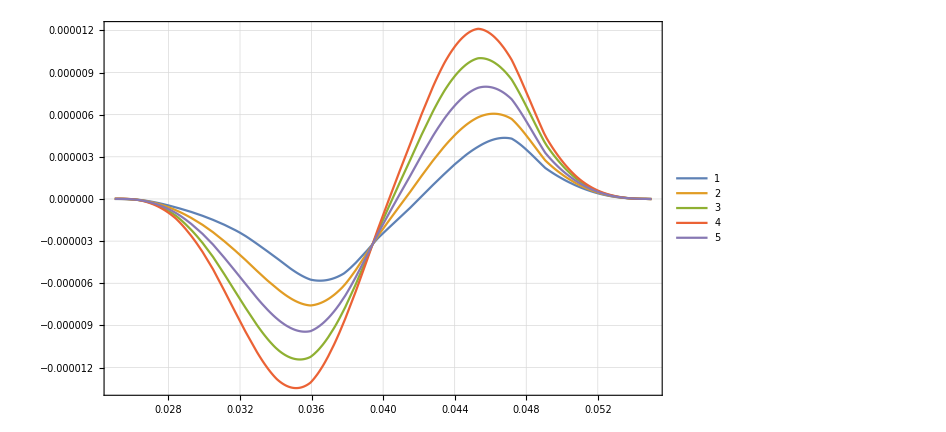

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rDDataList={drDSpectruma1020[[All,2]]/Total[drDSpectruma1020[[All,2]]],drDSpectruma1030[[All,2]]/Total[drDSpectruma1030[[All,2]]],drDSpectruma1035[[All,2]]/Total[drDSpectruma1035[[All,2]]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

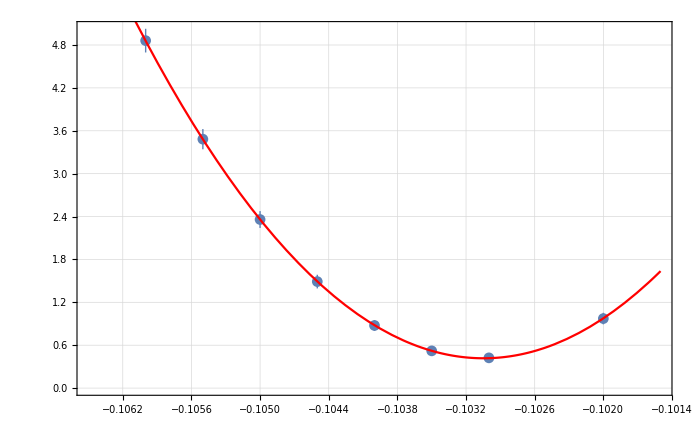
{{{9.72613×10^-10,4.23104×10^-10,5.2079×10^-10,8.75997×10^-10,1.49013×10^-9,2.35856×10^-9,3.4825×10^-9,4.86114×10^-9},{8.05613×10^-11,5.84884×10^-11,6.24937×10^-11,7.60636×10^-11,9.5516×10^-11,1.17637×10^-10,1.41231×10^-10,1.65669×10^-10}},a0 =  | -0.103047
FittedModel[4.17262×10^-10+0.000509271 (0.103047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103047 | 0.0000439952 | -2342.24 | 2.69246×10^-16
scale | 0.000509271 | 0.0000227131 | 22.4219 | 3.27895×10^-6
yoffset | 4.17262×10^-10 | 3.55904×10^-11 | 11.724 | 0.0000793702 | 
 | DF | SS | MS
Model | 3 | 2514.53 | 838.177
Error | 5 | 0.0114451 | 0.00228902
Uncorrected Total | 8 | 2514.54 | 
Corrected Total | 7 | 1161.97 |  | ,-Graphics-}

```mathematica
rDInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rDDataList,bList, 4]
```

```mathematica
(-0.10304725773676074+0.105)/-0.105
```

-0.0185975

```mathematica
-0.018597545364183402/10^-4
```

-185.975

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-185.975

# dXAShift, k=57.14/1.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1020/"];
```

```mathematica
dXAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_179-264.txt}

```mathematica
dXAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1030/"];
```

```mathematica
dXAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_179-264.txt}

```mathematica
dXAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1035/"];
```

```mathematica
dXAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_179-264.txt}

```mathematica
dXAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

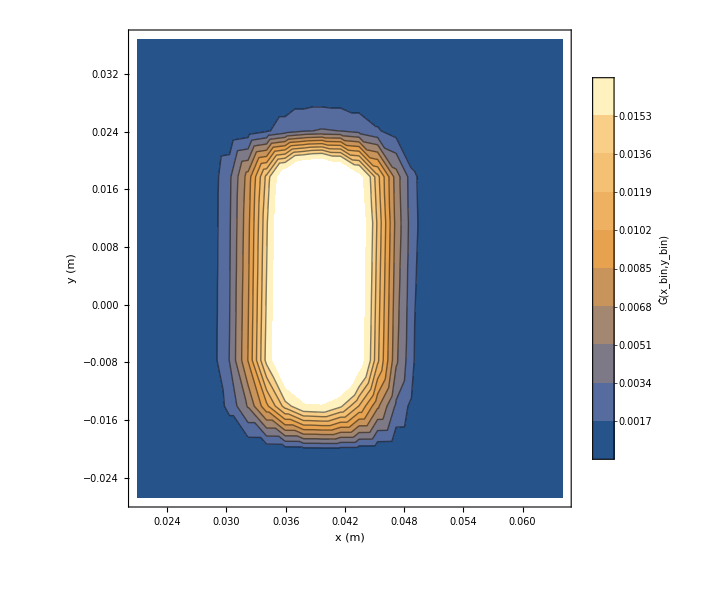

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

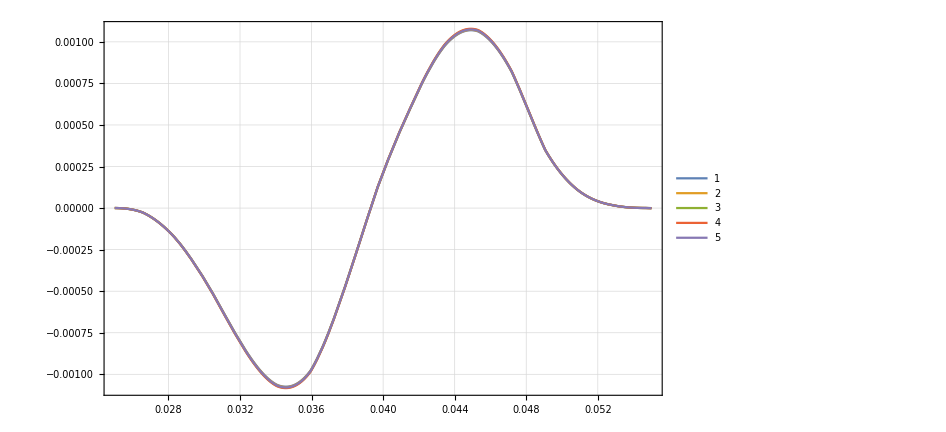

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

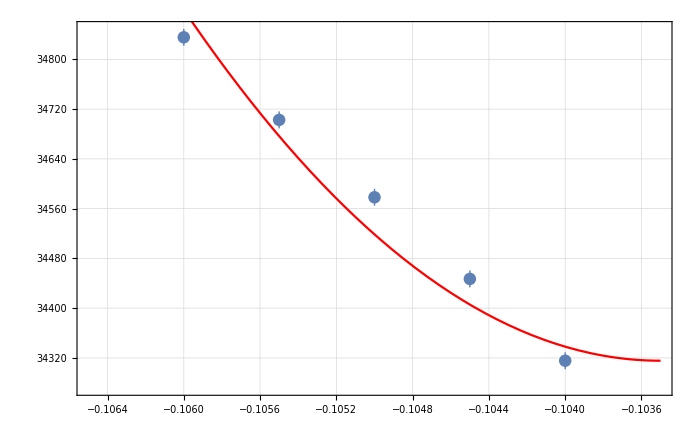
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

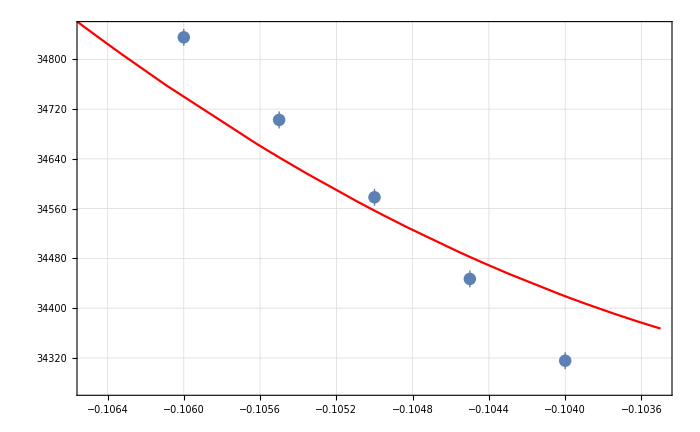
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.101429
FittedModel[0.000034271+0.022403 (0.101429+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101429 | 0.00233567 | -43.4259 | 0.000529855
scale | 0.022403 | 0.0146073 | 1.53369 | 0.264839
yoffset | 0.000034271 | 1.816×10^-7 | 188.717 | 0.0000280776 | 
 | DF | SS | MS
Model | 3 | 3.20163×10^7 | 1.06721×10^7
Error | 2 | 135.795 | 67.8977
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
Export["MergerTransport/NC_opt_drF/b"<>ToString[IntegerPart[a*10000]]<>"/TransferResult_08-09-20_NC_opt_C_BSOn_drF_b"<>ToString[IntegerPart[a*10000]]<>"_"<>ToString[Bins[[1]]]<>"-"<>ToString[Bins[[2]]]<>".txt",BinwYShiftPrec44OriginalBinsb0NewBGrad,"Table"];
```

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYAShift, k=136.91

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1050/"];
```

```mathematica
dYAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_179-264.txt}

```mathematica
dYAShiftSpectruma0=Flatten[Table[Import[dYAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1035/"];
```

```mathematica
dYAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_179-264.txt}

```mathematica
dYAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1030/"];
```

```mathematica
dYAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_179-264.txt}

```mathematica
dYAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1020/"];
```

```mathematica
dYAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_179-264.txt}

```mathematica
dYAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1040/"];
```

```mathematica
dYAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_179-264.txt}

```mathematica
dYAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1045/"];
```

```mathematica
dYAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_179-264.txt}

```mathematica
dYAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1055/"];
```

```mathematica
dYAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_179-264.txt}

```mathematica
dYAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

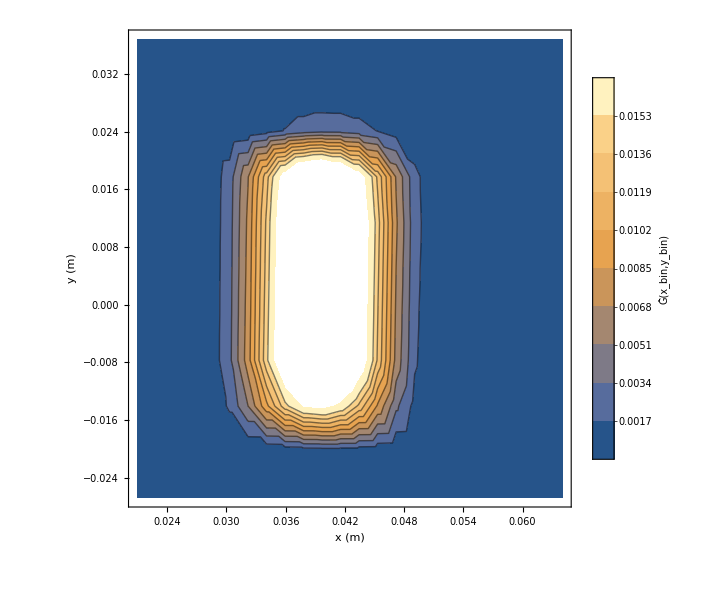

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1060/"];
```

```mathematica
dYAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]]}]];
dYAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]]}]];
dYAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}]];
dYAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]}]];
dYAShiftSpectruma1030Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]]}]];
dYAShiftSpectruma1035Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]]}]];
dYAShiftSpectruma1020Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]]}]];
```

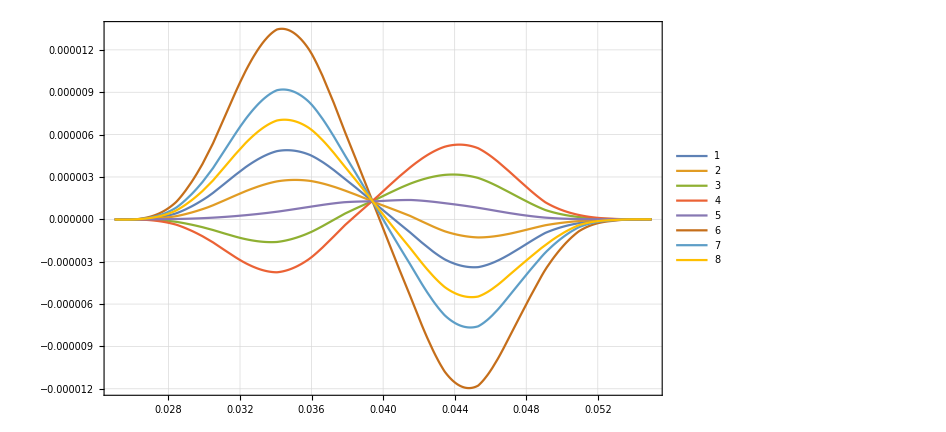

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma0Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1020Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1030Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1035Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
YAShiftDataList={dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

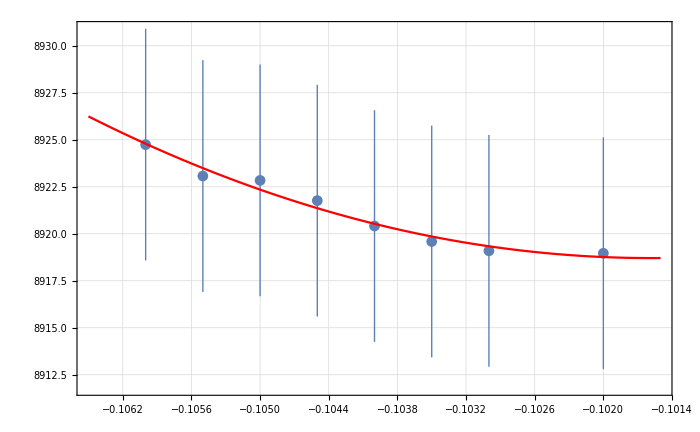
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101581
FittedModel[8.91871×10^-6+0.000311423 (0.101581+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101581 | 0.0115715 | -8.77857 | 0.000318144
scale | 0.000311423 | 0.00142201 | 0.219001 | 0.835308
yoffset | 8.91871×10^-6 | 8.1098×10^-9 | 1099.74 | 1.17989×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0200687 | 0.00401374
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

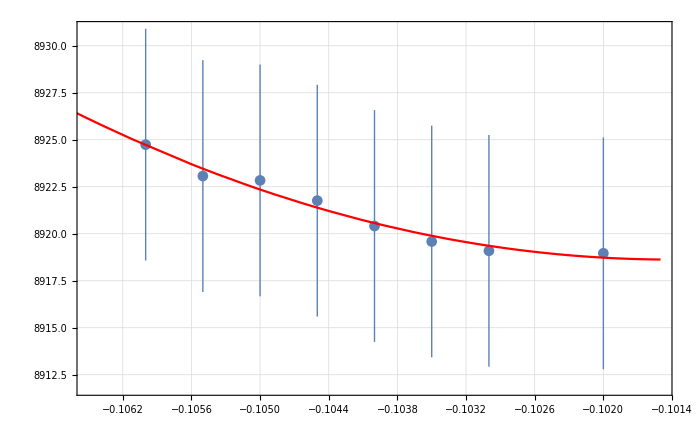
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101406
FittedModel[8.91863×10^-6+0.000288483 (0.101406+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101406 | 0.0133294 | -7.60771 | 0.000623477
scale | 0.000288483 | 0.00142201 | 0.20287 | 0.847234
yoffset | 8.91863×10^-6 | 9.29081×10^-9 | 959.94 | 2.32851×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0202751 | 0.00405502
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

```mathematica
((-0.10158085291422538+0.105)/-0.105)/(0.00025)
```

-130.253

```mathematica
((-0.10140601633241499+0.105)/-0.105)/(0.00025)
```

-136.914

```mathematica
-130.25322231522367*0.0001
```

-0.0130253

# dXAShift2D, k=1.62

### a=-0.105

#### a=-0.105(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1050m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1050m15=Flatten[Table[Import[dXAShiftSubFileNamesa1050m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_5/"];
```

```mathematica
dXAShiftSubFileNamesa1050p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_179-264.txt}

```mathematica
dXAShiftSpectruma1050p5=Flatten[Table[Import[dXAShiftSubFileNamesa1050p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1050m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1050m5=Flatten[Table[Import[dXAShiftSubFileNamesa1050m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_15/"];
```

```mathematica
dXAShiftSubFileNamesa1050p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_179-264.txt}

```mathematica
dXAShiftSpectruma1050p15=Flatten[Table[Import[dXAShiftSubFileNamesa1050p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.104

#### a=-0.104(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Table[Import[dXAShiftSubFileNamesa1040[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1040m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1040m15=Flatten[Table[Import[dXAShiftSubFileNamesa1040m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1040m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1040m5=Flatten[Table[Import[dXAShiftSubFileNamesa1040m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_5/"];
```

```mathematica
dXAShiftSubFileNamesa1040p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_179-264.txt}

```mathematica
dXAShiftSpectruma1040p5=Flatten[Table[Import[dXAShiftSubFileNamesa1040p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_15/"];
```

```mathematica
dXAShiftSubFileNamesa1040p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_179-264.txt}

```mathematica
dXAShiftSpectruma1040p15=Flatten[Table[Import[dXAShiftSubFileNamesa1040p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1045

#### a=-0.1045(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Table[Import[dXAShiftSubFileNamesa1045[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1045m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1045m15=Flatten[Table[Import[dXAShiftSubFileNamesa1045m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_5/"];
```

```mathematica
dXAShiftSubFileNamesa1045p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_179-264.txt}

```mathematica
dXAShiftSpectruma1045p5=Flatten[Table[Import[dXAShiftSubFileNamesa1045p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1045m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1045m5=Flatten[Table[Import[dXAShiftSubFileNamesa1045m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_15/"];
```

```mathematica
dXAShiftSubFileNamesa1045p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_179-264.txt}

```mathematica
dXAShiftSpectruma1045p15=Flatten[Table[Import[dXAShiftSubFileNamesa1045p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1055

#### a=-0.1055(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Table[Import[dXAShiftSubFileNamesa1055[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1055m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1055m15=Flatten[Table[Import[dXAShiftSubFileNamesa1055m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1055m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1055m5=Flatten[Table[Import[dXAShiftSubFileNamesa1055m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_5/"];
```

```mathematica
dXAShiftSubFileNamesa1055p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_179-264.txt}

```mathematica
dXAShiftSpectruma1055p5=Flatten[Table[Import[dXAShiftSubFileNamesa1055p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_15/"];
```

```mathematica
dXAShiftSubFileNamesa1055p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_179-264.txt}

```mathematica
dXAShiftSpectruma1055p15=Flatten[Table[Import[dXAShiftSubFileNamesa1055p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1060

#### a=-0.1060(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

```mathematica
dXAShiftSpectruma1060=Flatten[Table[Import[dXAShiftSubFileNamesa1060[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1060m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1060m15=Flatten[Table[Import[dXAShiftSubFileNamesa1060m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_5/"];
```

```mathematica
dXAShiftSubFileNamesa1060p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_179-264.txt}

```mathematica
dXAShiftSpectruma1060p5=Flatten[Table[Import[dXAShiftSubFileNamesa1060p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1060m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1060m5=Flatten[Table[Import[dXAShiftSubFileNamesa1060m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m5]}],1];
```

```mathematica
dXAShiftSpectruma1050m5[[All,2]]//Length
```

264

```mathematica
dXAShiftSpectruma1060m5[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_15/"];
```

```mathematica
?FileSorter
```

```mathematica
dXAShiftSubFileNamesa1060p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_179-264.txt}

```mathematica
dXAShiftSpectruma1060p15=Flatten[Table[Import[dXAShiftSubFileNamesa1060p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0250006,0.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

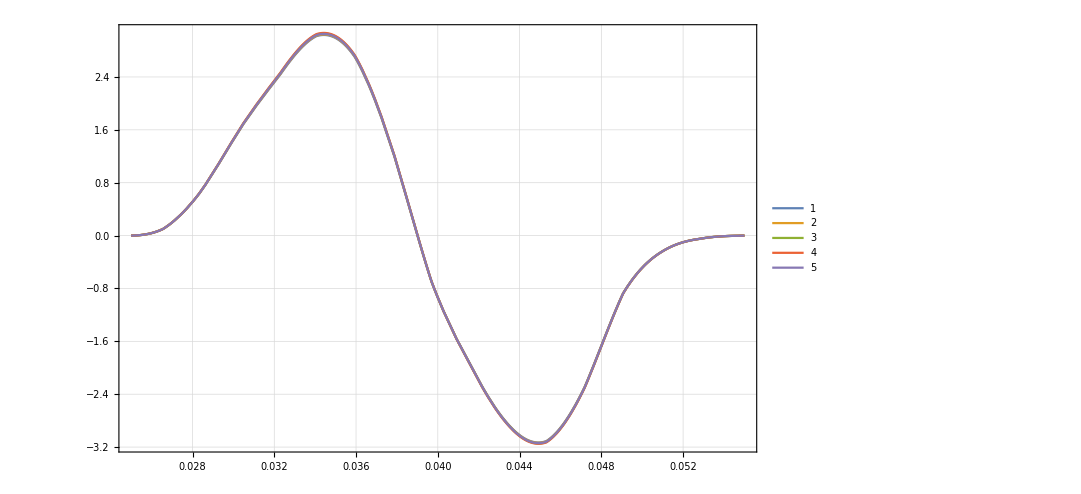

```mathematica
Plot[{
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1040Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1045Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1055Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1060Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma0Inter[x,0.23]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList2D={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}

```mathematica
bList2D2={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
XAShiftDataList2D2={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]]}
};
```

```mathematica
XAShiftDataList2D={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}
};
```

```mathematica
RefNorm=RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]];
```

```mathematica
Length[RefNorm]
```

264

```mathematica
Dimensions[XAShiftDataList2D]
```

{5,5,264}

```mathematica
Length[XAShiftDataList2D[[1,1]]]
```

264

```mathematica
Length[bList2D[[2]]]
```

5

```mathematica
Table[XAShiftDataList2D⟦b,par⟧//Length,{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}]
```

{{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264}}

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2],{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2],{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
Chi2List2D
```

{{0.0000126211,1.43994×10^-6,1.33175×10^-6,0.0000122879,0.0000343155},{0.0000125412,1.41195×10^-6,1.3578×10^-6,0.0000123668,0.000034447},{0.0000124614,1.38544×10^-6,1.38414×10^-6,0.0000124466,0.0000345783},{0.000012382,1.3591×10^-6,1.41072×10^-6,0.000012526,0.0000347027},{0.0000123005,1.33293×10^-6,1.43759×10^-6,0.0000126057,0.0000348354}}

```mathematica
plotChi2List2D=Table[{bList2D[[1,b]],bList2D[[2,par]],Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2]},{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
plotChi2List2D2=Table[{bList2D2[[1,b]],bList2D2[[2,par]],Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2]},{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D⟦b,para⟧^2)],{b,Length[bList2D[[1]]]},{para,Length[bList2D[[2]]]}];
```

```mathematica
dChi2List2=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D2⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D2⟦b,para⟧^2)],{b,Length[bList2D2[[1]]]},{para,Length[bList2D2[[2]]]}];
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[x_,x0_,y_,y0_,f_,g_,k_]:=k+f*(x-x0)^2+g*(y-y0)^2
```

```mathematica
0<-0.105<0
```

False

```mathematica
bList2D2
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
Min[bList2D2[[2]]]
```

-0.00015

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,Min[bList2D2[[2]]]<par0<Max[bList2D2[[2]]],-10000<ascale<10000,-1<pscale<1,0.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{offset,Min[Chi2List2D2]},{ascale,5},{pscale,5/10^4},{par0,Min[bList2D2[[2]]]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[2.69844×10^-10+0.0000666051 (0.105077+a)^2+553.45 (-2.83471×10^-8+par)^2]

```mathematica
Sqrt[1/1.4912926423138863*^-6]
```

818.877

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[bList2D[[2]]]<par0<Max[bList2D[[2]]],-1000<ascale<1000,-1<pscale<1,-1000.<offset≤Min[Chi2List2D]},{{a00,-0.105},{par0,Min[bList2D[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[-1.17551×10^-7+7.78385×10^-6 (0.105019+a)^2+574.865 (-8.74238×10^-7+par)^2]

```mathematica
fit2["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105077 | 0.00899365 | -11.6835 | 6.22366×10^-9
offset | 2.69844×10^-10 | 1.41277×10^-9 | 0.191003 | 0.851084
ascale | 122.531 | 1802.41 | 0.0679819 | 0.946698
pscale | 0.042507 | 5.24864×10^-6 | 8098.67 | 3.17057×10^-51
par0 | 2.83471×10^-8 | 1.10443×10^-8 | 2.56666 | 0.0214762

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105019 | 0.0738099 | -1.42282 | 0.170198
par0 | 8.74238×10^-7 | 1.01256×10^-8 | 86.3392 | 3.3192×10^-27
ascale | -358.429 | 7.63287×10^-9 | -4.69586×10^10 | 6.63748×10^-202
pscale | 0.0417078 | 3.25×10^-6 | 12833.2 | 1.22921×10^-70
offset | -1.17551×10^-7 | 9.44779×10^-10 | -124.422 | 2.25439×10^-30

```mathematica
bList2D2
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
bList2D
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}

```mathematica
Plot3D[0.+0.25373704917327977 (0.10504249683354637+a)^2+544.5543878217807 (4.1049735352606163*^-7+par)^2,{a,-0.106,-0.104},{par,-0.00015,0.00025}]
```

-Graphics3D-

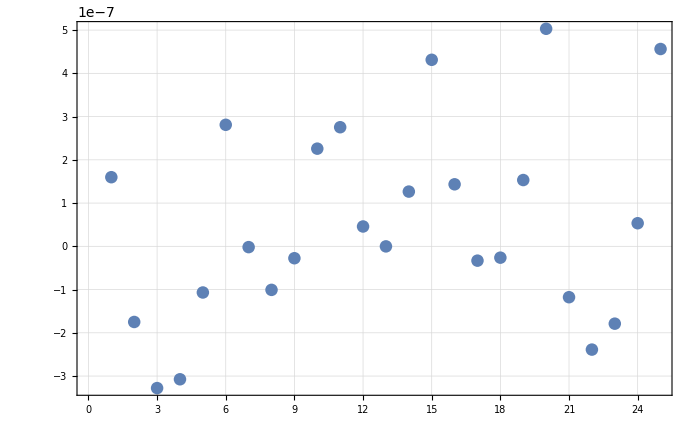

```mathematica
ListPlot[fit["FitResiduals"]]
```

```mathematica
(-0.10507706564034543+0.105)/-0.105
```

0.000733958

```mathematica
0.0007339584794802916/0.00025
```

2.93583

```mathematica
(-0.1050185201015299+0.105)/-0.105/0.00025
```

0.705528

```mathematica
2.9358339179211663*0.0001
```

0.000293583

```mathematica
0.005508159700042576/0.00025
```

22.0326

```mathematica
12.9*0.1
```

1.29

```mathematica
0.1*1.6189269922428111
```

0.161893

```mathematica
57*0.1
```

5.7

```mathematica
0.16*35
```

5.6

```mathematica
5.7/0.16
```

35.625

```mathematica
0.16
```

```mathematica
((-0.10504249683354637+0.105)/-0.105)/0.00025
```

1.61893

```mathematica
((-0.10617422685299294+0.105)/-0.105)/0.00025
```

44.7325

```mathematica
44*.1
```

4.4

```mathematica
0.00040473174806070276/0.00025
```

1.61893

```mathematica
0.00040473174806070276/0.00025*0.0001
```

0.000161893

```mathematica
a00/.fit["BestFitParameters"]
```

-0.105042

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105042 | 2.28751×10^-6 | -45920. | 1.03817×10^-81
par0 | -4.10497×10^-7 | 1.07627×10^-8 | -38.1409 | 3.7314×10^-20
ascale | -1.98522 | 0.00759741 | -261.302 | 8.17032×10^-37
pscale | 0.0428528 | 3.52509×10^-6 | 12156.5 | 3.63175×10^-70
offset | 0. | 1.35196×10^-9 | 0. | 1.

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D,1],PlotStyle->Blue],Plot3D[fit[a,par],{a,-0.104,-.106},{par,-0.00015,0.00025},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
z=
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYRxBShift, k=0.000029

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1050/"];
```

```mathematica
dYrxbShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_179-264.txt}

```mathematica
dYrxbShiftSpectruma0=Flatten[Table[Import[dYrxbShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYrxbShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1040/"];
```

```mathematica
dYrxbShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_179-264.txt}

```mathematica
dYrxbShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1045/"];
```

```mathematica
dYrxbShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_179-264.txt}

```mathematica
dYrxbShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1055/"];
```

```mathematica
dYrxbShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_179-264.txt}

```mathematica
dYrxbShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

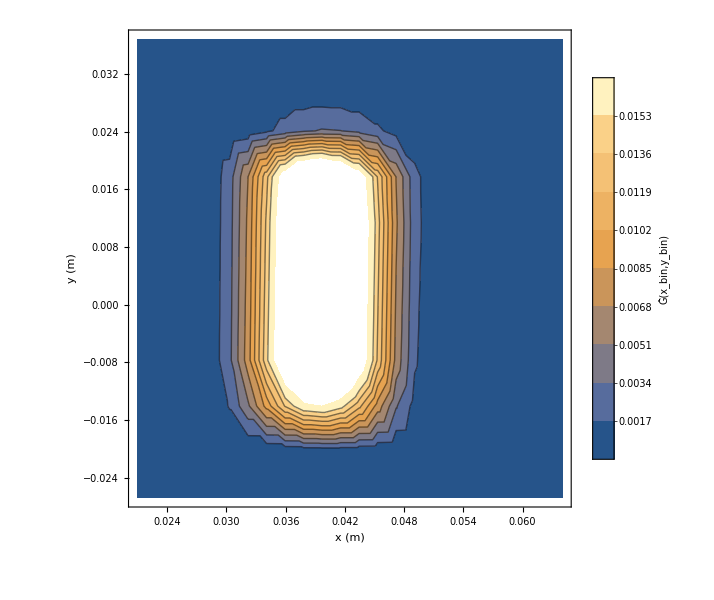

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1060/"];
```

```mathematica
dYrxbShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYrxbShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYrxbShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYrxbShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]]}]];
dYrxbShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]]}]];
dYrxbShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]]}]];
dYrxbShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]}]];
```

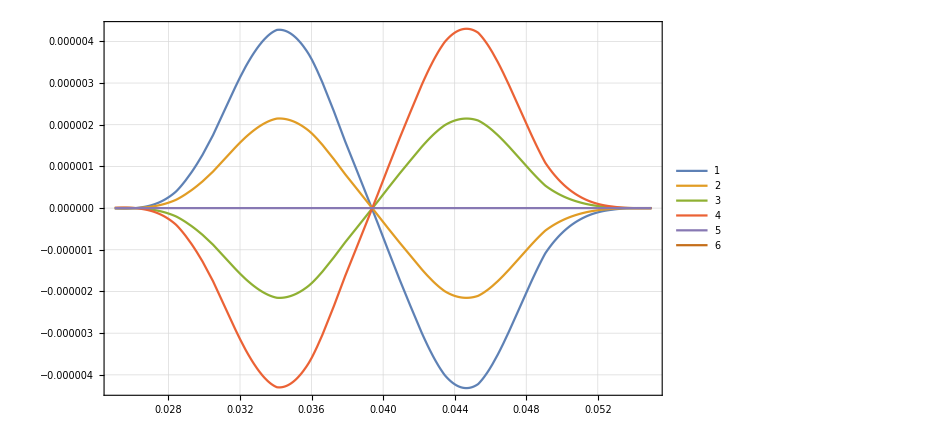

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYrxbShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYrxbShiftDataList={dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
RefNorm=Total[RefSpectrum[[All,2]]];
```

```mathematica
RefNormed=RefSpectrum[[All,2]]/RefNorm;
```

```mathematica
Sigma=(If[#1==0,10000,10^-4 #1]&)/@RefNormed;
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@dYrxbShiftDataList;
```

```mathematica
Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-4 √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bList]}];errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.106<b0<-0.104&&-100<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[5.68265×10^-34+0.000511307 (0.105+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 9.90204×10^-37 | -1.06039×10^35 | 0.
scale | 0.000511307 | 8.34241×10^-45 | 6.12901×10^40 | 0.
yoffset | 5.68265×10^-34 | 1.11487×10^-22 | 5.09714×10^-12 | 1.

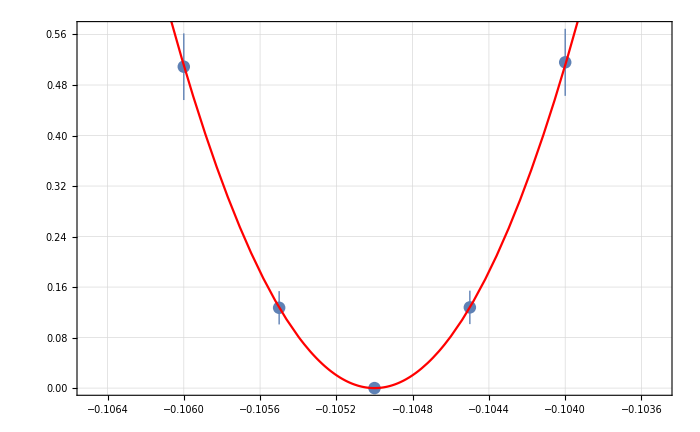

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1065,-0.1035},Automatic}],Plot[10^9 fitresult[b],{b,-0.1065,-0.1035},PlotStyle->Red]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

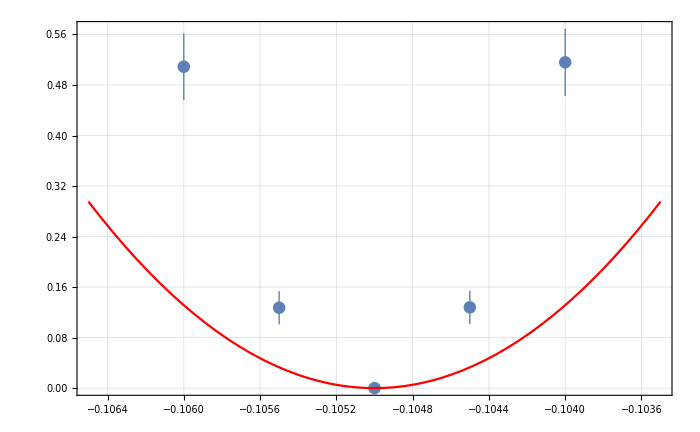
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.37355×10^-34+0.000131292 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 4.08459×10^-36 | -2.57064×10^34 | 0.
scale | 0.000131292 | 2.18009×10^-42 | 6.02231×10^37 | 0.
yoffset | 1.37355×10^-34 | 1.11487×10^-22 | 1.23203×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 104.616 | 34.8719
Error | 2 | 129.37 | 64.6848
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

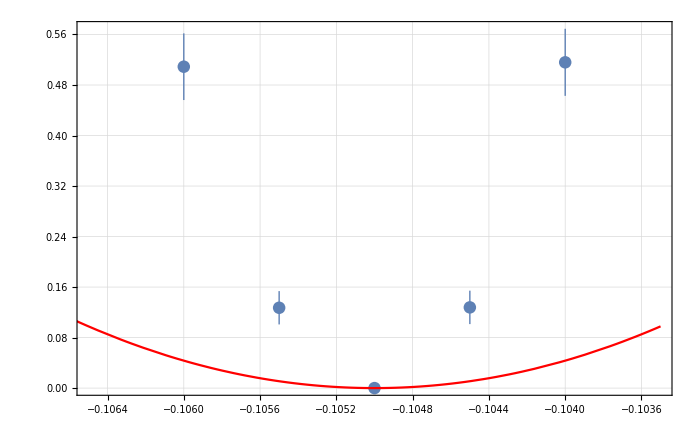
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.0522×10^-33+0.000043454 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 7.42653×10^-36 | -1.41385×10^34 | 0.
scale | 0.000043454 | 6.53648×10^-41 | 6.64791×10^35 | 0.
yoffset | 1.0522×10^-33 | 1.11487×10^-22 | 9.4379×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 37.98 | 12.66
Error | 2 | 196.005 | 98.0027
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.10500000076570207+0.105)/-0.105)/(0.00025)
```

0.0000291696

```mathematica
((-0.10500000000865034+0.105)/-0.105)/(0.00025)
```

3.29537×10^-7

# dNk2x, k=11.22

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1050/"];
```

```mathematica
dNk2xSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_179-264.txt}

```mathematica
dNk2xSpectruma0=Flatten[Table[Import[dNk2xSubFileNamesa0[[i]],"Table"],{i,1,Length[dNk2xSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1040/"];
```

```mathematica
dNk2xSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_179-264.txt}

```mathematica
dNk2xSpectruma1040=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1045/"];
```

```mathematica
dNk2xSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_179-264.txt}

```mathematica
dNk2xSpectruma1045=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1055/"];
```

```mathematica
dNk2xSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_179-264.txt}

```mathematica
dNk2xSpectruma1055=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

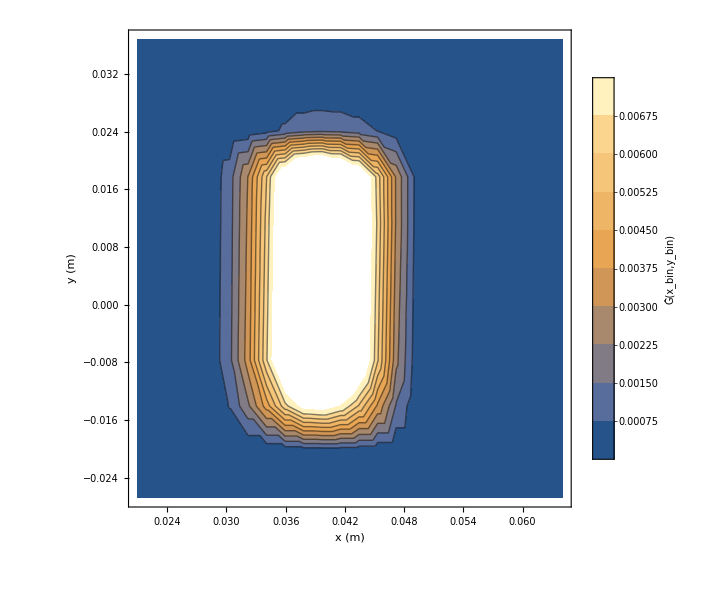

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1060/"];
```

```mathematica
dNk2xSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dNk2xSpectruma1060=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dNk2xSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dNk2xSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]]}]];
dNk2xSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]]}]];
dNk2xSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]]}]];
dNk2xSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]}]];
```

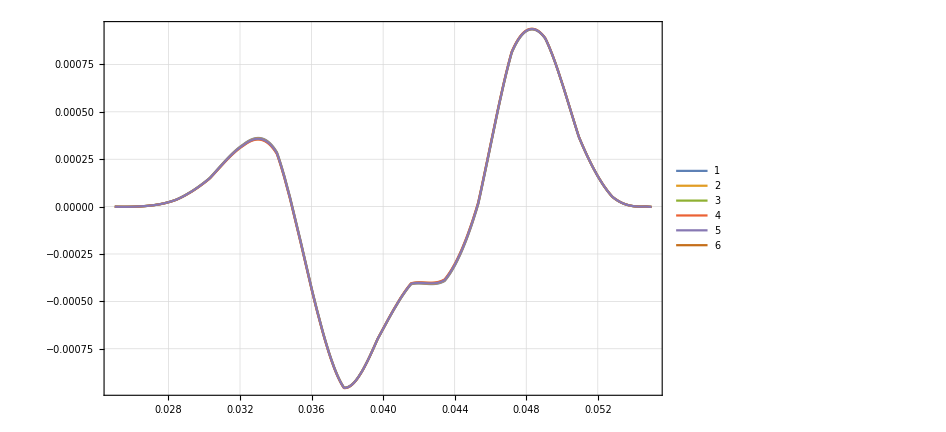

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dNk2xSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dNk2xDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dNk2xDataList={dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

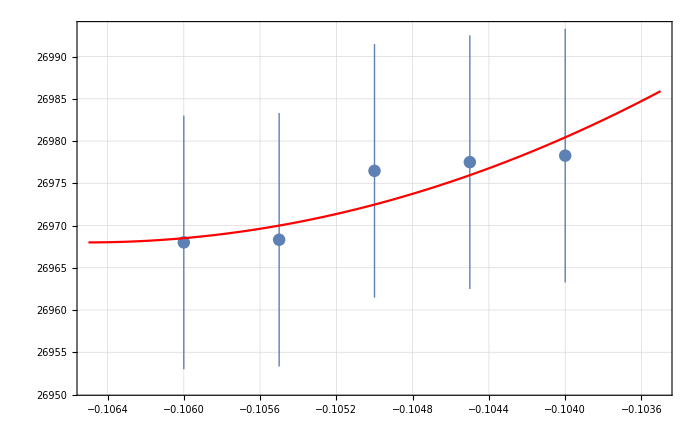
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.1065
FittedModel[0.000026968+0.00198904 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.0123342 | -8.6345 | 0.013149
scale | 0.00198904 | 0.0160472 | 0.123949 | 0.91269
yoffset | 0.000026968 | 3.21907×10^-8 | 837.759 | 1.42482×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.115597 | 0.0577983
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
(-0.1065+0.105)/-0.105/0.005
```

2.85714

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

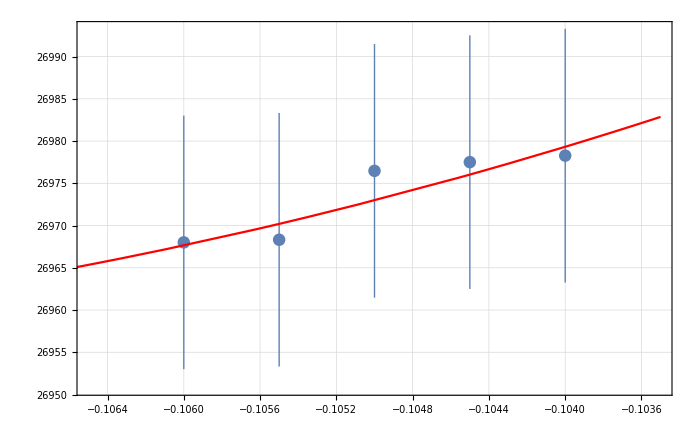
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.110893
FittedModel[0.0000269558+0.000495243 (0.110893+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.110893 | 0.191195 | -0.58 | 0.62055
scale | 0.000495243 | 0.0160472 | 0.0308616 | 0.978183
yoffset | 0.0000269558 | 5.5217×10^-7 | 48.8179 | 0.000419343 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.0845484 | 0.0422742
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.11089324097917469+0.105)/-0.105)/(0.005)
```

11.2252

```mathematica
0.2/1000
```

0.0002

# dXAoff, k=177.55/71.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1050/"];
```

```mathematica
dXAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_179-264.txt}

```mathematica
dXAoffSpectruma0=Flatten[Table[Import[dXAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1040/"];
```

```mathematica
dXAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_179-264.txt}

```mathematica
dXAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1045/"];
```

```mathematica
dXAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_179-264.txt}

```mathematica
dXAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1055/"];
```

```mathematica
dXAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_179-264.txt}

```mathematica
dXAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

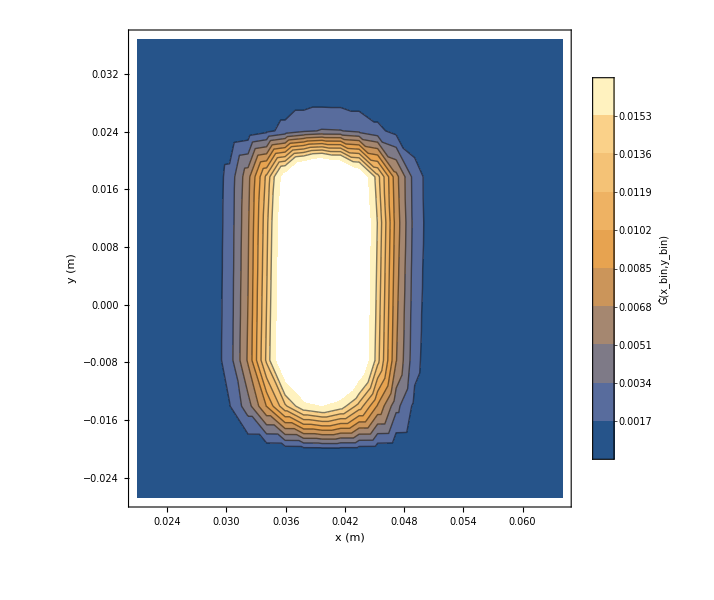

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1060/"];
```

```mathematica
dXAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]]}]];
dXAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]]}]];
dXAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}]];
dXAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]]}]];
```

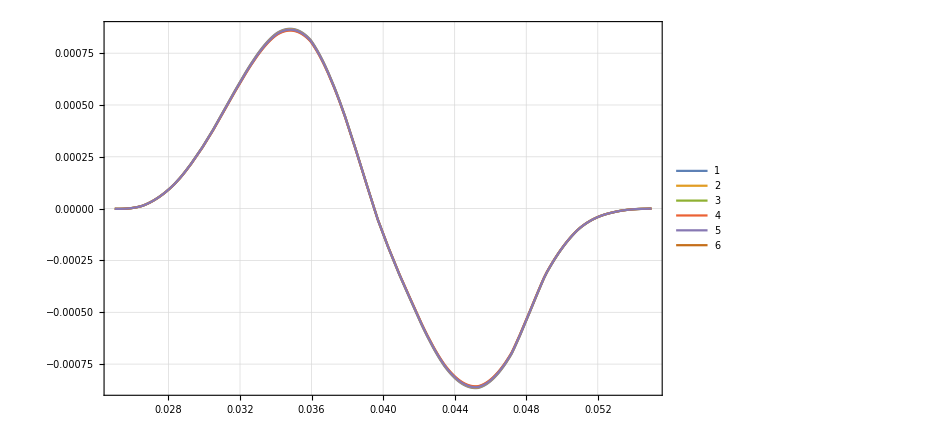

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1065/"];
```

```mathematica
dXAoffSubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_179-264.txt}

```mathematica
dXAoffSpectruma1065=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1065,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1070/"];
```

```mathematica
dXAoffSubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_179-264.txt}

```mathematica
dXAoffSpectruma1070=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1070,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXAoffDataList={dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]],dXAoffSpectruma1065[[All,2]]/Total[dXAoffSpectruma1065[[All,2]]],dXAoffSpectruma1070[[All,2]]/Total[dXAoffSpectruma1070[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

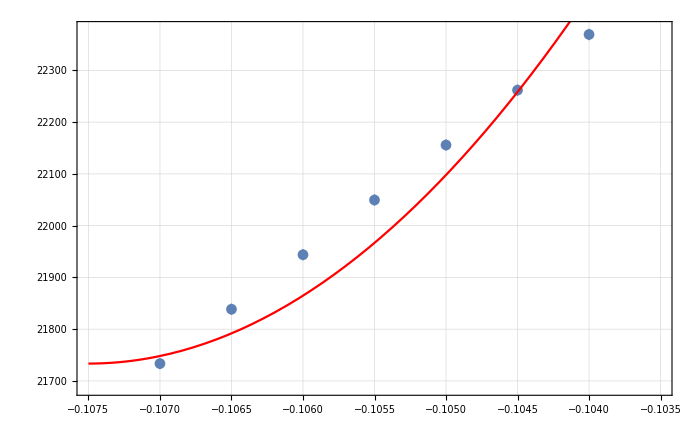
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.1075
FittedModel[0.0000217335+0.0582959 (0.1075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1075 | 0.000166925 | -644. | 3.48819×10^-11
scale | 0.0582959 | 0.00476361 | 12.2378 | 0.000256009
yoffset | 0.0000217335 | 1.69321×10^-8 | 1283.57 | 2.2104×10^-12 | 
 | DF | SS | MS
Model | 3 | 2.85677×10^7 | 9.52256×10^6
Error | 4 | 209.514 | 52.3785
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

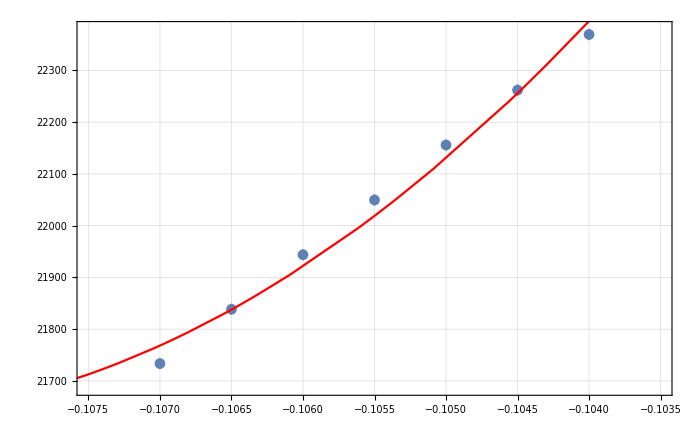
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.109236
FittedModel[0.0000216285+0.0279742 (0.109236+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.109236 | 0.000639775 | -170.741 | 7.05833×10^-9
scale | 0.0279742 | 0.00476361 | 5.87247 | 0.00420002
yoffset | 0.0000216285 | 6.36072×10^-8 | 340.032 | 4.48793×10^-10 | 
 | DF | SS | MS
Model | 3 | 2.85679×10^7 | 9.52262×10^6
Error | 4 | 33.7287 | 8.43217
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10872865859233186+0.105)/-0.105)/(0.0002)
```

177.555

```mathematica
((-0.10923565206790305+0.105)/-0.105)/(0.0002)
```

201.698

# dYAoff, k=37

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1050/"];
```

```mathematica
dYAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_179-264.txt}

```mathematica
dYAoffSpectruma0=Flatten[Table[Import[dYAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1040/"];
```

```mathematica
dYAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_179-264.txt}

```mathematica
dYAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1045/"];
```

```mathematica
dYAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_179-264.txt}

```mathematica
dYAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1055/"];
```

```mathematica
dYAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_179-264.txt}

```mathematica
dYAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

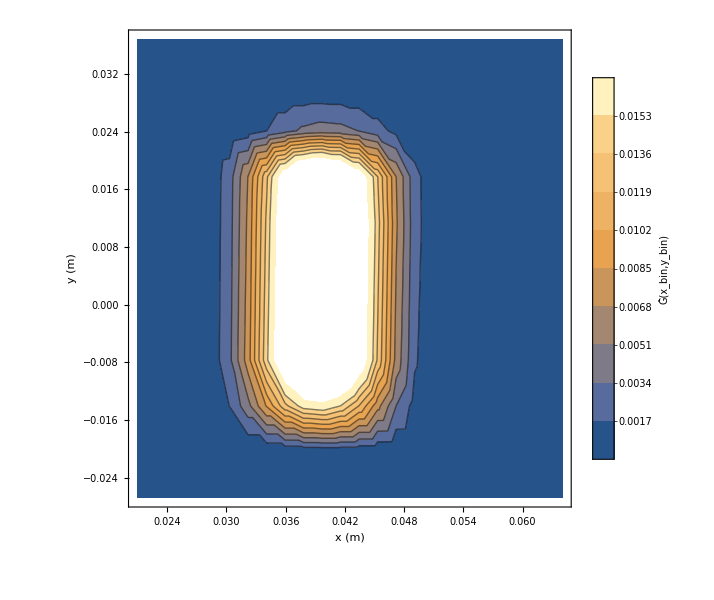

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1060/"];
```

```mathematica
dYAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]]}]];
dYAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]]}]];
dYAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]]}]];
dYAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]}]];
```

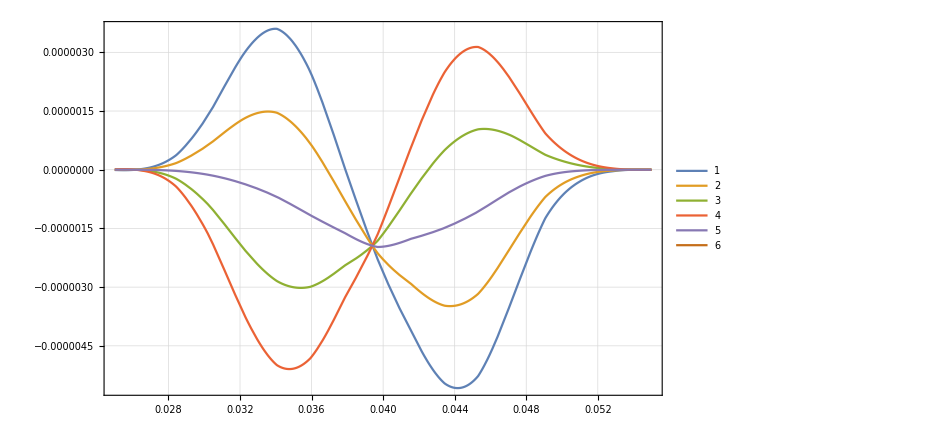

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYAoffDataList={dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

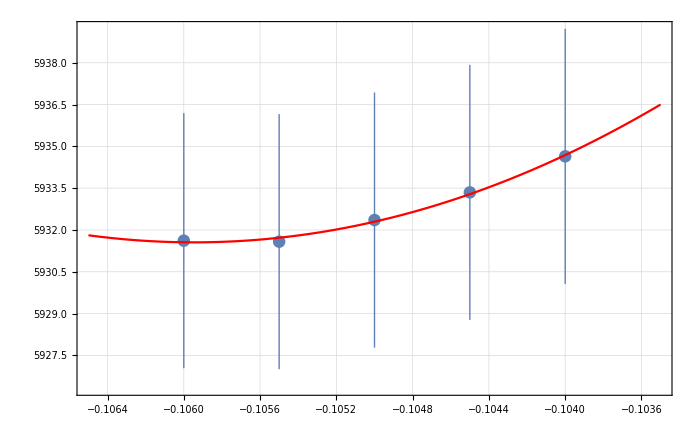
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105946
FittedModel[5.93156×10^-6+0.000826198 (0.105946+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105946 | 0.00587116 | -18.0452 | 0.00305689
scale | 0.000826198 | 0.00489193 | 0.16889 | 0.881419
yoffset | 5.93156×10^-6 | 3.92918×10^-9 | 1509.62 | 4.38801×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00154951 | 0.000774754
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

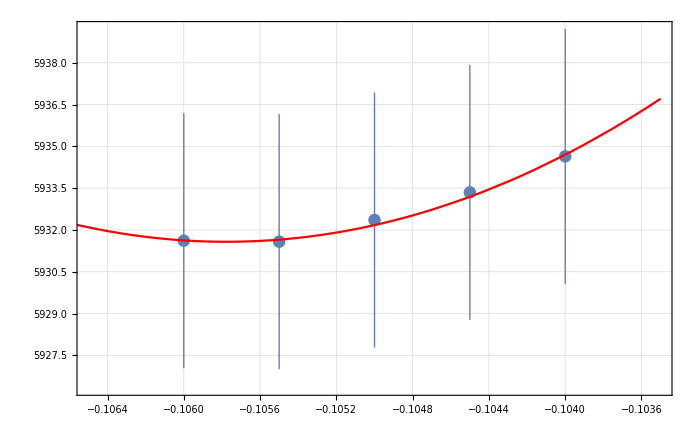
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105777
FittedModel[5.93158×10^-6+0.000989562 (0.105777+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105777 | 0.0041106 | -25.7328 | 0.00150676
scale | 0.000989562 | 0.00489193 | 0.202284 | 0.858404
yoffset | 5.93158×10^-6 | 3.08295×10^-9 | 1923.99 | 2.70143×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00318487 | 0.00159243
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1050/"];
```

```mathematica
dXDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_179-264.txt}

```mathematica
dXDShiftSpectruma0=Flatten[Table[Import[dXDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1040/"];
```

```mathematica
dXDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_179-264.txt}

```mathematica
dXDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1045/"];
```

```mathematica
dXDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_179-264.txt}

```mathematica
dXDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1055/"];
```

```mathematica
dXDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_179-264.txt}

```mathematica
dXDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

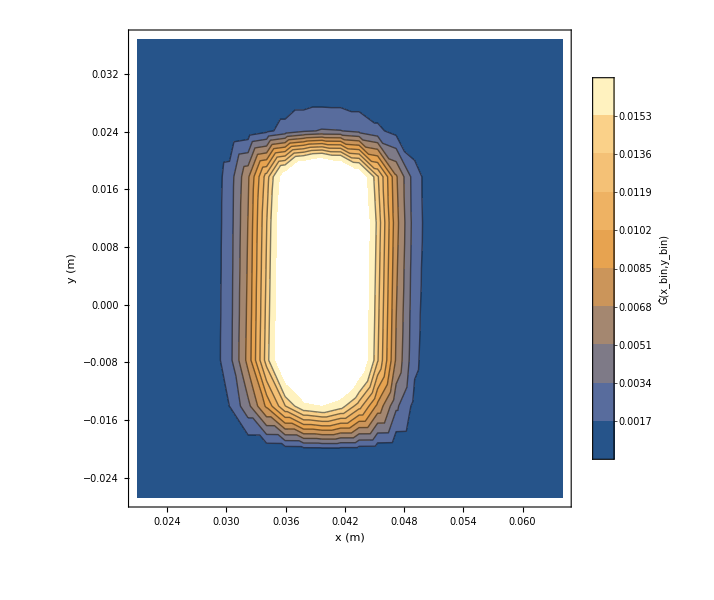

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1060/"];
```

```mathematica
dXDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]]}]];
dXDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]]}]];
dXDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}]];
dXDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]}]];
```

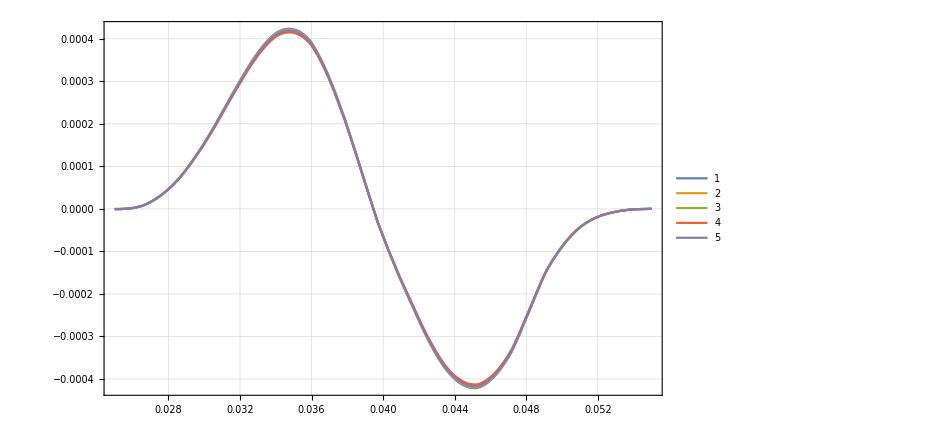

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXDShiftDataList={dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

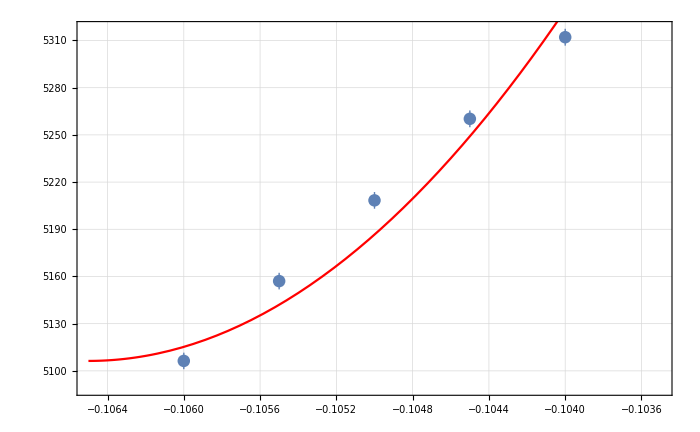
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.1065
FittedModel[5.10632×10^-6+0.0356891 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.000242302 | -439.533 | 5.17622×10^-6
scale | 0.0356891 | 0.00566881 | 6.2957 | 0.0243133
yoffset | 5.10632×10^-6 | 1.13065×10^-8 | 451.627 | 4.90272×10^-6 | 
 | DF | SS | MS
Model | 3 | 4.82403×10^6 | 1.60801×10^6
Error | 2 | 42.6424 | 21.3212
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

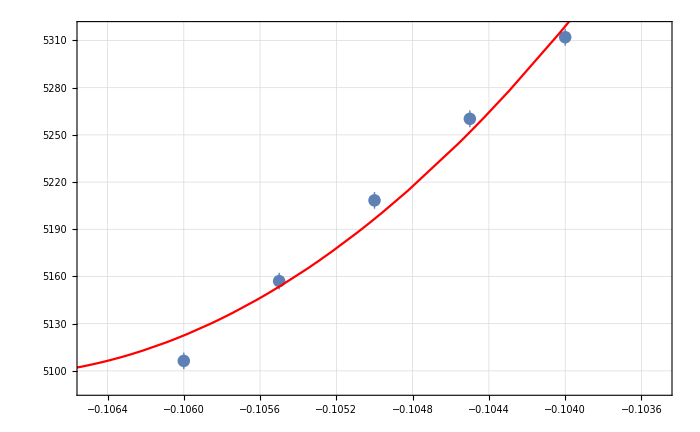
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.107033
FittedModel[5.09672×10^-6+0.0241705 (0.107033+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.107033 | 0.000480965 | -222.538 | 0.000020192
scale | 0.0241705 | 0.00566881 | 4.26377 | 0.0508474
yoffset | 5.09672×10^-6 | 2.17322×10^-8 | 234.523 | 0.0000181809 | 
 | DF | SS | MS
Model | 3 | 4.82405×10^6 | 1.60802×10^6
Error | 2 | 19.0747 | 9.53736
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10703276961983176+0.105)/-0.105)/(0.0001)
```

193.597

# dYDShift, k=29.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1050/"];
```

```mathematica
dYDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_179-264.txt}

```mathematica
dYDShiftSpectruma0=Flatten[Table[Import[dYDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1040/"];
```

```mathematica
dYDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_179-264.txt}

```mathematica
dYDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1045/"];
```

```mathematica
dYDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_179-264.txt}

```mathematica
dYDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1055/"];
```

```mathematica
dYDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_179-264.txt}

```mathematica
dYDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

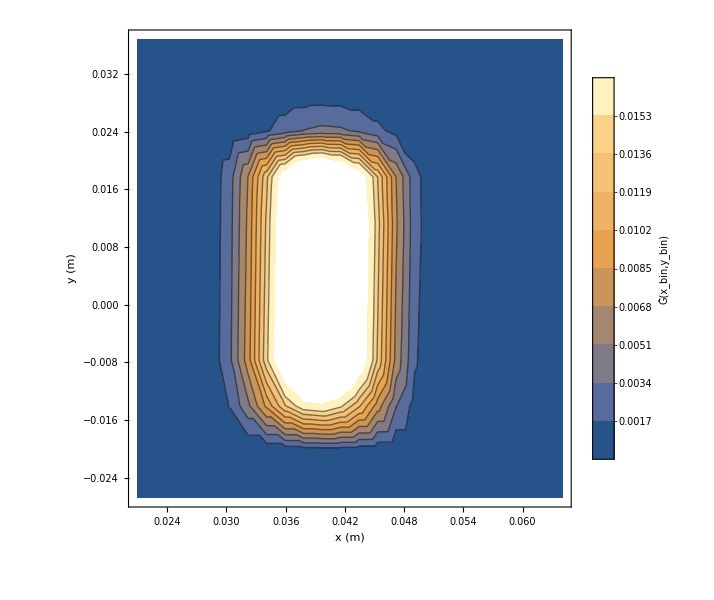

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1060/"];
```

```mathematica
dYDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]]}]];
dYDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]]}]];
dYDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}]];
dYDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]}]];
```

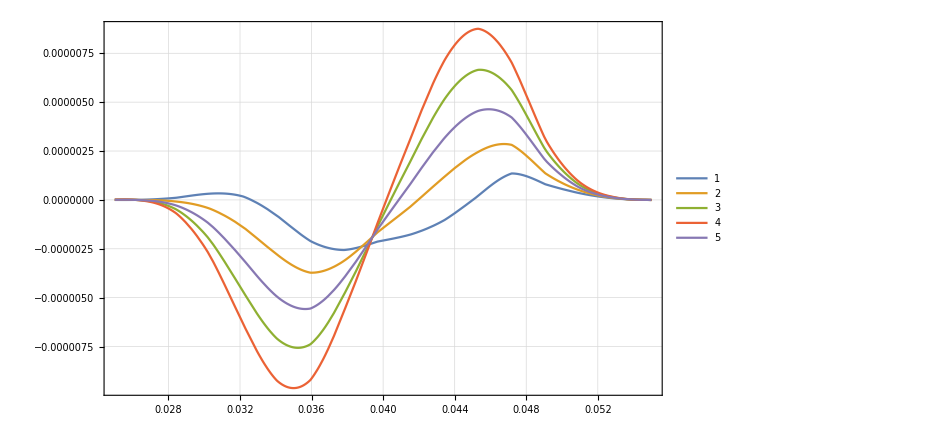

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYDShiftDataList={dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

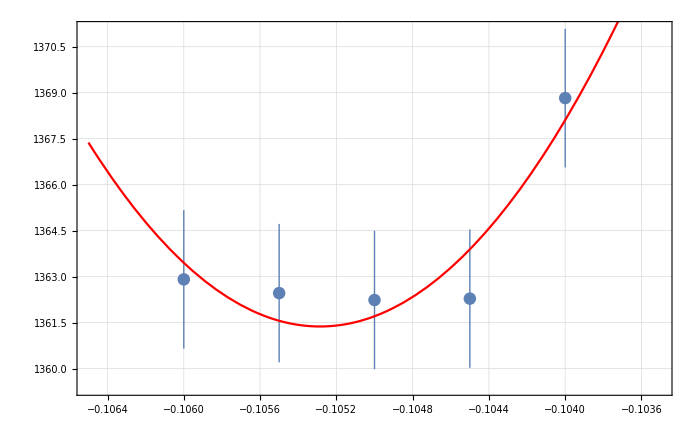
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105286
FittedModel[1.36137×10^-6+0.00407102 (0.105286+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105286 | 0.000243972 | -431.549 | 5.36952×10^-6
scale | 0.00407102 | 0.00241416 | 1.68631 | 0.233783
yoffset | 1.36137×10^-6 | 1.48442×10^-9 | 917.108 | 1.18893×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.879927 | 0.439963
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

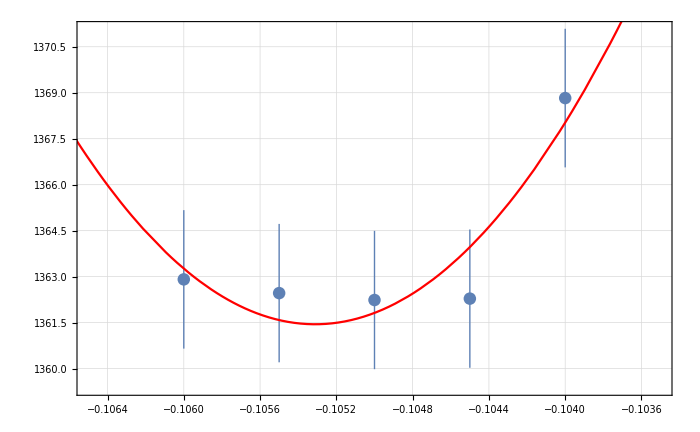
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105311
FittedModel[1.36145×10^-6+0.00382789 (0.105311+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105311 | 0.000270657 | -389.094 | 6.60522×10^-6
scale | 0.00382789 | 0.00241416 | 1.5856 | 0.253711
yoffset | 1.36145×10^-6 | 1.47058×10^-9 | 925.788 | 1.16674×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.89164 | 0.44582
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10531106171262236+0.105)/-0.105)/(0.0001)
```

29.6249

# dxAA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1050/"];
```

```mathematica
dxAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_179-264.txt}

```mathematica
dxAASpectruma0=Flatten[Table[Import[dxAASubFileNamesa0[[i]],"Table"],{i,1,Length[dxAAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1040/"];
```

```mathematica
dxAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_179-264.txt}

```mathematica
dxAASpectruma1040=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1045/"];
```

```mathematica
dxAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_179-264.txt}

```mathematica
dxAASpectruma1045=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1035/"];
```

```mathematica
dxAASubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_179-264.txt}

```mathematica
dxAASpectruma1035=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1035,1];
```

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1030/"];
```

```mathematica
dxAASubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_179-264.txt}

```mathematica
dxAASpectruma1030=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1030,1];
```

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1020/"];
```

```mathematica
dxAASubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_179-264.txt}

```mathematica
dxAASpectruma1020=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1020,1];
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1055/"];
```

```mathematica
dxAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_179-264.txt}

```mathematica
dxAASpectruma1055=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1060/"];
```

```mathematica
dxAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dxAASpectruma1060=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
dxAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dxAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]]}]];
dxAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]]}]];
dxAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}]];
dxAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]}]];
```

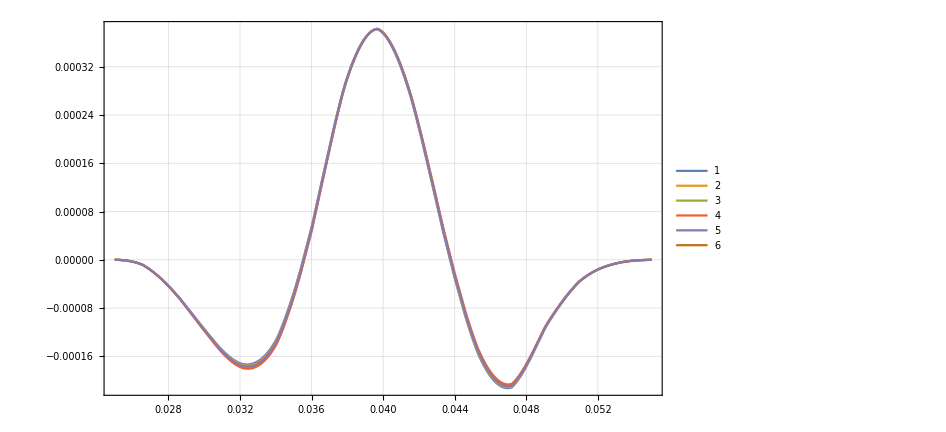

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dxAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dxAADataList2={dxAASpectruma1020[[All,2]]/Total[dxAASpectruma1020[[All,2]]],dxAASpectruma1030[[All,2]]/Total[dxAASpectruma1030[[All,2]]],dxAASpectruma1035[[All,2]]/Total[dxAASpectruma1035[[All,2]]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
dxAADataList={dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
bList2={-.102,-.103 ,-.1035 ,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

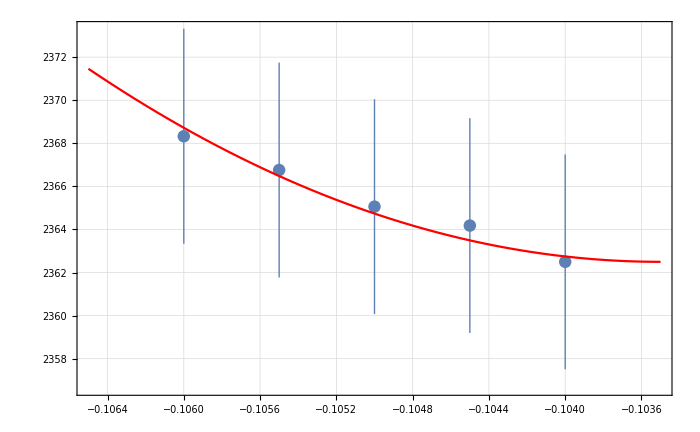
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.1035
FittedModel[2.3625×10^-6+0.000995836 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00818383 | -12.6469 | 0.00619416
scale | 0.000995836 | 0.00533118 | 0.186795 | 0.869054
yoffset | 2.3625×10^-6 | 1.06922×10^-8 | 220.954 | 0.0000204824 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0349819 | 0.0174909
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

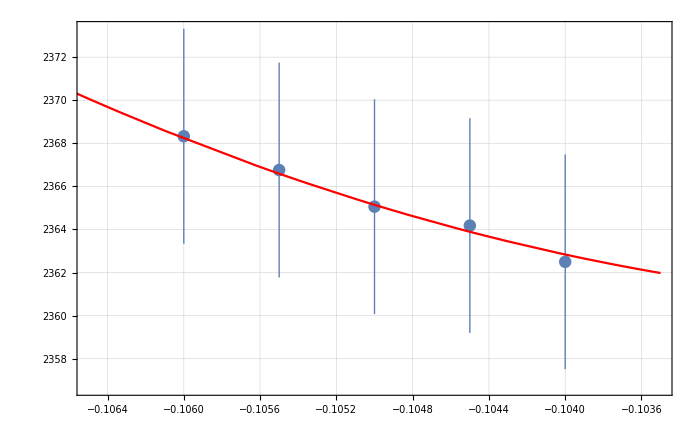
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.101557
FittedModel[2.3605×10^-6+0.000391815 (0.101557+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101557 | 0.047012 | -2.16024 | 0.16334
scale | 0.000391815 | 0.00533118 | 0.073495 | 0.948101
yoffset | 2.3605×10^-6 | 6.15185×10^-8 | 38.3705 | 0.000678519 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0097655 | 0.00488275
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

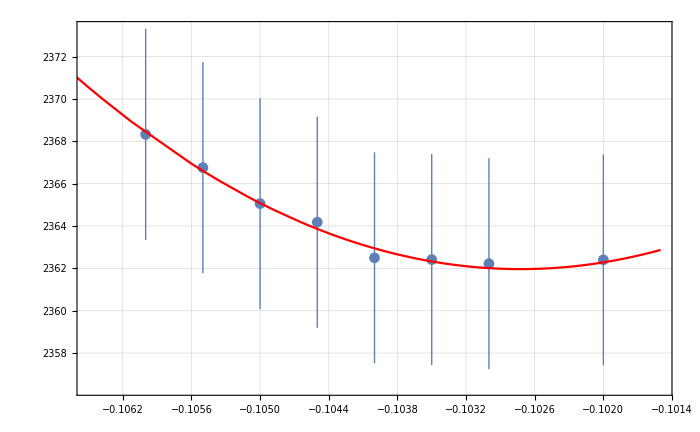
{{{2.3624×10^-6,2.36222×10^-6,2.36241×10^-6,2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98246×10^-9,4.98351×10^-9,4.98425×10^-9,4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.102726
FittedModel[2.36197×10^-6+0.000602823 (0.102726+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.102726 | 0.00276563 | -37.1437 | 2.66387×10^-7
scale | 0.000602823 | 0.00115011 | 0.524143 | 0.622575
yoffset | 2.36197×10^-6 | 2.71803×10^-9 | 868.999 | 3.83002×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.79902×10^6 | 599675.
Error | 5 | 0.0161217 | 0.00322434
Uncorrected Total | 8 | 1.79902×10^6 | 
Corrected Total | 7 | 1.50969 |  | ,-Graphics-}

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList2,bList2, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

```mathematica
((-0.10272571946582504+0.105)/-0.105)/(0.0002)
```

-108.299

# dyAA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1050/"];
```

```mathematica
dyAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_179-264.txt}

```mathematica
dyAASpectruma0=Flatten[Table[Import[dyAASubFileNamesa0[[i]],"Table"],{i,1,Length[dyAASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1040/"];
```

```mathematica
dyAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_179-264.txt}

```mathematica
dyAASpectruma1040=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1045/"];
```

```mathematica
dyAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_179-264.txt}

```mathematica
dyAASpectruma1045=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1055/"];
```

```mathematica
dyAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_179-264.txt}

```mathematica
dyAASpectruma1055=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1060/"];
```

```mathematica
dyAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dyAASpectruma1060=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
dyAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma0[[All,2]]/Total[dyAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dyAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1040[[All,2]]/Total[dyAASpectruma1040[[All,2]]]}]];
dyAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1045[[All,2]]/Total[dyAASpectruma1045[[All,2]]]}]];
dyAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1055[[All,2]]/Total[dyAASpectruma1055[[All,2]]]}]];
dyAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1060[[All,2]]/Total[dyAASpectruma1060[[All,2]]]}]];
```

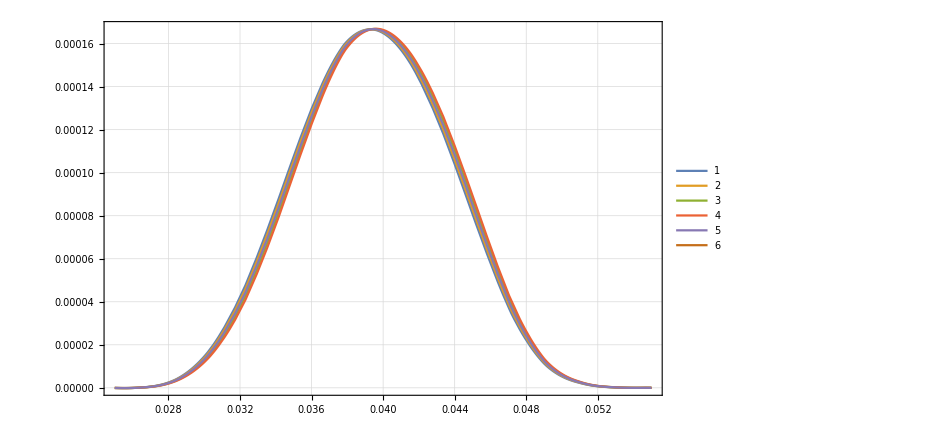

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dyAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dyAADataList={dyAASpectruma1040[[All,2]]/Total[dyAASpectruma1040[[All,2]]],dyAASpectruma1045[[All,2]]/Total[dyAASpectruma1045[[All,2]]],dyAASpectruma0[[All,2]]/Total[dyAASpectruma0[[All,2]]],dyAASpectruma1055[[All,2]]/Total[dyAASpectruma1055[[All,2]]],dyAASpectruma1060[[All,2]]/Total[dyAASpectruma1060[[All,2]]]};
```

```mathematica
bList2={-.102,-.103 ,-.1035 ,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

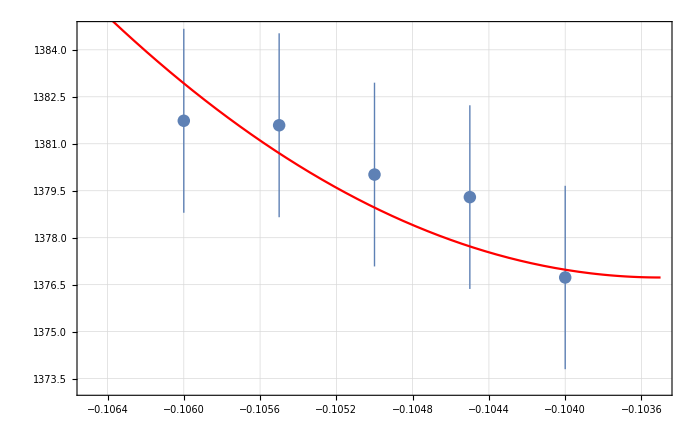
{{{1.37673×10^-6,1.3793×10^-6,1.38002×10^-6,1.38159×10^-6,1.38173×10^-6},{2.92816×10^-9,2.93259×10^-9,2.93429×10^-9,2.93668×10^-9,2.93746×10^-9}},a0 =  | -0.1035
FittedModel[1.37673×10^-6+0.000992024 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00483143 | -21.4222 | 0.00217197
scale | 0.000992024 | 0.00313604 | 0.316331 | 0.781715
yoffset | 1.37673×10^-6 | 6.28502×10^-9 | 219.05 | 0.0000208402 | 
 | DF | SS | MS
Model | 3 | 1.10605×10^6 | 368685.
Error | 2 | 0.682849 | 0.341424
Uncorrected Total | 5 | 1.10605×10^6 | 
Corrected Total | 4 | 1.93721 |  | ,-Graphics-}

```mathematica
dyAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dyAADataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

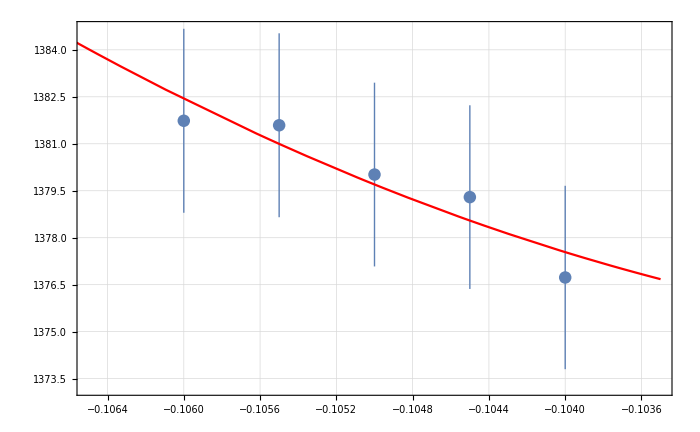
{{{1.37673×10^-6,1.3793×10^-6,1.38002×10^-6,1.38159×10^-6,1.38173×10^-6},{2.92816×10^-9,2.93259×10^-9,2.93429×10^-9,2.93668×10^-9,2.93746×10^-9}},a0 =  | -0.100757
FittedModel[1.3745×10^-6+0.00028858 (0.100757+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.100757 | 0.0462152 | -2.18017 | 0.161048
scale | 0.00028858 | 0.00313604 | 0.0920207 | 0.935069
yoffset | 1.3745×10^-6 | 5.54518×10^-8 | 24.7874 | 0.00162361 | 
 | DF | SS | MS
Model | 3 | 1.10605×10^6 | 368685.
Error | 2 | 0.25157 | 0.125785
Uncorrected Total | 5 | 1.10605×10^6 | 
Corrected Total | 4 | 1.93721 |  | ,-Graphics-}

```mathematica
dyAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dyAADataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

```mathematica
((-0.10075697631656662+0.105)/-0.105)/(0.0002)
```

-202.049

```mathematica
202
```

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1050/"];
```

```mathematica
dxAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_179-264.txt}

```mathematica
dxAASpectruma0=Flatten[Table[Import[dxAASubFileNamesa0[[i]],"Table"],{i,1,Length[dxAASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1040/"];
```

```mathematica
dxAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_179-264.txt}

```mathematica
dxAASpectruma1040=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1045/"];
```

```mathematica
dxAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_179-264.txt}

```mathematica
dxAASpectruma1045=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1055/"];
```

```mathematica
dxAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_179-264.txt}

```mathematica
dxAASpectruma1055=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

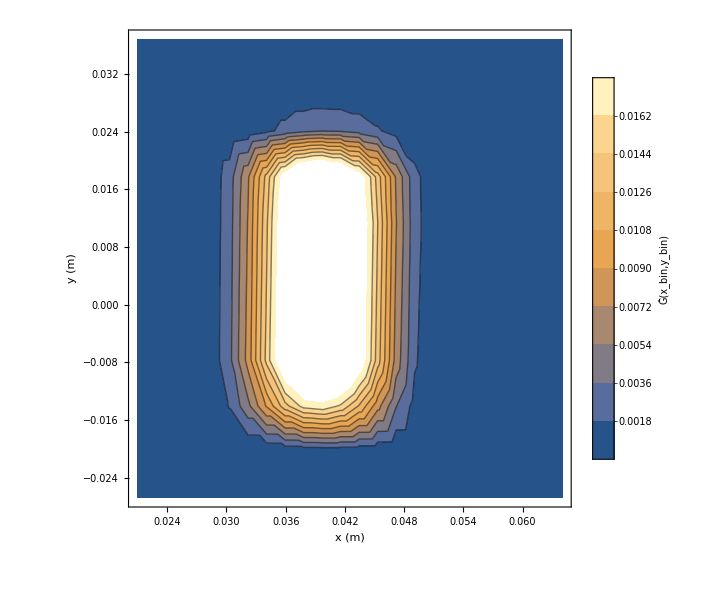

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1060/"];
```

```mathematica
dxAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dxAASpectruma1060=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dxAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dxAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]]}]];
dxAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]]}]];
dxAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}]];
dxAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]}]];
```

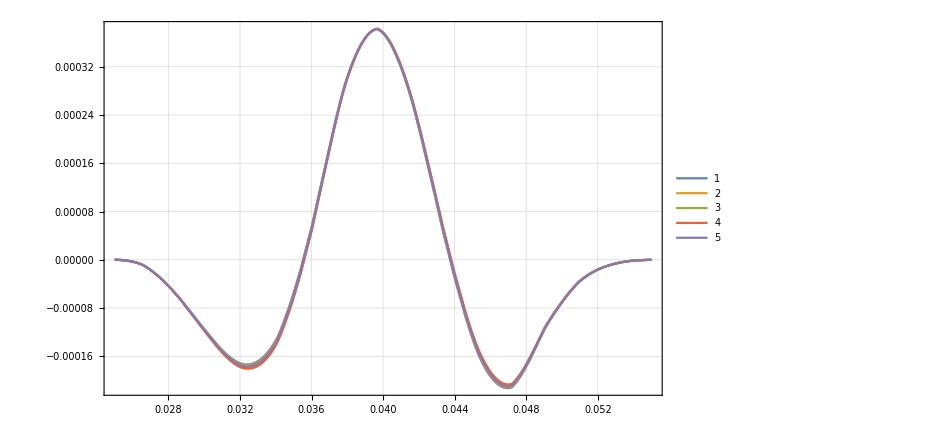

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dxAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dxAADataList={dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dxAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.1035
FittedModel[2.3625×10^-6+0.000995836 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00818383 | -12.6469 | 0.00619416
scale | 0.000995836 | 0.00533118 | 0.186795 | 0.869054
yoffset | 2.3625×10^-6 | 1.06922×10^-8 | 220.954 | 0.0000204824 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0349819 | 0.0174909
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.101557
FittedModel[2.3605×10^-6+0.000391815 (0.101557+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101557 | 0.047012 | -2.16024 | 0.16334
scale | 0.000391815 | 0.00533118 | 0.073495 | 0.948101
yoffset | 2.3605×10^-6 | 6.15185×10^-8 | 38.3705 | 0.000678519 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0097655 | 0.00488275
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
-0.1065
```

-0.1065

```mathematica
0.00025
```

0.00025

```mathematica
0.2/1000
```

0.0002

```mathematica
((-0.1035+0.105)/-0.105)/(0.0002)
```

-71.4286

```mathematica
((-0.10155733953850894+0.105)/-0.105)/(0.0002)
```

-163.936

# No Neutron centered at 0 Beam prof. r=322.89

## da0 NoBeam0 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_noBeam0/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNoBeam0=Flatten[Table[Import[d0SubFileNamesa01DNoBeam0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNoBeam0]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBins1D0Shift=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf0Shift=BinCenters[xyBins1D0Shift];
```

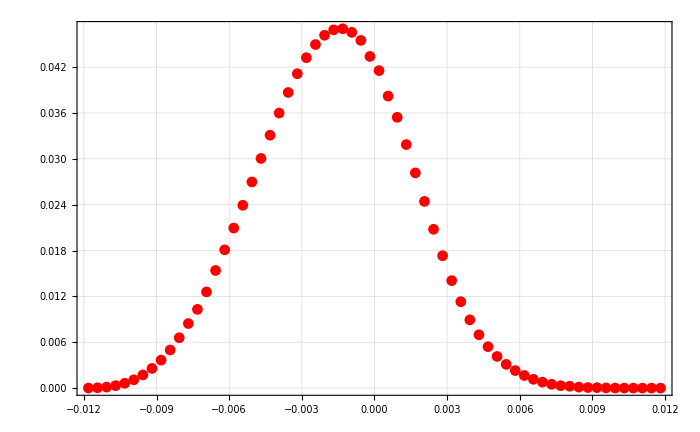

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf0Shift[[All,1]],d0Spectruma01DNoBeam0[[All,2]]/Total[d0Spectruma01DNoBeam0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNoBeam0Inter=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],d0Spectruma01DNoBeam0[[All,2]]/Total[d0Spectruma01DNoBeam0[[All,2]]]}]];
```

## drA NoBeam 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

```mathematica
pmax
```

1.18728×10^6

```mathematica
ppmax
```

1.18728×10^6

## a=-0.104

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1040/"];
```

```mathematica
drASubFileNamesa10401DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNoBeam0=Flatten[Table[Import[drASubFileNamesa10401DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNoBeam0]}],1];
```

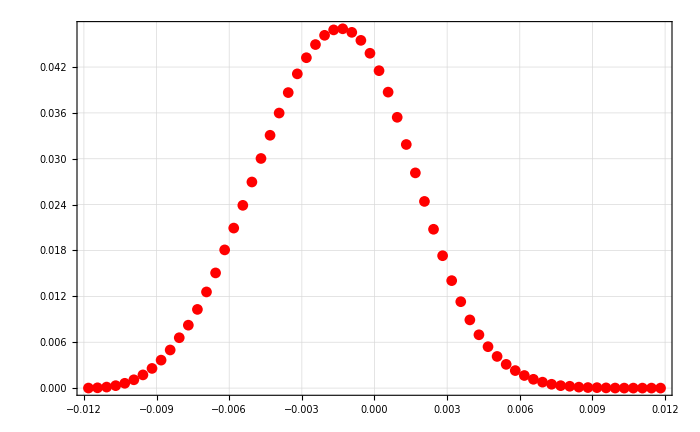

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1045/"];
```

```mathematica
drASubFileNamesa10451DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNoBeam0=Flatten[Table[Import[drASubFileNamesa10451DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNoBeam0]}],1];
```

```mathematica
drAa1045Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10451DNoBeam0[[All,2]]/Total[drASpectruma10451DNoBeam0[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1050/"];
```

```mathematica
drASubFileNamesa01DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_57-64.txt}

```mathematica
drASpectruma01DNoBeam0=Flatten[Table[Import[drASubFileNamesa01DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNoBeam0]}],1];
```

```mathematica
drASpectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma01DNoBeam0[[All,2]]/Total[drASpectruma01DNoBeam0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1055/"];
```

```mathematica
drASubFileNamesa10551DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNoBeam0=Flatten[Table[Import[drASubFileNamesa10551DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNoBeam0]}],1];
```

```mathematica
drAa1055Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10551DNoBeam0[[All,2]]/Total[drASpectruma10551DNoBeam0[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1060/"];
```

```mathematica
drASubFileNamesa10601DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNoBeam0=Flatten[Table[Import[drASubFileNamesa10601DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNoBeam0]}],1];
```

```mathematica
drAa1060Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10601DNoBeam0[[All,2]]/Total[drASpectruma10601DNoBeam0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

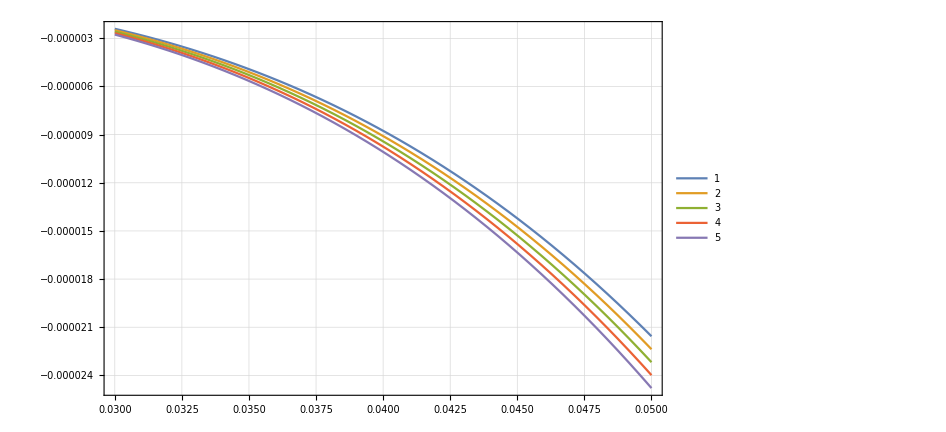

```mathematica
Plot[{
da0Spectrum1DNoBeam0Inter[x]-drAa1040Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1045Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drASpectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1055Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1060Spectrum1DNoBeamInter0[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]],drASpectruma10451DNoBeam0[[All,2]]/Total[drASpectruma10451DNoBeam0[[All,2]]],drASpectruma01DNoBeam0[[All,2]]/Total[drASpectruma01DNoBeam0[[All,2]]],drASpectruma10551DNoBeam0[[All,2]]/Total[drASpectruma10551DNoBeam0[[All,2]]],drASpectruma10601DNoBeam0[[All,2]]/Total[drASpectruma10601DNoBeam0[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

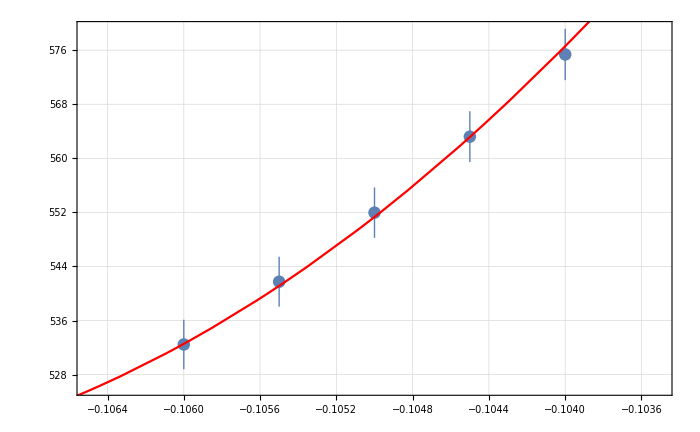
{{{5.75362×10^-7,5.63203×10^-7,5.51966×10^-7,5.4175×10^-7,5.32467×10^-7},{3.79773×10^-9,3.75901×10^-9,3.72209×10^-9,3.68739×10^-9,3.65469×10^-9}},a0 =  | -0.10839
FittedModel[5.14005×10^-7+0.00324673 (0.10839+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10839 | 0.00416516 | -26.0231 | 0.00147341
scale | 0.00324673 | 0.00398146 | 0.815463 | 0.500475
yoffset | 5.14005×10^-7 | 4.43432×10^-8 | 11.5915 | 0.00736044 | 
 | DF | SS | MS
Model | 3 | 110204. | 36734.8
Error | 2 | 0.162758 | 0.081379
Uncorrected Total | 5 | 110205. | 
Corrected Total | 4 | 82.9153 |  | ,-Graphics-}

```mathematica
drAInvest0=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01DNoBeam0[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10839034581739389+0.105)/-0.105)/(10^-4)
```

322.89

```mathematica
r
```

```mathematica
{{MeanX, MeanY}, {ApertX, ApertY}, {BDV}, {BF}, {BA}, {BRxB}, {BDet}}={{0.0301277, 1.00623}, {0.01, 
  0.035}, {0.220899}, {0.451107}, {0.219769}, {0.219722}, {0.207816}};
  
ApertXOff = 0.03; 
ApertYOff = 0.;

(*CenterfitG1=0.96907;
CenterfitG2=0.973888;*)
BlinefitG1=0.965547;
BlinefitG2=0.974009;

rF = BF/BDV;
rA = BA/BDV;
rRxB = BRxB/BDV;
rDet = BDet/BRxB;
```

```mathematica
rFSC=2.036;
rASC=0.937;
rRxBSC=0.902;
bRxBSC=0.976;
g1SC=1.29;
g2SC=1.792;
alphaSC=180.03*Pi/180;
rDSC=0.88;
```

```mathematica
Sqrt[rDet/rRxB]
```

0.975131

```mathematica
Sqrt[rDet]
```

0.972529

```mathematica
Sqrt[rDSC/rRxBSC]
```

0.98773

```mathematica
Sqrt[rDSC]
```

0.938083

0.972529

# NormalConducting Centered With no Beam k=50.07approx?

## da0 Normal 01D, (0.01,0.035), -0.05x offset, noBeam;

## a=-0.105

```mathematica
d0SubFileNamesa01DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormal0=Flatten[Table[Import[d0SubFileNamesa01DNormal0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormal0]}],1];
```

```mathematica
xStart=-0.06;
xEnd=0.06;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal0=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal0=BinCenters[xyBinsNormal0];
```

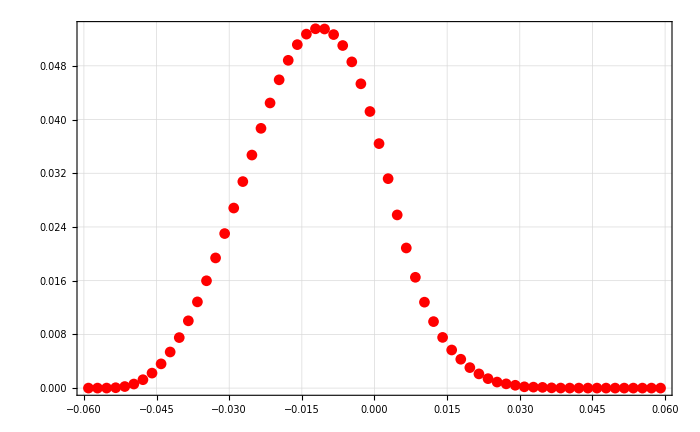

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}]];
```

## drA Normal0 1D, (0.01,0.035), -0.05x offset, noBeam;

## a=-0.104

```mathematica
drASubFileNamesa10401DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormal0=Flatten[Table[Import[drASubFileNamesa10401DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormal0]}],1];
```

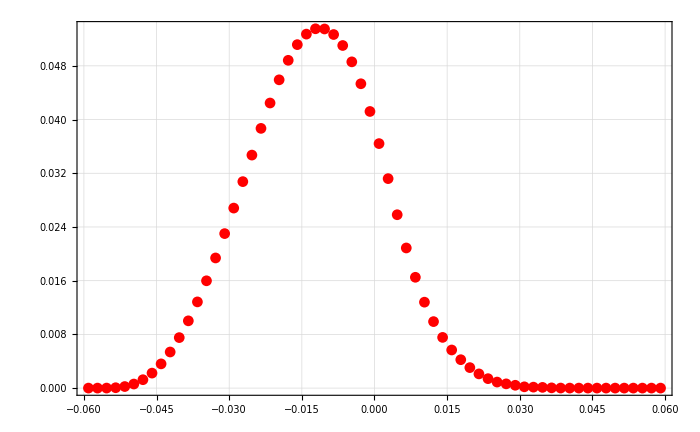

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
drASubFileNamesa10451DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormal0=Flatten[Table[Import[drASubFileNamesa10451DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormal0]}],1];
```

```mathematica
drAa1045Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10451DNormal0[[All,2]]/Total[drASpectruma10451DNormal0[[All,2]]]}]];
```

## a=-0.105

```mathematica
drASubFileNamesa01DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormal0=Flatten[Table[Import[drASubFileNamesa01DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormal0]}],1];
```

```mathematica
drASpectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma01DNormal0[[All,2]]/Total[drASpectruma01DNormal0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
drASubFileNamesa10551Dnormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormal0=Flatten[Table[Import[drASubFileNamesa10551Dnormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551Dnormal0]}],1];
```

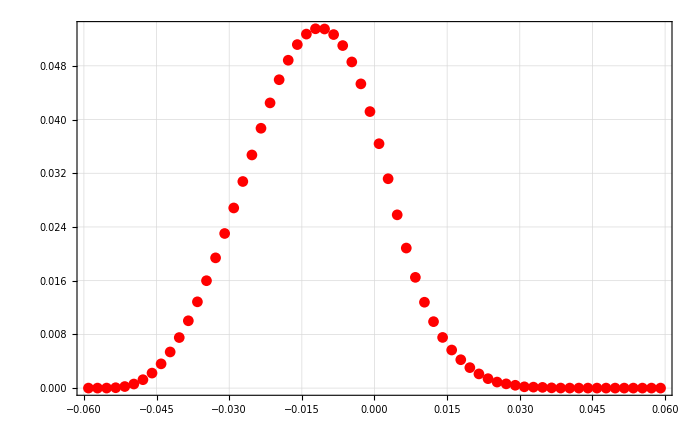

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]]}]];
```

### a=-1060

```mathematica
drASubFileNamesa10601DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormal0Check=Flatten[Table[Import[drASubFileNamesa10601DNormal0Check[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal0Check]}],1];
```

```mathematica
drASpectruma10601DNormal0[[All,2]]==drASpectruma10601DNormal0Check[[All,2]]
```

True

```mathematica
drASpectruma10601DNormal0=Flatten[Table[Import[drASubFileNamesa10601DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal0]}],1];
```

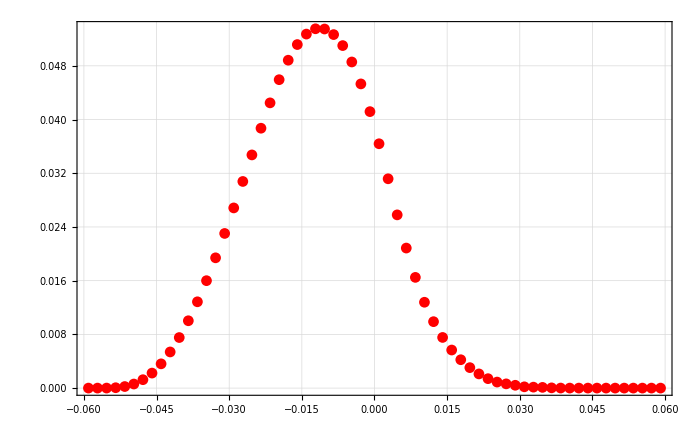

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]}]];
```

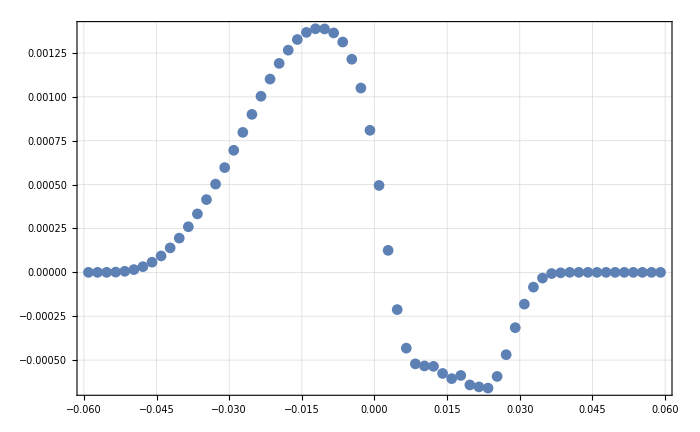

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]-drASpectruma10451DNormal0[[All,2]]}],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0599975} lies outside the range of data in the interpolating function. Extrapolation will be used.

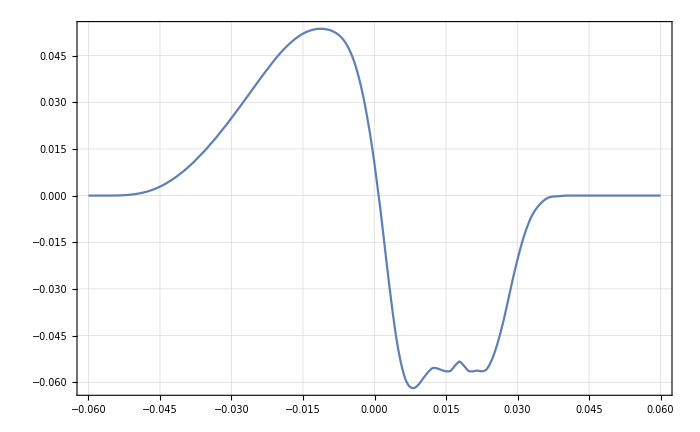

```mathematica
Plot[da0Spectrum1DNormal0Inter[x]-drAa1045Spectrum1DNormal0Inter[x],{x,-0.06,0.06},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0599975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

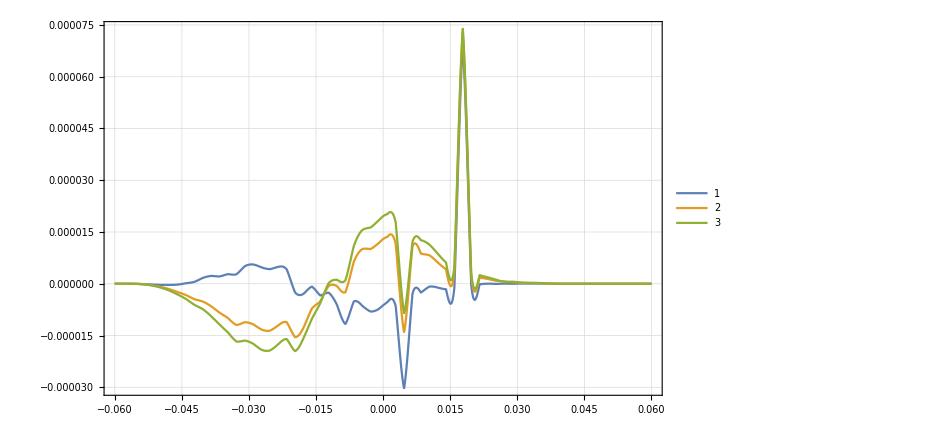

```mathematica
Plot[{
da0Spectrum1DNormal0Inter[x]-drAa1040Spectrum1DNormal0Inter[x],

da0Spectrum1DNormal0Inter[x]-drAa1055Spectrum1DNormal0Inter[x],
da0Spectrum1DNormal0Inter[x]-drAa1060Spectrum1DNormal0Inter[x]
}
,{x,-0.06,0.06},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
{{MeanX, MeanY}, {ApertX, ApertY}, {BDV}, {BF}, {BA}, {BRxB}, {BDet}}={{0.0301277, 1.00623}, {0.01, 
  0.035}, {0.220899}, {0.451107}, {0.219769}, {0.219722}, {0.207816}};
```

```mathematica
BA/BDV
```

0.994885

```mathematica
BF/BDV
```

2.04214

```mathematica
BRxB/BDV
```

0.994672

```mathematica
BDet/BRxB
```

0.945813

```mathematica
?xAShift
```

```mathematica
?DeltaxDV2Shift
```

```mathematica
?pXDomainShift
```

```mathematica
?phiAminApertShift
```

```mathematica
?DeltaxDVShift
```

```mathematica
?D1stBPolyGradwoR
```

```mathematica
?BpolynomGradwoR
```

```mathematica
?D1stBPolyGradwoR
```

```mathematica
?DeltayDVShift
```

```mathematica
?yGCAShift
```

```mathematica
?xGCAShift
```

```mathematica
?BpolynomGradwoR
```

```mathematica
2^2/3
```

4/3

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]],drASpectruma10451DNormal0[[All,2]]/Total[drASpectruma10451DNormal0[[All,2]]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]};
```

```mathematica
bList={-.1040,-0.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

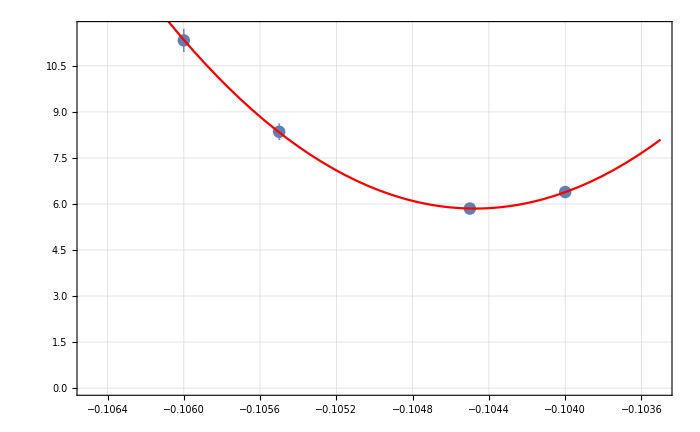
{{{6.38811×10^-9,5.85064×10^-9,8.35319×10^-9,1.13297×10^-8},{1.94786×10^-10,1.45323×10^-10,2.71656×10^-10,3.78657×10^-10}},a0 =  | -0.104475
FittedModel[5.85062×10^-9+0.0023635 (0.104475+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104475 | 0.0000672803 | -1552.83 | 0.000409974
scale | 0.0023635 | 0.000295921 | 7.98693 | 0.0792951
yoffset | 5.85062×10^-9 | 1.30664×10^-10 | 44.7759 | 0.0142155 | 
 | DF | SS | MS
Model | 3 | 4537.13 | 1512.38
Error | 1 | 0.00779565 | 0.00779565
Uncorrected Total | 4 | 4537.14 | 
Corrected Total | 3 | 222.836 |  | ,-Graphics-}

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormal0[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10447488769311862+0.105)/-0.105)/(10^-4)
```

-50.0107

# NormalConducting Non-Centered with no Beam prof rA=39.07

## da0 NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.1; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormal=Flatten[Table[Import[d0SubFileNamesa01DNormal[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormal]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal=BinCenters[xyBinsNormal];
```

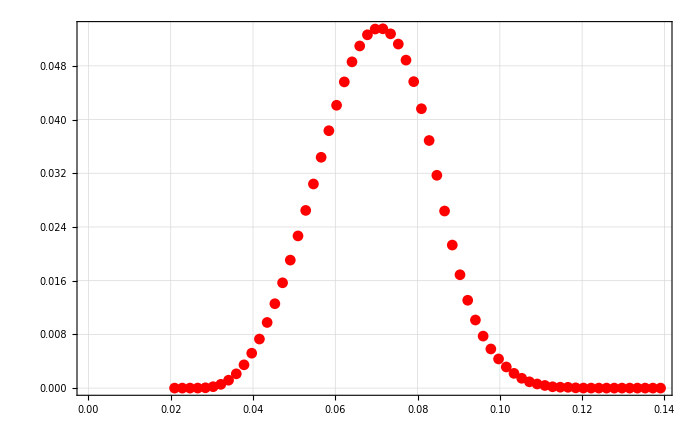

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red]
```

-Graphics-

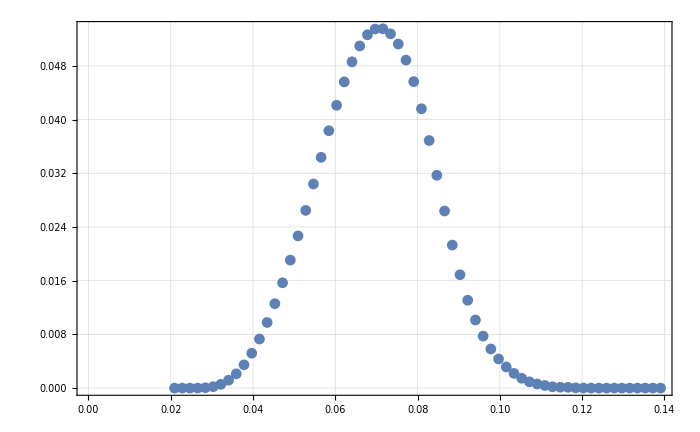

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]]
```

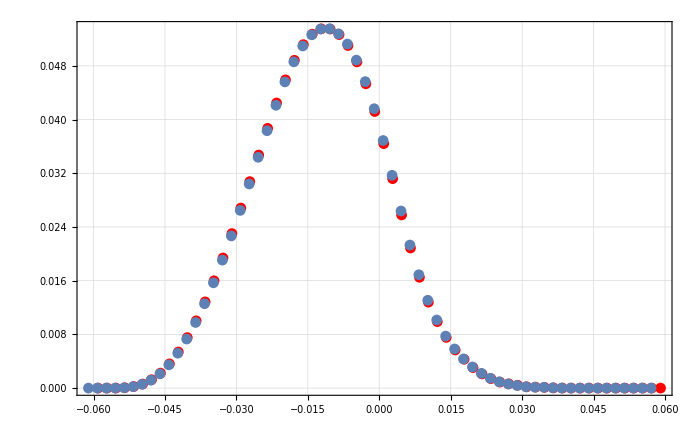

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]]-0.082,d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]],PlotRange->All]
```

## drA NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.1; yAASC=35/1000;

## a=-0.104

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1040/"];
```

```mathematica
drASubFileNamesa10401DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormal=Flatten[Table[Import[drASubFileNamesa10401DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormal]}],1];
```

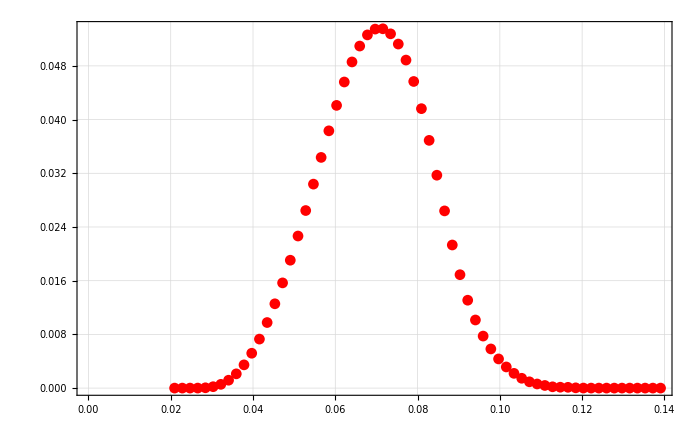

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]]}]];
```

## a=-0.1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1045/"];
```

```mathematica
drASubFileNamesa10451DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormal=Flatten[Table[Import[drASubFileNamesa10451DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormal]}],1];
```

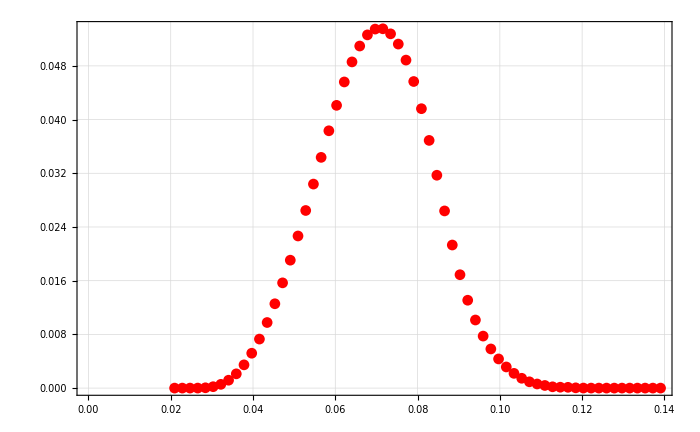

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1045Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1050/"];
```

```mathematica
drASubFileNamesa01DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormal=Flatten[Table[Import[drASubFileNamesa01DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormal]}],1];
```

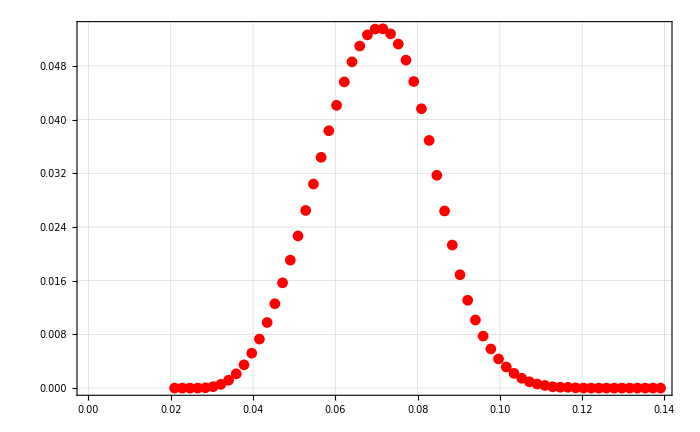

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drASpectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1055/"];
```

```mathematica
drASubFileNamesa10551DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormal=Flatten[Table[Import[drASubFileNamesa10551DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNormal]}],1];
```

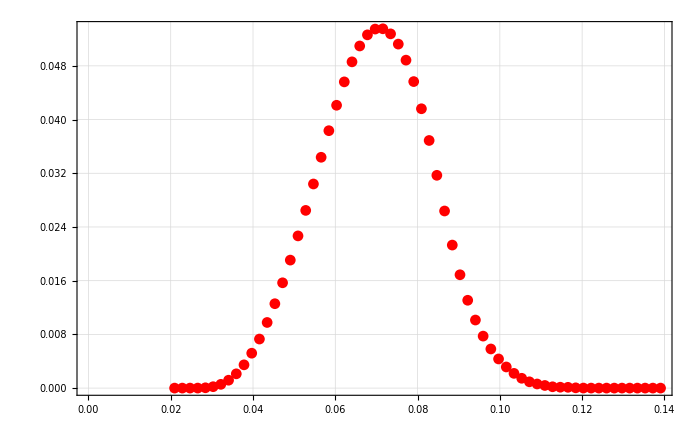

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1060/"];
```

```mathematica
drASubFileNamesa10601DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormal=Flatten[Table[Import[drASubFileNamesa10601DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal]}],1];
```

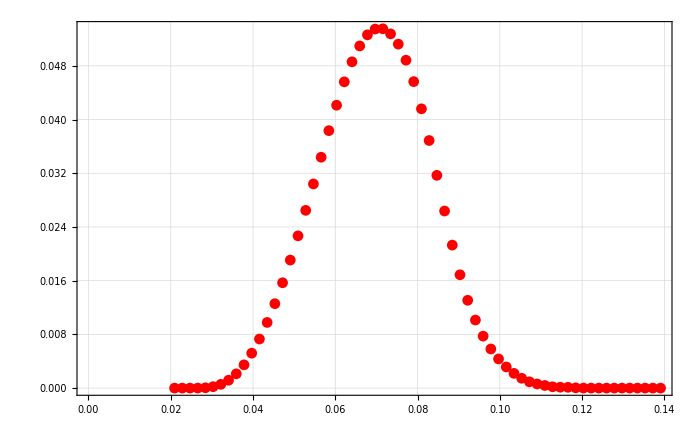

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

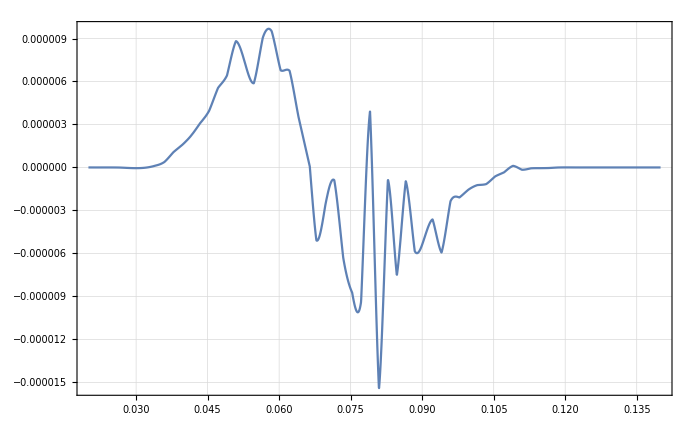

```mathematica
Show[Plot[drAa1060Spectrum1DNormalInter[x]-da0Spectrum1DNormalInter[x],{x,0.02,0.14}]]
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

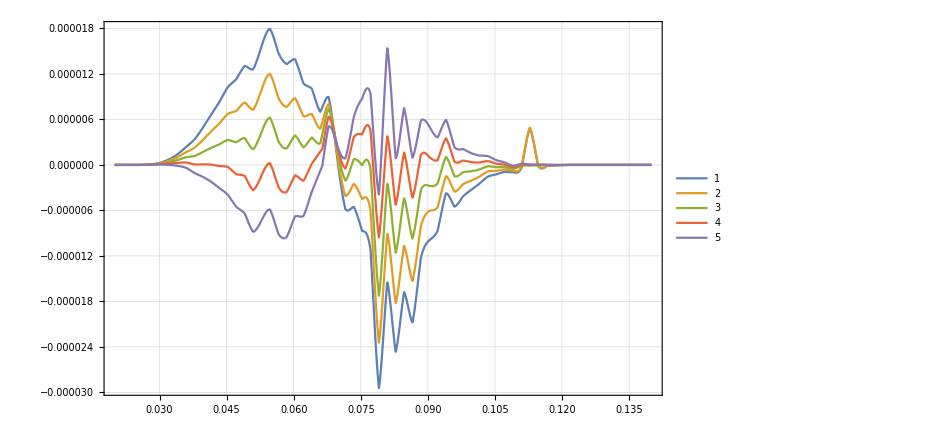

```mathematica
Plot[{
da0Spectrum1DNormalInter[x]-drAa1040Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1045Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drASpectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1055Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1060Spectrum1DNormalInter[x]
}
,{x,0.02,0.14},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

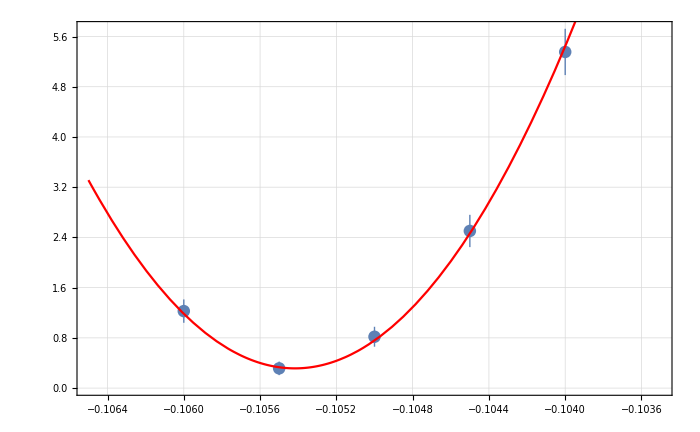
{{{5.35418×10^-9,2.50274×10^-9,8.17824×10^-10,3.14289×10^-10,1.22629×10^-9},{3.68704×10^-10,2.57071×10^-10,1.58799×10^-10,1.07937×10^-10,1.85956×10^-10}},a0 =  | -0.105417
FittedModel[3.14289×10^-10+0.00255551 (0.105417+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105417 | 0.0000399815 | -2636.64 | 1.43846×10^-7
scale | 0.00255551 | 0.000231945 | 11.0178 | 0.00813743
yoffset | 3.14289×10^-10 | 8.92047×10^-11 | 3.52324 | 0.0719708 | 
 | DF | SS | MS
Model | 3 | 383.843 | 127.948
Error | 2 | 0.304842 | 0.152421
Uncorrected Total | 5 | 384.148 | 
Corrected Total | 4 | 216.661 |  | ,-Graphics-}

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormal[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10541686155163119+0.105)/-0.105)/(10^-4)
```

39.7011

# NormalConducting Non-Centered Small Aperture with no Beam prof rA=12.9145

## da0 NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.1; yAASC=35/1000;

## a=-0.105

```mathematica
39/12.9
```

3.02326

```mathematica
150/3
```

50

```mathematica
Solve[xOff+xAA/2==xAShift[phiAlocal,yD,xD,plocal,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,{XAShift,YRxBShift,XDetShift,YDetShift}],phiAlocal][[All,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InverseFunction[xAShift,1,15][1/2 (xAA+2 xOff),yD,xD,plocal,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,{XAShift,YRxBShift,XDetShift,YDetShift}]}

```mathematica
?rG
```

```mathematica
rG[ppmax,45*Pi/180.,.976]
```

0.00286926

```mathematica
rG[ppmax,45*Pi/180.,.219]
```

0.0127872

```mathematica
5/1000.
```

0.005

```mathematica
(4*0.01278718679057855)
```

0.0511487

```mathematica
4*0.0028692560523941616
```

0.011477

```mathematica
0.011477024209576647/0.001
```

11.477

```mathematica
0.0511487471623142/0.005
```

10.2297

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal_smallApt/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNormalSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormalSA=Flatten[Table[Import[d0SubFileNamesa01DNormalSA[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormalSA]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal=BinCenters[xyBinsNormal];
```

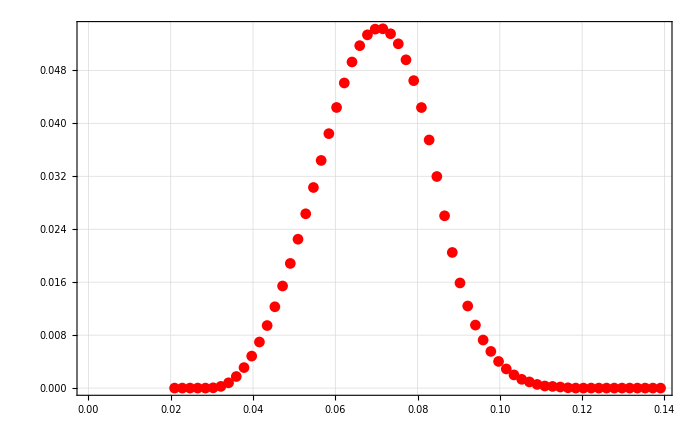

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormalSA[[All,2]]/Total[d0Spectruma01DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormalSA[[All,2]]/Total[d0Spectruma01DNormalSA[[All,2]]]}]];
```

## drA NoBeam 1D;

## a=-0.104

```mathematica
drASubFileNamesa10401DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormalSA=Flatten[Table[Import[drASubFileNamesa10401DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormalSA]}],1];
```

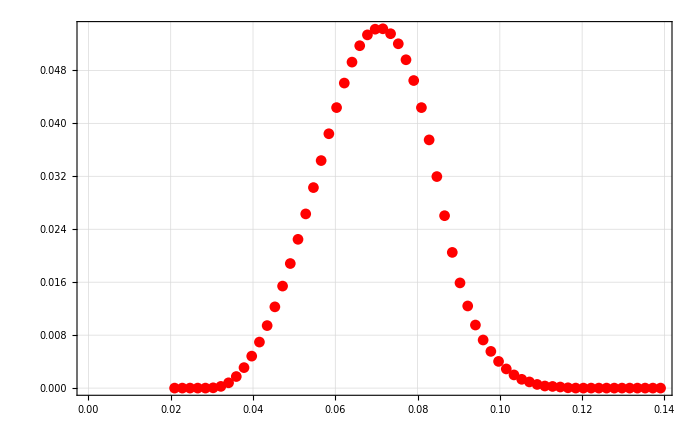

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]]}]];
```

## a=-0.1045

```mathematica
drASubFileNamesa10451DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormalSA=Flatten[Table[Import[drASubFileNamesa10451DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormalSA]}],1];
```

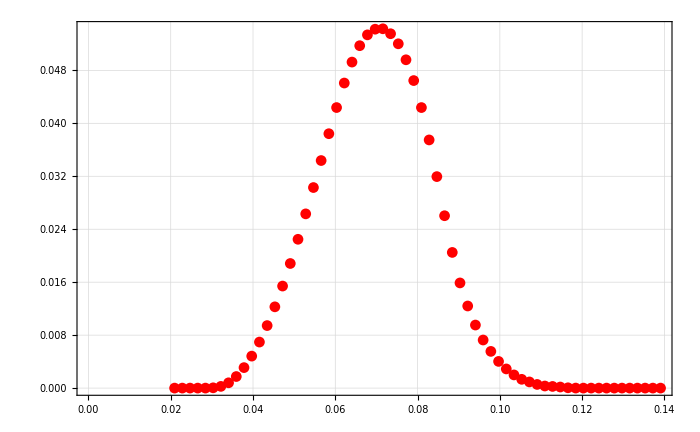

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1045Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa01DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormalSA=Flatten[Table[Import[drASubFileNamesa01DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormalSA]}],1];
```

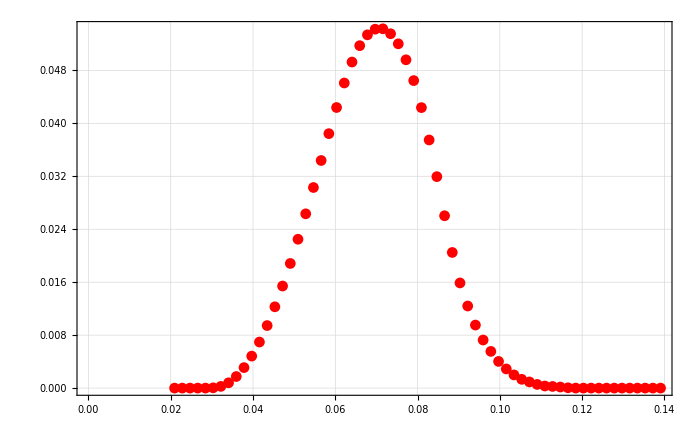

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drASpectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa10551DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormalSA=Flatten[Table[Import[drASubFileNamesa10551DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNormalSA]}],1];
```

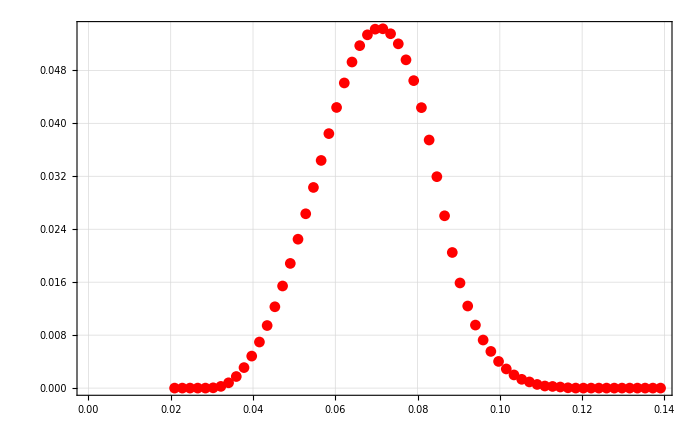

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa10601DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormalSA=Flatten[Table[Import[drASubFileNamesa10601DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormalSA]}],1];
```

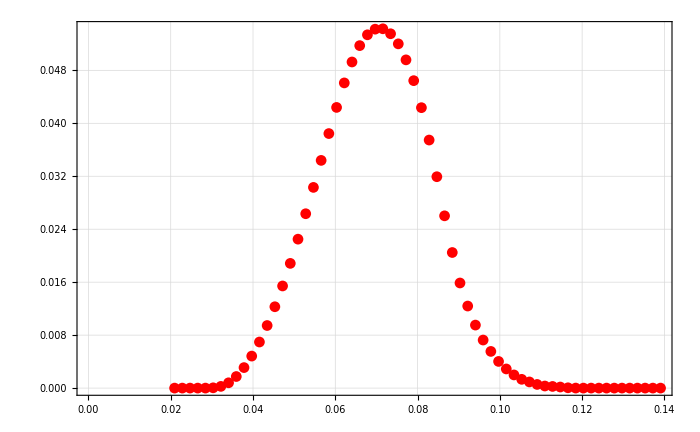

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

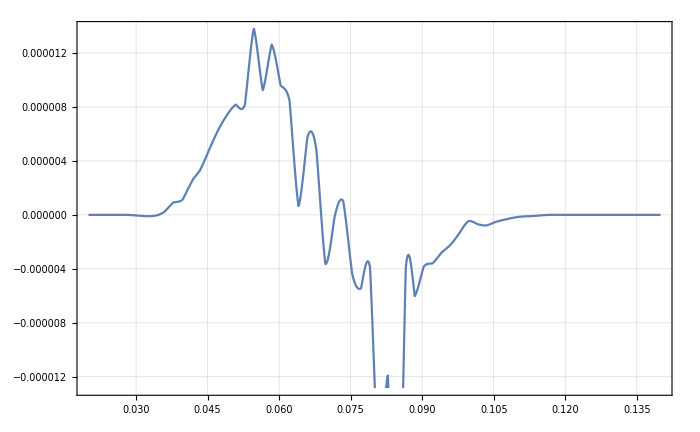

```mathematica
Show[Plot[drAa1060Spectrum1DNormalSAInter[x]-da0Spectrum1DNormalSAInter[x],{x,0.02,0.14}]]
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

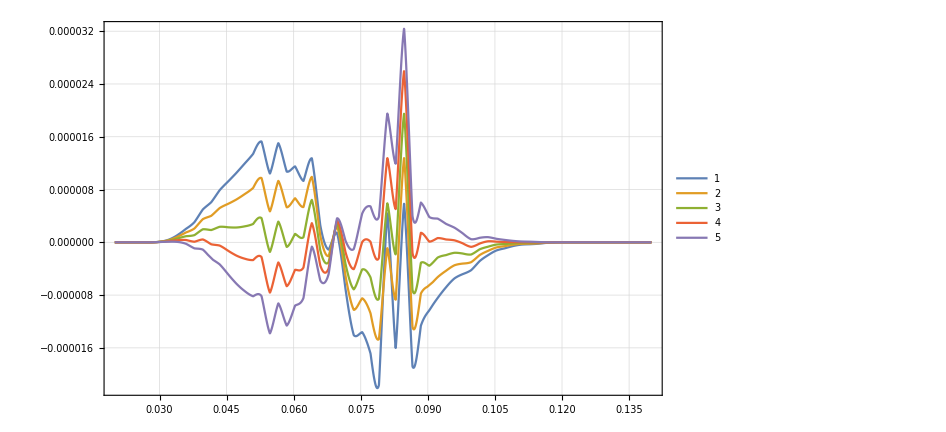

```mathematica
Plot[{
da0Spectrum1DNormalSAInter[x]-drAa1040Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1045Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drASpectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1055Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1060Spectrum1DNormalSAInter[x]
}
,{x,0.02,0.14},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormalSA[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{4.05433×10^-9,1.80424×10^-9,8.24069×10^-10,1.113×10^-9,2.67759×10^-9},{3.29806×10^-10,2.22066×10^-10,1.51354×10^-10,1.6868×10^-10,2.56526×10^-10}},a0 =  | -0.105136
FittedModel[7.76703×10^-10+0.0025424 (0.105136+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105136 | 0.0000335187 | -3136.62 | 1.01643×10^-7
scale | 0.0025424 | 0.000252905 | 10.0528 | 0.00975073
yoffset | 7.76703×10^-10 | 1.16833×10^-10 | 6.64796 | 0.0218867 | 
 | DF | SS | MS
Model | 3 | 399.263 | 133.088
Error | 2 | 0.000112978 | 0.0000564888
Uncorrected Total | 5 | 399.264 | 
Corrected Total | 4 | 107.983 |  | ,-Graphics-}

```mathematica
((-0.1051356022629343+0.105)/-0.105)/(10^-4)
```

12.9145

```mathematica
71*.97
```

68.87

```mathematica
69/71.
```

0.971831

```mathematica
?rG
```

```mathematica
0.13-0.03
```

0.1

```mathematica
0.1/5
```

0.02

```mathematica
4*rG[pmax,45*Pi/180,0.22]+Dr
```

0.0509163

```mathematica
rG[pmax,45*Pi/180,0.976]
```

0.00286926

```mathematica
0.012+0.012
```

0.024

```mathematica
Solve[0.024/x==0.1/5,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.2}}

```mathematica
Solve[0.0028692566237112946/x==rG[pmax,45*Pi/180,0.22]/10,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→2.2541}}

```mathematica
Solve[0.0028692566237112946/x==rG[pmax,45*Pi/180,0.22]/5,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.12705}}

# Diff Neutron Beam prof

## da0 Big 1D xAASC=3.5/1000; yAASC=35/1000;

## da0 Needle3 1D, xaoffset=1cm, 1mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle3/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle3=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle3=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle3[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle3]}],1];
```

```mathematica
xStart=0.01;
xEnd=0.03;
yStart=-0.022;
yEnd=0.025;
xyBins1D3=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D3=BinCenters[xyBins1D3];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D3[[All,1]],d0Spectruma01DdiffAptNeedle3[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
xAOffSC=10/1000;
yAOffSC=0;
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.001, 0.0009, 0.9, 0., -0.9, 0.001, 0.0009, 0.9, 0., -0.9}
```

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle5 1D, xoffset=3cm, 5mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle5/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle5=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle5=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle5[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle5]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D5=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D5=BinCenters[xyBins1D5];
```

```mathematica
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.005, 0.004, 0.9, 0., -0.9, 0.005, 0.004, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]/d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]-d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Blue]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]/Total[d0Spectruma01DdiffAptNeedle5[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle6 1D, xoffset=-3cm, 1mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle6/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle6=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle6=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle6[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle6]}],1];
```

```mathematica
xStart=-0.03;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins1D6=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D6=BinCenters[xyBins1D6];
```

```mathematica
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.005, 0.004, 0.9, 0., -0.9, 0.005, 0.004, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D6[[All,1]],d0Spectruma01DdiffAptNeedle6[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle7 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle7/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle7=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle7=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle7[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle7]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D7=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D7=BinCenters[xyBins1D7];
```

```mathematica
0.06177146861111111+0.13738727291666666+0.21866247808333333+0.3541043168611111+0.4519762369722222+0.2981603826388889+0.13800345402777778+0.08953022125000001
```

1.7496

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Table[Timing[TrapezNBeamCompiledNormed[i,{0.06,0.059,0.9,0.,-0.9}]],{i,0.0,0.06,0.01}]
```

{{0.000028,16.8067},{5.×10^-6,16.8067},{5.×10^-6,16.8067},{4.×10^-6,0.},{4.×10^-6,0.},{3.×10^-6,0.},{3.×10^-6,0.}}

```mathematica
Table[Timing[TrapezNBeamNewNormed[i,{0.06,0.059,0.9,0.,-0.9}]],{i,0.0,0.06,0.01}]
```

{{0.017136,16.8067},{0.000038,16.8067},{0.000023,16.8067},{0.000021,0.},{0.00002,0.},{0.000018,0.},{0.000018,0.}}

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?TrapezNBeamCompiledNormed
```

## da0 Needle4 1D, xoffset=-1cm, 1mm beam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle4/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle4=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle4=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle4[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle4]}],1];
```

```mathematica
xStart=-0.01;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins1D4=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D4=BinCenters[xyBins1D4];
```

```mathematica
d0Spectruma01DdiffAptNeedle2[[All,2]]
```

{0.00236395,0.00531286,0.0100694,0.0170597,0.026696,0.0393775,0.0554899,0.0753921,0.0994249,0.12785,0.160658,0.197679,0.238598,0.283203,0.331096,0.381891,0.435307,0.490753,0.547889,0.606072,0.664797,0.722985,0.78086,0.837483,0.890444,0.941165,0.986064,1.02583,1.05885,1.08401,1.10048,1.10761,1.10533,1.09289,1.07055,1.0383,0.996428,0.945072,0.88512,0.819186,0.749028,0.676403,0.602919,0.530024,0.459441,0.392242,0.329932,0.273584,0.224449,0.182809,0.1483,0.119579,0.0954517,0.0753004,0.0579229,0.0440905,0.0329707,0.0240749,0.0171271,0.0117737,0.00775348,0.00484865,0.00282879,0.00151164}

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D4[[All,1]],d0Spectruma01DdiffAptNeedle4[[All,2]]/Total[d0Spectruma01DdiffAptNeedle4[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
xAOffSC=-10/1000;
yAOffSC=0;
{wnxSC,pnxSC,kx1SC,kx2SC,kx3SC,wnySC,pnySC,ky1SC,ky2SC,ky3SC}={0.001,0.0009,0.9,0.,-0.9,0.001,0.0009,0.9,0.,-0.9}
```

## da0 Needle2 1D xoffset=3cm, 1cm Beam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle2/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle2=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle2[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle2]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
d0Spectruma01DdiffAptNeedle2[[All,2]]
```

{0.00236395,0.00531286,0.0100694,0.0170597,0.026696,0.0393775,0.0554899,0.0753921,0.0994249,0.12785,0.160658,0.197679,0.238598,0.283203,0.331096,0.381891,0.435307,0.490753,0.547889,0.606072,0.664797,0.722985,0.78086,0.837483,0.890444,0.941165,0.986064,1.02583,1.05885,1.08401,1.10048,1.10761,1.10533,1.09289,1.07055,1.0383,0.996428,0.945072,0.88512,0.819186,0.749028,0.676403,0.602919,0.530024,0.459441,0.392242,0.329932,0.273584,0.224449,0.182809,0.1483,0.119579,0.0954517,0.0753004,0.0579229,0.0440905,0.0329707,0.0240749,0.0171271,0.0117737,0.00775348,0.00484865,0.00282879,0.00151164}

```mathematica
xAASC=3.5/1000;
yAASC=35/1000;
xAOffSC=30/1000;
yAOffSC=0;
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.01, 0.009, 0.9, 0., -0.9, 0.01, 0.009, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptNeedle2[[All,2]]/Total[d0Spectruma01DdiffAptNeedle2[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,0.9]
```

0.0124462

```mathematica
0.02-4rG[pmax,45*Pi/180,0.9]
```

0.0075538

## da0 Needle 1D xAASC=3.5/1000; yAASC=35/1000;

```mathematica
?TrapezNBeamCompiledNormed
```

```mathematica
TrapezNBeamCompiledNormed[0.002,{0.5,0.49,0.9,0.,-0.9}]
```

2.0202

```mathematica
nplot=Plot[TrapezNBeamCompiledNormed[xn,{0.5,0.49,0.9,0.,-0.9}],{xn,-0.5,0.5},ImageSize->800,GridLines->Automatic,Frame->True,FrameStyle->25,FrameLabel->{{"n_x(x)",None},{"x (mm)",None}}]
```

-Graphics-

```mathematica
Plot[TrapezNBeamNewNormed[i,{6/100,5.9/100,0.9,0.,-0.9}],{i,-10/100,10/100}]
```

-Graphics-

```mathematica
nplot=Plot[TrapezNBeamNewNormed[xn,{1,0.9,0.9,0.,-0.9}],{xn,-10,10},ImageSize->800,GridLines->Automatic,Frame->True,FrameStyle->25,FrameLabel->{{"n_x(x)",None},{"x (mm)",None}}]
```

-Graphics-

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
d0Spectruma01DdiffAptNeedle[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.12258,1.06402,1.00601,0.985874,0.914519,0.,0.,0.,0.627583,0.,0.,0.,0.,0.301889,0.206574,0.13549,0.0835913,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptNeedle[[All,2]]/Total[d0Spectruma01DdiffAptNeedle[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,0.9]
```

0.0124462

```mathematica
0.02-4rG[pmax,45*Pi/180,0.9]
```

0.0075538

## da0 Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm2/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffApt=Flatten[Table[Import[d0SubFileNamesa01DdiffApt[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffApt]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]-d0Spectruma01DdiffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## drA Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1050/"];
```

```mathematica
drASubFileNamesa0diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_57-64.txt}

```mathematica
drASpectruma0diffApt=Flatten[Table[Import[drASubFileNamesa0diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa0diffApt]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma0diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1040/"];
```

```mathematica
drASubFileNamesa1040diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_57-64.txt}

```mathematica
drASpectruma1040diffApt=Flatten[Table[Import[drASubFileNamesa1040diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1040diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1040diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1045/"];
```

```mathematica
drASubFileNamesa1045diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_57-64.txt}

```mathematica
drASpectruma1045diffApt=Flatten[Table[Import[drASubFileNamesa1045diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1045diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1045diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1055/"];
```

```mathematica
drASubFileNamesa1055diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_57-64.txt}

```mathematica
drASpectruma1055diffApt=Flatten[Table[Import[drASubFileNamesa1055diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1055diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1055diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1060/"];
```

```mathematica
drASubFileNamesa1060diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_57-64.txt}

```mathematica
drASpectruma1060diffApt=Flatten[Table[Import[drASubFileNamesa1060diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1060diffApt]}],1];
```

```mathematica
RefSpectrumInterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]/Total[d0Spectruma01DdiffApt[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInterdiffApt[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma0diffApt[[All,2]]/Total[drASpectruma0diffApt[[All,2]]]}]];drASpectruma1040InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1040diffApt[[All,2]]/Total[drASpectruma1040diffApt[[All,2]]]}]];
drASpectruma1045InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1045diffApt[[All,2]]/Total[drASpectruma1045diffApt[[All,2]]]}]];
drASpectruma1055InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1055diffApt[[All,2]]/Total[drASpectruma1055diffApt[[All,2]]]}]];
drASpectruma1060InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1060diffApt[[All,2]]/Total[drASpectruma1060diffApt[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055InterdiffApt[x]-drASpectruma1045InterdiffApt[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
RefSpectrumInterdiffApt[x]-drASpectruma1040InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1045InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1055InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1060InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma0InterdiffApt[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma1040diffApt[[All,2]]/Total[drASpectruma1040diffApt[[All,2]]],drASpectruma1045diffApt[[All,2]]/Total[drASpectruma1045diffApt[[All,2]]],drASpectruma0diffApt[[All,2]]/Total[drASpectruma0diffApt[[All,2]]],drASpectruma1055diffApt[[All,2]]/Total[drASpectruma1055diffApt[[All,2]]],drASpectruma1060diffApt[[All,2]]/Total[drASpectruma1060diffApt[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01DdiffBeam[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0451×10^-8,6.8821×10^-9,4.11926×10^-9,2.17477×10^-9,1.02969×10^-9},{3.45933×10^-10,2.75173×10^-10,2.05032×10^-10,1.36219×10^-10,7.24851×10^-11}},a0 =  | -0.106449
FittedModel[7.07044×10^-10+0.00162055 (0.106449+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106449 | 0.00015402 | -691.143 | 2.09345×10^-6
scale | 0.00162055 | 0.00020177 | 8.0317 | 0.0151505
yoffset | 7.07044×10^-10 | 2.25201×10^-10 | 3.13962 | 0.0882291 | 
 | DF | SS | MS
Model | 3 | 2398.52 | 799.506
Error | 2 | 0.0150241 | 0.00751207
Uncorrected Total | 5 | 2398.53 | 
Corrected Total | 4 | 1198.89 |  | ,-Graphics-}

```mathematica
-0.1064494958980962
```

```mathematica
((-0.10644322321394499+0.105)/-0.105)
```

0.013745

```mathematica
0.013744982989952324*100
```

1.3745

```mathematica
10^-4*138.337
```

0.0138337

```mathematica
((-0.10644322321394499+0.105)/-0.105)/(10^-4)
```

137.45

```mathematica
((-0.1064494958980962+0.105)/-0.105)/(10^-4)
```

138.047

```mathematica
137.44982989952325*.106*10^-3
```

0.0145697

```mathematica
157.04*.106
```

16.6462

```mathematica
drASpectruma035mm[[All,2]]
```

{0.000109634,0.000244689,0.000461022,0.000777311,0.00121209,0.00178335,0.00250818,0.00340211,0.00448043,0.00575471,0.00722558,0.00888494,0.0107228,0.0127285,0.0148913,0.0171929,0.0196195,0.022156,0.024777,0.027458,0.0301701,0.0328825,0.0355405,0.0380881,0.0404864,0.0426895,0.0446593,0.0463404,0.047715,0.0487313,0.0493775,0.0496077,0.0494096,0.0487506,0.0476734,0.0461343,0.0441637,0.0417732,0.0390237,0.0360036,0.0328265,0.0295548,0.0262664,0.0230373,0.019903,0.0169486,0.0142265,0.0117794,0.00965522,0.00786194,0.00637475,0.00513286,0.00406537,0.00319984,0.00248339,0.00189357,0.00141485,0.00103349,0.000733169,0.000503669,0.000333821,0.000211115,0.000125457,0.0000691001}

```mathematica
normed2mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}];
```

```mathematica
normed10mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]/Total[-drASpectruma010mm[[All,2]]]}];
```

```mathematica
normed35mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}];
```

```mathematica
normed35a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}];
```

```mathematica
normed10a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}];
```

```mathematica
normed2mma0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed2mma0[[All,2]]-normed2mmrA[[All,2]]}],PlotStyle->Blue],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed35a0[[All,2]]-normed35mmrA[[All,2]]}],PlotStyle->Red],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed10a0[[All,2]]-normed10mmrA[[All,2]]}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Show[Plot[RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x],{x,0.03,0.05},PlotStyle->Blue],
Plot[RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x],{x,0.03,0.05},PlotStyle->Red],
Plot[RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

# Diff Aperture

## da0 shifted0 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
d0SubFileNamesa01Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_shifted0/a-1050/"];
```

```mathematica
d0Spectruma01Dshifted0=Flatten[Table[Import[d0SubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Dshifted0]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.008;
yStart=-0.022;
yEnd=0.025;
xyBins1Dshifted0=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
?bin2DGen
```

```mathematica
XYBinCentersYHalf1DShifted0=BinCenters[xyBins1Dshifted0];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],d0Spectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DShifted0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],d0Spectruma01Dshifted0[[All,2]]/Total[d0Spectruma01Dshifted0[[All,2]]]}]];
```

## drA shifted0 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
drASubFileNamesa01Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_57-64.txt}

```mathematica
drASpectruma01Dshifted0=Flatten[Table[Import[drASubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa01Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## a=-0.104

```mathematica
drASubFileNamesa10401Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_57-64.txt}

```mathematica
drASpectruma10401Dshifted0=Flatten[Table[Import[drASubFileNamesa10401Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401Dshifted0]}],1];
```

```mathematica
drASpectruma10401Dshifted0//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10401Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
f2=Import["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/Old/TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1045_9*","Table"];
```

```mathematica
f2[[1,All,2]]
```

{0.00276363,0.00378161,0.0050171,0.00648566,0.00819611,0.0102033,0.0123796,0.0147684}

```mathematica
drASpectruma10451Dshifted0[[All,2]]
```

{4.31993×10^-6,0.0000290117,0.0000996045,0.000239182,0.000471039,0.00081791,0.00130187,0.00194347,0.00276363,0.00378161,0.0050171,0.00648566,0.00819611,0.0102033,0.0123796,0.0147684,0.0173553,0.0201244,0.023059,0.0261369,0.0293306,0.0326183,0.0359609,0.039303,0.042621,0.046477,0.0495702,0.0519479,0.0549908,0.0567179,0.0585672,0.0600057,0.0609857,0.0614794,0.0614434,0.0608814,0.059767,0.058091,0.055871,0.052912,0.0497015,0.046112,0.042254,0.0382613,0.0342057,0.0301793,0.0262604,0.0225211,0.0192631,0.0160543,0.013235,0.0108233,0.0088023,0.00700955,0.00562929,0.00446651,0.00349571,0.00269307,0.0020365,0.00150711,0.00108771,0.000763275,0.000517229,0.000338725}

```mathematica
drASubFileNamesa10451Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_57-64.txt}

```mathematica
drASpectruma10451Dshifted0=Flatten[Table[Import[drASubFileNamesa10451Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10451Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectruma10451Dshifted0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10451Dshifted0[[All,2]]/Total[drASpectruma10451Dshifted0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
drASubFileNamesa10551Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_57-64.txt}

```mathematica
drASpectruma10551Dshifted0=Flatten[Table[Import[drASubFileNamesa10551Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10551Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1Da1055Shifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10551Dshifted0[[All,2]]/Total[drASpectruma10551Dshifted0[[All,2]]]}]];
```

## a=-0.106

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1060/"];
```

```mathematica
drASubFileNamesa10601Dshifted0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_57-64.txt}

```mathematica
drASpectruma01Dshifted0=Flatten[Table[Import[drASubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa01Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,drADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401Dshifted0[[All,2]]/Total[drASpectruma10401Dshifted0[[All,2]]],drASpectruma10451Dshifted0[[All,2]]/Total[drASpectruma10451Dshifted0[[All,2]]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]],drASpectruma10551Dshifted0[[All,2]]/Total[drASpectruma10551Dshifted0[[All,2]]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
TransferToRefParableFitForProtons[RefTransfer_,TransferDataList_,ParaList_,Prec_]:=Module[{RefNorm=Total[RefTransfer],RefNormed,Sigma,TransferDataListNormed,Chi2List,dChi2List,errorplotdata,fitresult,fitfunc,bMin,bMax},bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01Dshifted0[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.68711×10^-7,2.66514×10^-7,1.59802×10^-7,1.57437×10^-7,1.59802×10^-7},{2.22297×10^-9,2.21909×10^-9,1.55562×10^-9,1.54192×10^-9,1.55562×10^-9}},a0 =  | -0.105729
FittedModel[1.54117×10^-7+0.0440443 (0.105729+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105729 | 0.0000314458 | -3362.25 | 8.84586×10^-8
scale | 0.0440443 | 0.00187893 | 23.4412 | 0.00181492
yoffset | 1.54117×10^-7 | 1.00436×10^-9 | 153.447 | 0.0000424671 | 
 | DF | SS | MS
Model | 3 | 59947.6 | 19982.5
Error | 2 | 618.972 | 309.486
Uncorrected Total | 5 | 60566.6 | 
Corrected Total | 4 | 3610.96 |  | ,-Graphics-}

```mathematica
((-0.10572859624129084+0.105)/-0.105)/(10^-4)
```

69.3901

```mathematica
(bA/bdv)/(brxb/bdv)
```

bA/brxb

```mathematica
Sqrt[1/2]==Sqrt[1]/Sqrt[2]
```

True

```mathematica
Simplify[1/Sqrt[1/2]]
```

√2

## da0 shifted 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_shiftedApt/a-1050/"];
```

```mathematica
d0SubFileNamesa01DshiftedApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_57-64.txt}

```mathematica
d0Spectruma01DshiftedApt=Flatten[Table[Import[d0SubFileNamesa01DshiftedApt[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DshiftedApt]}],1];
```

```mathematica
xStart=-0.022;
xEnd=-0.002;
yStart=-0.022;
yEnd=0.025;
xyBins1Dshifted=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DShifted=BinCenters[xyBins1Dshifted];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]]-0.05,d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]]-0.0516,d0Spectruma01D35mm2[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptBig[[All,2]]}],PlotStyle->Red]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptBig[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 35mm2 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D35mm2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D35mm2=Flatten[Table[Import[d0SubFileNamesa01D35mm2[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D35mm2]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/d0Spectruma01D35mm[[All,2]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/1.244}]],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mm2[[All,2]]-d0Spectruma01DdiffAptNeedle7[[All,2]])/d0Spectruma01D35mm2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]}]],ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]-d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]])/(d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]])}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]-d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1D35mm2=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=2/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D2mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D2mm=Flatten[Table[Import[d0SubFileNamesa01D2mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1D2mmInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a1050/"];
```

```mathematica
d0SubFileNamesa01D2mma1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_57-64.txt}

```mathematica
d0Spectruma01D2mma1050=Flatten[Table[Import[d0SubFileNamesa01D2mma1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mma1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D2mma1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1D2mmIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mma1050[[All,2]]/Total[d0Spectruma01D2mma1050[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=4/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D4mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D4mm=Flatten[Table[Import[d0SubFileNamesa01D4mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D4mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D4mm[[All,2]]}]]
```

-Graphics-

```mathematica
d0Spectruma01D4mm[[All,2]]
```

{-0.000216332,-0.000417411,-0.000715287,-0.00112842,-0.00167508,-0.0023725,-0.00323646,-0.00428214,-0.00552322,-0.00697207,-0.00863762,-0.010515,-0.0125944,-0.0148635,-0.0173064,-0.0199071,-0.02265,-0.0255144,-0.0284588,-0.0314697,-0.0345064,-0.0375234,-0.0404549,-0.0432631,-0.0458957,-0.0483093,-0.0504556,-0.0523012,-0.0537939,-0.0549072,-0.0555969,-0.0558407,-0.0555885,-0.0548316,-0.0535904,-0.051826,-0.0495936,-0.0469195,-0.0438957,-0.0406302,-0.0372054,-0.0336948,-0.0301521,-0.0266518,-0.0232365,-0.0199789,-0.0169181,-0.0141342,-0.0116471,-0.0095032,-0.00771046,-0.00622339,-0.00498641,-0.00393215,-0.00307441,-0.00237368,-0.00180097,-0.00134024,-0.000973584,-0.000685355,-0.000469192,-0.000308437,-0.000192944,-0.000113361}

```mathematica
da0Spectrum1DInter4mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mm[[All,2]]/Total[d0Spectruma01D4mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_4mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da10504mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_57-64.txt}

```mathematica
d0Spectruma01D4mma1050=Flatten[Table[Import[d0SubFileNamesa01Da10504mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da10504mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

1/16 Total[Symbol[]]

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mma1050[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DInter4mma1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mma1050[[All,2]]/Total[d0Spectruma01D4mma1050[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a-1050/"];
```

```mathematica
d0SubFileNamesa01D=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_57-64.txt}

```mathematica
d0Spectruma01D=Flatten[Table[Import[d0SubFileNamesa01D[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a1050/"];
```

```mathematica
d0SubFileNamesa01Da1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_57-64.txt}

```mathematica
d0Spectruma01Da1050=Flatten[Table[Import[d0SubFileNamesa01Da1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]/Total[d0Spectruma01Da1050[[All,2]]]}]];
```

## drA Smaller 1D xAASC=10/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1050/"];
```

```mathematica
drASubFileNamesa010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_57-64.txt}

```mathematica
drASpectruma010mm=Flatten[Table[Import[drASubFileNamesa010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa010mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1040/"];
```

```mathematica
drASubFileNamesa104010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_57-64.txt}

```mathematica
drASpectruma104010mm=Flatten[Table[Import[drASubFileNamesa104010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104010mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104010mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1045/"];
```

```mathematica
drASubFileNamesa104510mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_57-64.txt}

```mathematica
drASpectruma104510mm=Flatten[Table[Import[drASubFileNamesa104510mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104510mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104510mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1055/"];
```

```mathematica
drASubFileNamesa105510mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_57-64.txt}

```mathematica
drASpectruma105510mm=Flatten[Table[Import[drASubFileNamesa105510mm[[i]],"Table"],{i,1,Length[drASubFileNamesa105510mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105510mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1060/"];
```

```mathematica
drASubFileNamesa106010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_57-64.txt}

```mathematica
drASpectruma106010mm=Flatten[Table[Import[drASubFileNamesa106010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa106010mm]}],1];
```

```mathematica
RefSpectrumInter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter10mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma010mm[[All,2]]/Total[drASpectruma010mm[[All,2]]]}]];drASpectruma1040Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104010mm[[All,2]]/Total[drASpectruma104010mm[[All,2]]]}]];
drASpectruma1045Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104510mm[[All,2]]/Total[drASpectruma104510mm[[All,2]]]}]];
drASpectruma1055Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105510mm[[All,2]]/Total[drASpectruma105510mm[[All,2]]]}]];
drASpectruma1060Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106010mm[[All,2]]/Total[drASpectruma106010mm[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055Inter10mm[x]-drASpectruma1045Inter10mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
RefSpectrumInter10mm[x]-drASpectruma1040Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1045Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1055Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1060Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
drASpectruma104035mmRemv=Join[drASpectruma104035mm[[All,2]][[1;;51]],drASpectruma104035mm[[All,2]][[53;;]]];drASpectruma104535mmRemv=Join[drASpectruma104535mm[[All,2]][[1;;51]],drASpectruma104535mm[[All,2]][[53;;]]];
drASpectruma105035mmRemv=Join[drASpectruma035mm[[All,2]][[1;;51]],drASpectruma035mm[[All,2]][[53;;]]];
drASpectruma105535mmRemv=Join[drASpectruma105535mm[[All,2]][[1;;51]],drASpectruma105535mm[[All,2]][[53;;]]];drASpectruma106035mmRemv=Join[drASpectruma106035mm[[All,2]][[1;;51]],drASpectruma106035mm[[All,2]][[53;;]]];
refSpectra35mmRemv=Join[d0Spectruma01D35mm[[All,2]][[1;;51]],d0Spectruma01D35mm[[All,2]][[53;;]]];
```

```mathematica
ListPlot[drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}],Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]},PlotRange->All]
```

-Graphics-

```mathematica
97*.1
```

9.7

```mathematica
0.0097*100
```

0.97

```mathematica
ListPlot[{d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList2={drASpectruma104035mmRemv/Total[drASpectruma104035mmRemv],drASpectruma104535mmRemv/Total[drASpectruma104535mmRemv],drASpectruma105035mmRemv/Total[drASpectruma105035mmRemv],drASpectruma105535mmRemv/Total[drASpectruma105535mmRemv],drASpectruma106035mmRemv/Total[drASpectruma106035mmRemv]};
```

```mathematica
drADataList={drASpectruma104010mm[[All,2]]/Total[drASpectruma104010mm[[All,2]]],drASpectruma104510mm[[All,2]]/Total[drASpectruma104510mm[[All,2]]],drASpectruma010mm[[All,2]]/Total[drASpectruma010mm[[All,2]]],drASpectruma105510mm[[All,2]]/Total[drASpectruma105510mm[[All,2]]],drASpectruma106010mm[[All,2]]/Total[drASpectruma106010mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D10mm[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.72851×10^-9,2.46631×10^-9,1.47745×10^-9,7.64573×10^-10,3.06681×10^-10},{1.46972×10^-10,1.2088×10^-10,9.55324×10^-11,7.15814×10^-11,4.98497×10^-11}},a0 =  | -0.106511
FittedModel[1.66409×10^-10+0.000568555 (0.106511+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106511 | 0.000235605 | -452.073 | 4.89304×10^-6
scale | 0.000568555 | 0.0000984328 | 5.77607 | 0.0286897
yoffset | 1.66409×10^-10 | 1.43995×10^-10 | 1.15566 | 0.36723 | 
 | DF | SS | MS
Model | 3 | 1450.85 | 483.616
Error | 2 | 0.126455 | 0.0632274
Uncorrected Total | 5 | 1450.98 | 
Corrected Total | 4 | 718.459 |  | ,-Graphics-}

```mathematica
((-0.10651082268604328+0.105)/-0.105)
```

0.0143888

```mathematica
0.014388787486126538*100
```

1.43888

```mathematica
((-0.10651082268604328+0.105)/-0.105)/(10^-4)
```

143.888

## drA Smaller 1D xAASC=2/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1050/"];
```

```mathematica
drASubFileNamesa02mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_57-64.txt}

```mathematica
drASpectruma02mm=Flatten[Table[Import[drASubFileNamesa02mm[[i]],"Table"],{i,1,Length[drASubFileNamesa02mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1040/"];
```

```mathematica
drASubFileNamesa10402mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_57-64.txt}

```mathematica
drASpectruma10402mm=Flatten[Table[Import[drASubFileNamesa10402mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10402mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma10402mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1045/"];
```

```mathematica
drASubFileNamesa10452mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_57-64.txt}

```mathematica
drASpectruma10452mm=Flatten[Table[Import[drASubFileNamesa10452mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10452mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10452mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1055/"];
```

```mathematica
drASubFileNamesa10552mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_57-64.txt}

```mathematica
drASpectruma10552mm=Flatten[Table[Import[drASubFileNamesa10552mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10552mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10552mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1060/"];
```

```mathematica
drASubFileNamesa10602mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_57-64.txt}

```mathematica
drASpectruma10602mm=Flatten[Table[Import[drASubFileNamesa10602mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10602mm]}],1];
```

```mathematica
RefSpectrumInter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter2mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}]];drASpectruma1040Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10402mm[[All,2]]/Total[drASpectruma10402mm[[All,2]]]}]];
drASpectruma1045Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10452mm[[All,2]]/Total[drASpectruma10452mm[[All,2]]]}]];
drASpectruma1055Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10552mm[[All,2]]/Total[drASpectruma10552mm[[All,2]]]}]];
drASpectruma1060Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10602mm[[All,2]]/Total[drASpectruma10602mm[[All,2]]]}]];
```

```mathematica
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]-drASpectruma02mm[[All,2]]}]]
```

-Graphics-

```mathematica
Show[Plot[drASpectruma1055Inter2mm[x]-drASpectruma1045Inter2mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
thirtyfiveDiff=Plot[{
RefSpectrumInter35mm[x]-drASpectruma1040Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1045Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1055Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1060Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tenmmDiff=Plot[{
RefSpectrumInter10mm[x]-drASpectruma1040Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1045Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1055Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1060Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
twommDiff=Plot[{
RefSpectrumInter2mm[x]-drASpectruma1040Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1045Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1055Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1060Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
imageWrite[twommDiff];imageWrite[tenmmDiff];imageWrite[thirtyfiveDiff];
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10402mm[[All,2]]/Total[drASpectruma10402mm[[All,2]]],drASpectruma10452mm[[All,2]]/Total[drASpectruma10452mm[[All,2]]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]],drASpectruma10552mm[[All,2]]/Total[drASpectruma10552mm[[All,2]]],drASpectruma10602mm[[All,2]]/Total[drASpectruma10602mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D2mm[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.1211×10^-8,7.21606×10^-9,4.15507×10^-9,2.22615×10^-9,9.30743×10^-10},{3.68964×10^-10,2.91435×10^-10,2.16017×10^-10,1.54344×10^-10,1.01924×10^-10}},a0 =  | -0.106416
FittedModel[6.34165×10^-10+0.00179091 (0.106416+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106416 | 0.000155452 | -684.555 | 2.13394×10^-6
scale | 0.00179091 | 0.000225641 | 7.93696 | 0.0155059
yoffset | 6.34165×10^-10 | 2.59716×10^-10 | 2.44176 | 0.13466 | 
 | DF | SS | MS
Model | 3 | 2197.16 | 732.388
Error | 2 | 0.577262 | 0.288631
Uncorrected Total | 5 | 2197.74 | 
Corrected Total | 4 | 1117.84 |  | ,-Graphics-}

```mathematica
err={{3.1928781315237865*^-6,3.231480211902923*^-6,3.270832502237184*^-6,3.3105244265165438*^-6,3.3502556708866684*^-6},{5.628069399000864*^-9,5.666363422511431*^-9,5.704809601381051*^-9,5.742886499101549*^-9,5.781153327827049*^-9}}
```

{{3.19288×10^-6,3.23148×10^-6,3.27083×10^-6,3.31052×10^-6,3.35026×10^-6},{5.62807×10^-9,5.66636×10^-9,5.70481×10^-9,5.74289×10^-9,5.78115×10^-9}}

```mathematica
errList=Table[Around[err[[1,i]],err[[2,i]]],{i,Length[err[[1]]]}]
```

{3.1930.00610^-6,3.2310.00610^-6,3.2710.00610^-6,3.3110.00610^-6,3.3500.00610^-6}

```mathematica
errData=Transpose[{{-0.0015,-0.00075,0.,0.00075,0.0015},err[[1]]}]
```

{{-0.0015,3.19288×10^-6},{-0.00075,3.23148×10^-6},{0.,3.27083×10^-6},{0.00075,3.31052×10^-6},{0.0015,3.35026×10^-6}}

```mathematica
err[[1]]
```

{3.19288×10^-6,3.23148×10^-6,3.27083×10^-6,3.31052×10^-6,3.35026×10^-6}

```mathematica
lm=LinearModelFit[errData,{1,x},x,Weights->1/err[[2]]^2]
```

FittedModel[3.27119×10^-6+0.0000525019 x]

```mathematica
linearFitrAFierz=Show[Plot[lm[x],{x,-0.0015,0.0015},PlotStyle->Red],ListPlot[Transpose[{{-0.0015,-0.00075,0.,0.00075,0.0015},errList}]]]
```

-Graphics-

```mathematica
imageWrite[linearFitrAFierz]
```

```mathematica
((-0.10641564931594331+0.105)/-0.105)
```

0.0134824

```mathematica
0.014388787486126538*100
```

1.43888

```mathematica
((-0.10641564931594331+0.105)/-0.105)/(10^-4)
```

134.824

## drA Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1050/"];
```

```mathematica
drASubFileNamesa035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_57-64.txt}

```mathematica
drASpectruma035mm=Flatten[Table[Import[drASubFileNamesa035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa035mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1040/"];
```

```mathematica
drASubFileNamesa104035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_57-64.txt}

```mathematica
drASpectruma104035mm=Flatten[Table[Import[drASubFileNamesa104035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104035mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104035mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1075/"];
```

```mathematica
drASubFileNamesa107535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_57-64.txt}

```mathematica
drASpectruma107535mm=Flatten[Table[Import[drASubFileNamesa107535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa107535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma107535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1045/"];
```

```mathematica
drASubFileNamesa104535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_57-64.txt}

```mathematica
drASpectruma104535mm=Flatten[Table[Import[drASubFileNamesa104535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1055/"];
```

```mathematica
drASubFileNamesa105535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_57-64.txt}

```mathematica
drASpectruma105535mm=Flatten[Table[Import[drASubFileNamesa105535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa105535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1060/"];
```

```mathematica
drASubFileNamesa106035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_57-64.txt}

```mathematica
drASpectruma106035mm=Flatten[Table[Import[drASubFileNamesa106035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa106035mm]}],1];
```

```mathematica
RefSpectrumInter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter35mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]];drASpectruma1040Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}]];
drASpectruma1045Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}]];
drASpectruma1055Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]}]];
drASpectruma1060Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055Inter35mm[x]-drASpectruma1045Inter35mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
diffPlot2mm=Plot[{
d0Spectruma0Inter2mm[x]-drASpectruma1040Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1045Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1055Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1060Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

```mathematica
diffPlot2mm=Plot[{
drASpectruma0Inter2mm[x]-drASpectruma1040Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1045Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1055Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1060Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffPlot10mm=Plot[{
drASpectruma0Inter10mm[x]-drASpectruma1040Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1045Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1055Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1060Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffPlot=Plot[{
drASpectruma0Inter35mm[x]-drASpectruma1040Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1045Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1055Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1060Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
imageWrite[diffPlot]
```

```mathematica
imageWrite[diffPlot10mm];imageWrite[diffPlot2mm];
```

```mathematica
|
```

```mathematica
Plot[{
RefSpectrumInter35mm[x]-drASpectruma1040Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1045Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1055Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1060Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
drASpectruma104035mmRemv=Join[drASpectruma104035mm[[All,2]][[1;;51]],drASpectruma104035mm[[All,2]][[53;;]]];drASpectruma104535mmRemv=Join[drASpectruma104535mm[[All,2]][[1;;51]],drASpectruma104535mm[[All,2]][[53;;]]];
drASpectruma105035mmRemv=Join[drASpectruma035mm[[All,2]][[1;;51]],drASpectruma035mm[[All,2]][[53;;]]];
drASpectruma105535mmRemv=Join[drASpectruma105535mm[[All,2]][[1;;51]],drASpectruma105535mm[[All,2]][[53;;]]];drASpectruma106035mmRemv=Join[drASpectruma106035mm[[All,2]][[1;;51]],drASpectruma106035mm[[All,2]][[53;;]]];
refSpectra35mmRemv=Join[d0Spectruma01D35mm[[All,2]][[1;;51]],d0Spectruma01D35mm[[All,2]][[53;;]]];
```

```mathematica
ListPlot[drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}],Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]},PlotRange->All]
```

-Graphics-

```mathematica
97*.1
```

9.7

```mathematica
0.0097*100
```

0.97

```mathematica
diff35mmaValsrA=ListPlot[{d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList2={drASpectruma104035mmRemv/Total[drASpectruma104035mmRemv],drASpectruma104535mmRemv/Total[drASpectruma104535mmRemv],drASpectruma105035mmRemv/Total[drASpectruma105035mmRemv],drASpectruma105535mmRemv/Total[drASpectruma105535mmRemv],drASpectruma106035mmRemv/Total[drASpectruma106035mmRemv]};
```

```mathematica
drADataList={drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]],drASpectruma107535mm[[All,2]]/Total[drASpectruma107535mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1075}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
TransferToRefParableFitForProtons[RefTransfer_,TransferDataList_,ParaList_,Prec_]:=Module[{RefNorm=Total[RefTransfer],RefNormed,Sigma,TransferDataListNormed,Chi2List,dChi2List,errorplotdata,fitresult,fitfunc,bMin,bMax},bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->1000];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
TransferToRefParableFitForProtonsUnlimited
```

TransferToRefParableFitForProtonsUnlimited

```mathematica
chi2List2=Transpose[{bList,{1.0506630519124637*^-8,6.9175548163778236*^-9,4.139569226722818*^-9,2.1850233817621848*^-9,1.0347335648281713*^-9}}]
```

{{-0.104,1.05066×10^-8},{-0.1045,6.91755×10^-9},{-0.105,4.13957×10^-9},{-0.1055,2.18502×10^-9},{-0.106,1.03473×10^-9}}

```mathematica
err={3.493772257773241*^-10,2.779119417135372*^-10,2.070704066129087*^-10,1.3756243875324397*^-10,7.313368896176667*^-11};
```

```mathematica
lm=LinearModelFit[chi2List2,{1,x,x^2},x,Weights->1/err^2]
```

FittedModel[0.0000184315+0.000346262 x+0.00162632 x^2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0000184315 | 4.21784×10^-8 | 436.988 | 5.23669×10^-6
x | 0.000346262 | 8.0154×10^-7 | 431.995 | 5.35844×10^-6
x^2 | 0.00162632 | 3.8079×10^-6 | 427.09 | 5.48224×10^-6

```mathematica
(Re[x/.Solve[lm[x]==0][[1,1]]]+0.105)/-0.105
```

0.0138639

```mathematica
drAInvest2=TransferToRefParableFitForProtonsUnlimited[refSpectra35mmRemv,drADataList2,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.05066×10^-8,6.91755×10^-9,4.13957×10^-9,2.18502×10^-9,1.03473×10^-9},{3.49377×10^-10,2.77912×10^-10,2.0707×10^-10,1.37562×10^-10,7.31337×10^-11}},a0 =  | -0.106443
FittedModel[7.02156×10^-10+0.00165465 (0.106443+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106443 | 0.000151566 | -702.289 | 2.02753×10^-6
scale | 0.00165465 | 0.000203753 | 8.12084 | 0.014827
yoffset | 7.02156×10^-10 | 2.24343×10^-10 | 3.12984 | 0.0887102 | 
 | DF | SS | MS
Model | 3 | 2375.97 | 791.99
Error | 2 | 0.0757909 | 0.0378955
Uncorrected Total | 5 | 2376.05 | 
Corrected Total | 4 | 1188.15 |  | ,-Graphics-}

```mathematica
1.60/0.016
```

100.

```mathematica
0.1*0.016
```

0.0016

```mathematica
1.62*100
```

162.

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D35mm[[All,2]],drADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0451×10^-8,6.8821×10^-9,4.11926×10^-9,2.17477×10^-9,1.02969×10^-9,2.47756×10^-9},{3.45933×10^-10,2.75173×10^-10,2.05032×10^-10,1.36219×10^-10,7.24851×10^-11,1.63215×10^-10}},a0 =  | -0.106453
FittedModel[6.9989×10^-10+0.00162095 (0.106453+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106453 | 0.0000276602 | -3848.58 | 3.86872×10^-11
scale | 0.00162095 | 0.0000565004 | 28.6892 | 0.0000929865
yoffset | 6.9989×10^-10 | 7.16431×10^-11 | 9.76912 | 0.00227908 | 
 | DF | SS | MS
Model | 3 | 2628.96 | 876.319
Error | 3 | 0.00192802 | 0.000642673
Uncorrected Total | 6 | 2628.96 | 
Corrected Total | 5 | 1205.39 |  | ,-Graphics-}

```mathematica
((-0.10644322321394499+0.105)/-0.105)
```

0.013745

```mathematica
0.013744982989952324*100
```

1.3745

```mathematica
10^-4*138.337
```

0.0138337

```mathematica
((-0.10644322321394499+0.105)/-0.105)/(10^-4)
```

137.45

```mathematica
((-0.1064494958980962+0.105)/-0.105)/(10^-4)
```

138.047

```mathematica
137.44982989952325*.106*10^-3
```

0.0145697

```mathematica
157.04*.106
```

16.6462

```mathematica
drASpectruma035mm[[All,2]]
```

{0.000109634,0.000244689,0.000461022,0.000777311,0.00121209,0.00178335,0.00250818,0.00340211,0.00448043,0.00575471,0.00722558,0.00888494,0.0107228,0.0127285,0.0148913,0.0171929,0.0196195,0.022156,0.024777,0.027458,0.0301701,0.0328825,0.0355405,0.0380881,0.0404864,0.0426895,0.0446593,0.0463404,0.047715,0.0487313,0.0493775,0.0496077,0.0494096,0.0487506,0.0476734,0.0461343,0.0441637,0.0417732,0.0390237,0.0360036,0.0328265,0.0295548,0.0262664,0.0230373,0.019903,0.0169486,0.0142265,0.0117794,0.00965522,0.00786194,0.00637475,0.00513286,0.00406537,0.00319984,0.00248339,0.00189357,0.00141485,0.00103349,0.000733169,0.000503669,0.000333821,0.000211115,0.000125457,0.0000691001}

```mathematica
normed2mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}];
```

```mathematica
normed10mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]/Total[-drASpectruma010mm[[All,2]]]}];
```

```mathematica
normed35mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}];
```

```mathematica
normed35a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}];
```

```mathematica
normed10a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}];
```

```mathematica
normed2mma0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed2mma0[[All,2]]-normed2mmrA[[All,2]]}],PlotStyle->Blue],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed35a0[[All,2]]-normed35mmrA[[All,2]]}],PlotStyle->Red],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed10a0[[All,2]]-normed10mmrA[[All,2]]}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Show[Plot[RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x],{x,0.03,0.05},PlotStyle->Blue],
Plot[RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x],{x,0.03,0.05},PlotStyle->Red],
Plot[RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## da0 Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D35mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D35mm=Flatten[Table[Import[d0SubFileNamesa01D35mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D35mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,1]
```

0.0112016

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da105035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da105035mm=Flatten[Table[Import[d0SubFileNamesa01Da105035mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da105035mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01Da105035mm[[All,2]]}],PlotStyle->Red],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera105035mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mm[[All,2]]/Total[d0Spectruma01Da105035mm[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=6/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_6mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D6mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D6mm=Flatten[Table[Import[d0SubFileNamesa01D6mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D6mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter6mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]/Total[d0Spectruma01D6mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_6mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da10506mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da10506mm=Flatten[Table[Import[d0SubFileNamesa01Da10506mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da10506mm]}],1];
```

```mathematica
Total[d0Spectruma01Da10506mm[[All,1]]]/6
```

107399.

```mathematica
UnitConvert[Quantity[107399.42154475285,"Seconds"],"Hours"]
```

29.8332 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da10506mm[[All,2]]/Total[d0Spectruma01Da10506mm[[All,2]]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]/Total[d0Spectruma01D6mm[[All,2]]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera10506mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da10506mm[[All,2]]/Total[d0Spectruma01Da10506mm[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=10/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_10mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D10mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D10mm=Flatten[Table[Import[d0SubFileNamesa01D10mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D10mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_10mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da105010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da105010mm=Flatten[Table[Import[d0SubFileNamesa01Da105010mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da105010mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mm[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera105010mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mm[[All,2]]/Total[d0Spectruma01Da105010mm[[All,2]]]}]];
```

## da0 Normal xAASC=7/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0small=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0small=Flatten[Table[Import[d0SubFileNamesa0small[[i]],"Table"],{i,1,Length[d0SubFileNamesa0small]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
0.05-0.03
```

0.02

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumIntersmall=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]/Total[d0Spectruma0small[[All,2]]]}]];
```

## drD Smaller Aperture, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
Length[drDSubFileNamesa1060]
```

{TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_179-264.txt}

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumIntersmall[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

### manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.46427×10^-9,3.9047×10^-9,5.9684×10^-9,8.60009×10^-9,1.18368×10^-8},{1.58717×10^-10,2.1414×10^-10,2.76081×10^-10,3.41645×10^-10,4.0893×10^-10}},a0 =  | -0.1035
FittedModel[2.18109×10^-9+0.00158916 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247783 | -417.705 | 5.73136×10^-6
scale | 0.00158916 | 0.000287216 | 5.53295 | 0.0311471
yoffset | 2.18109×10^-9 | 4.30439×10^-10 | 5.06712 | 0.0368103 | 
 | DF | SS | MS
Model | 3 | 2510.43 | 836.81
Error | 2 | 1.98991 | 0.994957
Uncorrected Total | 5 | 2512.42 | 
Corrected Total | 4 | 666.221 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.46427×10^-9,3.9047×10^-9,5.9684×10^-9,8.60009×10^-9,1.18368×10^-8},{1.58717×10^-10,2.1414×10^-10,2.76081×10^-10,3.41645×10^-10,4.0893×10^-10}},a0 =  | -0.103066
FittedModel[1.39892×10^-9+0.00121769 (0.103066+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103066 | 0.000423942 | -243.113 | 0.0000169189
scale | 0.00121769 | 0.000287216 | 4.23962 | 0.0513842
yoffset | 1.39892×10^-9 | 8.12616×10^-10 | 1.7215 | 0.227301 | 
 | DF | SS | MS
Model | 3 | 2512.4 | 837.468
Error | 2 | 0.0167936 | 0.00839678
Uncorrected Total | 5 | 2512.42 | 
Corrected Total | 4 | 666.221 |  | ,-Graphics-}

```mathematica
|
```

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.857

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-184.198

## da0 Smaller 44 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller44[[All,1]]]/4,"Seconds"],"Hours"]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Total[Symbol[]]/14400 h

```mathematica
84/24.
```

3.5

```mathematica
d0Spectruma0smaller44=Flatten[Table[Import[d0SubFileNamesa0smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller44]}],1];
```

```mathematica
XYBinCentersYHalf44=BinCenters[xyBins44];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da0Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]/Total[d0Spectruma0smaller44[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
d0Spectruma1050smaller44=Flatten[Table[Import[d0SubFileNamesa1050smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller44]}],1];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma1050smaller44[[All,1]]]/16,"Seconds"],"Hours"]
```

23.2611 h

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],-d0Spectruma1050smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da1050Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma1050smaller44[[All,2]]/Total[d0Spectruma1050smaller44[[All,2]]]}]];
```

```mathematica
Show[Plot[da1050Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
264/64.
```

4.125

```mathematica
24/4
```

6

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
264/24.
```

11.

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[d0Spectruma0smaller2Inter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

-Graphics-

## da0 Smaller 132 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller132Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller132=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller132=Flatten[Table[Import[d0SubFileNamesa0smaller132[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller132]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller132[[All,1]]/6],"Seconds"],"Hours"]
```

113.065 h

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]}]]
```

-Graphics3D-

```mathematica
da0Spectrum135BinsInter=Interpolation[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]/Total[d0Spectruma0smaller132[[All,2]]]}]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,1}.

## da0 Smaller xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller=Flatten[Table[Import[d0SubFileNamesa0smaller[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
d0Spectruma0smallerInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

## a=-0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller2=Flatten[Table[Import[d0SubFileNamesa0smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller2[[All,1]]]/16,"Seconds"],"Hours"]
```

6.87752 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]/Total[d0Spectruma0smaller2[[All,2]]]}]];
```

## a=0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_179-264.txt}

```mathematica
d0Spectruma1050smaller2=Flatten[Table[Import[d0SubFileNamesa1050smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma1050smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]/Total[d0Spectruma1050smaller2[[All,2]]]}]];
```

## da0 Smaller4mm xAASC=4/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4mm=Flatten[Table[Import[d0SubFileNamesa0smaller4mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4mm[[All,1]]/16],"Seconds"],"Hours"]
```

22.0444 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4mm[[All,1]]]/16,"Seconds"],"Hours"]
```

22.0444 h

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]/Total[d0Spectruma0smaller4mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller4a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller4a1050=Flatten[Table[Import[d0SubFileNamesa0smaller4a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4a1050[[All,1]]]/4,"Seconds"],"Hours"]/24
```

3.6871 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]/Total[d0Spectruma0smaller4a1050[[All,2]]]}]];
```

## da0 Smaller5 xAASC=5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller5=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller5=Flatten[Table[Import[d0SubFileNamesa0smaller5[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]/Total[d0Spectruma0smaller5[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller5a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller5a1050=Flatten[Table[Import[d0SubFileNamesa0smaller5a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]/Total[d0Spectruma0smaller5a1050[[All,2]]]}]];
```

## da0 Smaller3 xAASC=1/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller3/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller3=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller3=Flatten[Table[Import[d0SubFileNamesa0smaller3[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller3]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller3Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]/Total[d0Spectruma0smaller3[[All,2]]]}]];
```

## da0 Smaller4 xAASC=2.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller4/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4=Flatten[Table[Import[d0SubFileNamesa0smaller4[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]/Total[d0Spectruma0smaller4[[All,2]]]}]];
```

## Differences

```mathematica
oneDSumming[list_,bins_,xBins_:24]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/xBins;
summedList=Table[{transList[[i,1]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
oneDSummingY[list_,bins_,yBins_:11]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/yBins;
summedList=Table[{transList[[i,2]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
onedysumsmaller=oneDSummingY[d0Spectruma0smaller,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller2=oneDSummingY[d0Spectruma0smaller2,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller3=oneDSummingY[d0Spectruma0smaller3,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller4=oneDSummingY[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller=oneDSumming[d0Spectruma0smaller,XYBinCentersYHalf];onedsumsmaller2=oneDSumming[d0Spectruma0smaller2,XYBinCentersYHalf];onedsumsmaller3=oneDSumming[d0Spectruma0smaller3,XYBinCentersYHalf];onedsumsmaller4=oneDSumming[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller2p1050=oneDSumming[d0Spectruma1050smaller2,XYBinCentersYHalf];
```

```mathematica
264/44.
```

6.

```mathematica
onedysumsmaller445mm=oneDSumming[d0Spectruma0smaller5,XYBinCentersYHalf44,44];
```

```mathematica
onedysumsmaller445mma1050=oneDSumming[d0Spectruma0smaller5a1050,XYBinCentersYHalf44,44];
```

```mathematica
onedysumsmaller44=oneDSummingY[d0Spectruma0smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller44p1050=oneDSummingY[d0Spectruma1050smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller132=oneDSummingY[d0Spectruma0smaller132,XYBinCentersYHalf132,2];
```

```mathematica
onedsumsmaller44=oneDSumming[d0Spectruma0smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller44p1050=oneDSumming[d0Spectruma1050smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller132=oneDSumming[d0Spectruma0smaller132,XYBinCentersYHalf132,132];
```

```mathematica
onedysumsmaller445mm
```

{{{0.0302275,0.000547911},{0.0306825,0.00104895},{0.0311375,0.00178474},{0.0315925,0.00279622},{0.0320475,0.00412054},{0.0325025,0.00579141},{0.0329575,0.00783866},{0.0334125,0.0102857},{0.0338675,0.0131456},{0.0343225,0.0163968},{0.0347775,0.0199939},{0.0352325,0.0238761},{0.0356875,0.0279694},{0.0361425,0.0321607},{0.0365975,0.0363286},{0.0370525,0.0403315},{0.0375075,0.0441097},{0.0379625,0.0474199},{0.0384175,0.0501357},{0.0388725,0.0522673},{0.0393275,0.0536495},{0.0397825,0.0541681},{0.0402375,0.0537983},{0.0406925,0.0523617},{0.0411475,0.0498652},{0.0416025,0.0465964},{0.0420575,0.0427332},{0.0425125,0.0384692},{0.0429675,0.0339671},{0.0434225,0.0293654},{0.0438775,0.0248108},{0.0443325,0.0204247},{0.0447875,0.0163342},{0.0452425,0.0126707},{0.0456975,0.00954852},{0.0461525,0.007048},{0.0466075,0.00514238},{0.0470625,0.00370121},{0.0475175,0.00260669},{0.0479725,0.00178669},{0.0484275,0.00117972},{0.0488825,0.000743218},{0.0493375,0.000439629},{0.0497925,0.000240275}},{{0.0302275,0.000547911},{0.0306825,0.00104895},{0.0311375,0.00178474},{0.0315925,0.00279622},{0.0320475,0.00412054},{0.0325025,0.00579141},{0.0329575,0.00783866},{0.0334125,0.0102857},{0.0338675,0.0131456},{0.0343225,0.0163968},{0.0347775,0.0199939},{0.0352325,0.0238761},{0.0356875,0.0279694},{0.0361425,0.0321607},{0.0365975,0.0363286},{0.0370525,0.0403315},{0.0375075,0.0441097},{0.0379625,0.0474199},{0.0384175,0.0501357},{0.0388725,0.0522673},{0.0393275,0.0536495},{0.0397825,0.0541681},{0.0402375,0.0537983},{0.0406925,0.0523617},{0.0411475,0.0498652},{0.0416025,0.0465964},{0.0420575,0.0427332},{0.0425125,0.0384692},{0.0429675,0.0339671},{0.0434225,0.0293654},{0.0438775,0.0248108},{0.0443325,0.0204247},{0.0447875,0.0163342},{0.0452425,0.0126707},{0.0456975,0.00954852},{0.0461525,0.007048},{0.0466075,0.00514238},{0.0470625,0.00370121},{0.0475175,0.00260669},{0.0479725,0.00178669},{0.0484275,0.00117972},{0.0488825,0.000743218},{0.0493375,0.000439629},{0.0497925,0.000240275}}}

```mathematica
intersmaller445mm=Interpolation[onedysumsmaller445mm[[1]]];
```

```mathematica
intersmaller445mma1050=Interpolation[onedysumsmaller445mma1050[[1]]];
```

```mathematica
onedysumsmaller445mma1050=oneDSummingY[d0Spectruma0smaller5a1050,XYBinCentersYHalf44,6];
```

```mathematica
intersmaller=Interpolation[onedsumsmaller[[1]]];intersmaller2=Interpolation[onedsumsmaller2[[1]]];intersmaller3=Interpolation[onedsumsmaller3[[1]]];intersmaller4=Interpolation[onedsumsmaller4[[1]]];
```

```mathematica
intersmaller2p1050=Interpolation[onedsumsmaller2p1050[[1]]];
```

```mathematica
interysmaller=Interpolation[onedysumsmaller[[1]]];interysmaller2=Interpolation[onedysumsmaller2[[1]]];interysmaller3=Interpolation[onedysumsmaller3[[1]]];interysmaller4=Interpolation[onedysumsmaller4[[1]]];
```

```mathematica
intersmaller44=Interpolation[onedsumsmaller44[[1]]];
```

```mathematica
intersmaller44p1050=Interpolation[onedsumsmaller44p1050[[1]]];
```

```mathematica
intersmaller132=Interpolation[onedsumsmaller132[[1]],ExtrapolationHandler->0];
```

```mathematica
interdiffavalues24=ListPlot[Table[{x,intersmaller2[x]-intersmaller2p1050[x]},{x,0.025,0.06,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/interdiffavalues24.png",interdiffavalues24]
```

~/Desktop/Images/interdiffavalues24.png

```mathematica
bins24acomparInter=Show[Plot[intersmaller2[x],{x,0.025,0.06},PlotStyle->Blue],Plot[intersmaller2p1050[x],{x,0.025,0.06},PlotStyle->Red],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
diffavalues24=ListPlot[Transpose[{onedsumsmaller2[[1]][[All,1]],onedsumsmaller2[[1]][[All,2]]-onedsumsmaller2p1050[[1]][[All,2]]}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffavalues24.png",diffavalues24]
```

~/Desktop/Images/diffavalues24.png

```mathematica
bins24acompar=Show[ListPlot[onedsumsmaller2[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller2p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["24Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/bins24acompar.png",bins24acompar];Export["~/Desktop/Images/bins24acomparInter.png",bins24acomparInter]
```

~/Desktop/Images/bins24acomparInter.png

```mathematica
bins44acompar5mmInter=Show[Plot[intersmaller445mm[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller445mma1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
residual5mm44Bin=Show[ListPlot[Table[{x,intersmaller445mm[x]-intersmaller445mma1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,intersmaller44[x]-intersmaller44p1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 44Bins",Bold,16],
LineLegend[{Blue},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/residual5mm44Bin.png",residual5mm44Bin]
```

~/Desktop/residual5mm44Bin.png

```mathematica
bins64acompar2mmInter=Show[Plot[da0Spectrum1D2mmInter[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1D2mmIntera1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["/home/waleed/Desktop/bins64acompar2mmInter.png",bins64acompar2mmInter]
```

/home/waleed/Desktop/bins64acompar2mmInter.png

```mathematica
bins64acompar4mmInter=Show[Plot[-da0Spectrum1DInter4mm[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1DInter4mma1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
bins64acompar3mmInter=Show[Plot[da0Spectrum1DInter[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1DIntera1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
residual4mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter4mma1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual2mm64Bin=ListPlot[Table[{x,da0Spectrum1D2mmInter[x]-da0Spectrum1D2mmIntera1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual3mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1DIntera1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual10mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter10mm[x]-da0Spectrum1DIntera105010mm[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
allresiduals64nonInter=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]-d0Spectruma01Da1050[[All,2]]}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]+d0Spectruma01D2mma1050[[All,2]]}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D4mm[[All,2]]-d0Spectruma01D4mma1050[[All,2]]}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]-d0Spectruma01Da105010mm[[All,2]]}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]+d0Spectruma01Da105035mm[[All,2]]}],PlotStyle->{Green,Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{Blue},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Red},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Green},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Orange},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.75}]]]
```

-Graphics-

```mathematica
If[$OperatingSystem=="Windows",SetDirectory["C:\\Users\\Waleed\\Documents\\Wolfram Mathematica\\TransportFunction"],SetDirectory["/home/waleed/Documents/Wolfram_Mathematica/TransportFunction"]];
Get["LoadingFiles_WK.m"];
```

```mathematica
col=Table[RGBColor@@@jetColors[[i]],{i,1,Length[RGBColor@@@jetColors],Round[Length[RGBColor@@@jetColors]/6.]}]
```

{{0.,0.,0.5625},{0.,0.375,1.},{0.,1.,0.8125},{0.,1.,0.},{0.8125,1.,0.},{1.,0.375,0.},{0.5625,0.,0.}}

```mathematica
Export["~/Desktop/allresiduals64nonInter.png",allresiduals64nonInter]
```

~/Desktop/allresiduals64nonInter.png

```mathematica
d0Spectruma01DNormed=#/Total[#]&@d0Spectruma01D[[All,2]];d0Spectruma01Da1050Normed=#/Total[#]&@d0Spectruma01Da1050[[All,2]];d0Spectruma01D2mmNormed=#/Total[#]&@d0Spectruma01D2mm[[All,2]];d0Spectruma01D2mma1050Normed=#/Total[#]&@d0Spectruma01D2mma1050[[All,2]];d0Spectruma01D4mma1050Normed=#/Total[#]&@d0Spectruma01D4mma1050[[All,2]];d0Spectruma01D4mmNormed=#/Total[#]&@d0Spectruma01D4mm[[All,2]];d0Spectruma01D35mmNormed=#/Total[#]&@d0Spectruma01D35mm[[All,2]];d0Spectruma01Da105035mmNormed=#/Total[#]&@d0Spectruma01Da105035mm[[All,2]];d0Spectruma01D10mmNormed=#/Total[#]&@d0Spectruma01D10mm[[All,2]];d0Spectruma01Da105010mmNormed=#/Total[#]&@d0Spectruma01Da105010mm[[All,2]];
```

```mathematica
d0Spectruma01D6mmNormed=#/Total[#]&@d0Spectruma01D6mm[[All,2]];
d0Spectruma01Da10506mmNormed=#/Total[#]&@d0Spectruma01Da10506mm[[All,2]];
```

```mathematica
RGBColor[col[[1]]]
```

RGBColor[{0., 0., 0.5625}]

```mathematica
allresiduals64nonInterNormed=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01DNormed-d0Spectruma01Da1050Normed)}],PlotStyle->{RGBColor[col[[2]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D2mmNormed-d0Spectruma01D2mma1050Normed)}],PlotStyle->{RGBColor[col[[1]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D4mmNormed-d0Spectruma01D4mma1050Normed)}],PlotStyle->{RGBColor[col[[4]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed)}],PlotStyle->{RGBColor[col[[6]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed)}],PlotStyle->{RGBColor[col[[3]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed)}],PlotStyle->{RGBColor[col[[5]]],Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{RGBColor[col[[1]]]},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[2]]]},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[3]]]},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[4]]]},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[5]]]},{"6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[6]]]},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.87,0.77}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/allresiduals64nonInterNormed.png",allresiduals64nonInterNormed]
```

~/Desktop/allresiduals64nonInterNormed.png

```mathematica
allresiduals64nonInterRelativeNormed=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01DNormed-d0Spectruma01Da1050Normed)/d0Spectruma01DNormed}],PlotStyle->{RGBColor[col[[2]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D2mmNormed-d0Spectruma01D2mma1050Normed)/d0Spectruma01D2mmNormed}],PlotStyle->{RGBColor[col[[1]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D4mmNormed-d0Spectruma01D4mma1050Normed)/d0Spectruma01D4mmNormed}],PlotStyle->{RGBColor[col[[4]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed)/d0Spectruma01D10mmNormed}],PlotStyle->{RGBColor[col[[6]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed)/d0Spectruma01D35mmNormed}],PlotStyle->{RGBColor[col[[3]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed)/d0Spectruma01D6mmNormed}],PlotStyle->{RGBColor[col[[5]]],Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{RGBColor[col[[1]]]},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[2]]]},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[3]]]},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[4]]]},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[5]]]},{"6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[6]]]},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.75}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/allresiduals64nonInterRelativeNormed.png",allresiduals64nonInterRelativeNormed]
```

~/Desktop/allresiduals64nonInterRelativeNormed.png

```mathematica
Min[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]
```

-0.00182121

```mathematica
Position[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed,Max[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]]
Position[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed,Min[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]]
```

{{21}}

{{40}}

```mathematica
Position[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed,Max[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed]]
```

{{14}}

```mathematica
Position[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed,Max[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed]]
```

{{20}}

```mathematica
Position[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed,Min[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed]]
```

{{42}}

```mathematica
Position[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed,Min[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed]]
```

{{47}}

```mathematica
diffLocationPlot10mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[13;;15]],d0Spectruma01D10mmNormed[[13;;15]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[46;;48]],d0Spectruma01D10mmNormed[[46;;48]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[13;;15]],d0Spectruma01Da105010mmNormed[[13;;15]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[46;;48]],d0Spectruma01Da105010mmNormed[[46;;48]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
diffLocationPlot35mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[20;;22]],d0Spectruma01D35mmNormed[[20;;22]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[39;;41]],d0Spectruma01D35mmNormed[[39;;41]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[20;;22]],d0Spectruma01Da105035mmNormed[[20;;22]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[39;;41]],d0Spectruma01Da105035mmNormed[[39;;41]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffLocationPlot10mm.png",diffLocationPlot10mm]
```

~/Desktop/diffLocationPlot10mm.png

```mathematica
Export["~/Desktop/diffLocationPlot35mm.png",diffLocationPlot35mm]
```

~/Desktop/diffLocationPlot35mm.png

```mathematica
max=21;min=40;diffLocationPlot6mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[max-1;;max+1]],d0Spectruma01D35mmNormed[[max-1;;max+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[min-1;;min+1]],d0Spectruma01D35mmNormed[[min-1;;min+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[max-1;;max+1]],d0Spectruma01Da105035mmNormed[[max-1;;max+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[min-1;;min+1]],d0Spectruma01Da105035mmNormed[[min-1;;min+1]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffLocationPlot6mm.png",diffLocationPlot6mm]
```

~/Desktop/diffLocationPlot6mm.png

```mathematica
allresiduals64=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1DIntera1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1D2mmInter[x]-da0Spectrum1D2mmIntera1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter4mma1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter10mm[x]-da0Spectrum1DIntera105010mm[x]},{x,0.03,0.05,0.001}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],
LineLegend[{Red},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Orange},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.78}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
Export["/home/waleed/Desktop/allresiduals64.png",allresiduals64]
```

/home/waleed/Desktop/allresiduals64.png

```mathematica
ListPlot[d0Spectruma01D[[All,2]]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{onedsumsmaller4[[1]][[All,1]],onedsumsmaller[[1]][[All,2]]-onedsumsmaller3[[1]][[All,2]]}],PlotRange->{{0.025,0.05},All}]
```

-Graphics-

```mathematica
d0Spectruma01D[[All,2]]//Length
```

64

```mathematica
d0Spectruma01D2mm[[All,2]]//Length
```

64

```mathematica
d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]//Total
```

1.

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]-d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic]
```

-Graphics-

```mathematica
d0Spectruma01D4mm[[All,2]]/Total[d0Spectruma01D4mm[[All,2]]]
```

{0.00014966,0.000288768,0.000494842,0.000780652,0.00115884,0.00164131,0.00223901,0.00296242,0.00382101,0.00482334,0.00597558,0.00727437,0.00871293,0.0102827,0.0119727,0.0137719,0.0156695,0.0176511,0.0196881,0.021771,0.0238718,0.025959,0.027987,0.0299298,0.0317511,0.0334208,0.0349056,0.0361825,0.0372151,0.0379853,0.0384624,0.0386311,0.0384566,0.037933,0.0370743,0.0358537,0.0343093,0.0324593,0.0303675,0.0281083,0.025739,0.0233104,0.0208595,0.0184379,0.0160752,0.0138216,0.0117041,0.00977814,0.00805758,0.00657439,0.00533417,0.0043054,0.00344964,0.00272029,0.0021269,0.00164213,0.00124593,0.00092719,0.000673534,0.000474135,0.000324591,0.000213379,0.000133481,0.0000784243}

```mathematica
d0Spectruma01D35mmNormed
```

{0.000087029,0.00019404,0.000365369,0.00061577,0.0009599,0.00141196,0.00198547,0.00269268,0.00354571,0.0045537,0.00571687,0.00702908,0.00848201,0.0100682,0.0117786,0.0135978,0.0155161,0.0175211,0.0195927,0.0217119,0.0238559,0.0259994,0.0280997,0.0301127,0.0320075,0.0337483,0.0353031,0.0366315,0.0377175,0.038518,0.0390275,0.0392079,0.0390492,0.0385262,0.0376673,0.0364545,0.0348945,0.0330054,0.0308316,0.0284425,0.0259316,0.0233453,0.0207467,0.018191,0.0157185,0.0133837,0.0112341,0.00930177,0.00762322,0.00620719,0.00503285,0.00405242,0.0032333,0.00252601,0.00196015,0.00149453,0.00111687,0.000815525,0.000578531,0.000397318,0.000263275,0.000166467,0.0000989,0.0000545094}

```mathematica
diffbwApts64BinsNonInter=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DNormed-d0Spectruma01D2mmNormed}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mmNormed-d0Spectruma01D35mmNormed}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed-d0Spectruma01DNormed}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mmNormed-d0Spectruma01D6mmNormed}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mmNormed-d0Spectruma01D4mmNormed}],PlotStyle->{Green,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 64Bins",Bold,16],
LineLegend[{Red},{"3mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"4mm-3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"3.5mm-3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Green},{"6mm-4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Orange},{"10mm-6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.18,0.25}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffbwApts64BinsNonInter.png",diffbwApts64BinsNonInter]
```

~/Desktop/diffbwApts64BinsNonInter.png

```mathematica
|
```

```mathematica
da0Spectrum1DInter[0.04]
```

0.0396865

```mathematica
da0Spectrum1D2mmInter[0.04]
```

0.0404557

```mathematica
diffbwApts64Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 64Bins",Bold,16],
LineLegend[{Red},{"3mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"4mm-3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.2,0.20}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["/home/waleed/Desktop/diffbwApts64Bins.png",diffbwApts64Bins]
```

/home/waleed/Desktop/diffbwApts64Bins.png

```mathematica
diffbwApts3and264Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffbwApts3and464Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffbwApts2and464Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
d0Spectruma0smaller//Length
```

264

```mathematica
onedsumsmaller[[1]][[All,2]]//Total
```

1.

```mathematica
1/6.
```

0.166667

```mathematica
132/64.
```

2.0625

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]}],PlotStyle->Red],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]*.6875}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]*2.0625}],PlotStyle->Blue,Joined->True],PlotRange->All]
```

-Graphics-

```mathematica
Residual44and64=ListPlot[Table[{x,(intersmaller44[x]*.6875-da0Spectrum1DInter[x])},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/Residual132and64.png",Residual132and64];Export["~/Desktop/Residual44and64.png",Residual44and64];Export["~/Desktop/relativResidual44and64.png",relativResidual44and64];
Export["~/Desktop/relativResidual132and64.png",relativResidual132and64];
```

```mathematica
Residual132and64=ListPlot[Table[{x,(intersmaller132[x]*2.0625-da0Spectrum1DInter[x])},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
relativResidual132and64=ListPlot[Table[{x,(intersmaller132[x]*2.0625-da0Spectrum1DInter[x])/da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
relativResidual44and64=ListPlot[Table[{x,(intersmaller44[x]*.6875-da0Spectrum1DInter[x])/da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Plot[intersmaller132[x]*2.0625,{x,0.03,0.05}],Plot[da0Spectrum1DInter[x],{x,0.03,0.05},PlotStyle->{Red,Dashed}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
binCompar2=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red,Joined->True],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->{Black,Dashed},Joined->True],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.08333}],PlotStyle->{Blue,Dotted},Joined->True],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
64/44.
```

1.45455

```mathematica
44/64.
```

0.6875

```mathematica
64+64
```

128

```mathematica
64/44.
```

1.45455

```mathematica
64./11
```

5.81818

```mathematica
diff44and24=ListPlot[Table[{x,(intersmaller44[x]-da0Spectrum1DInter[x]/5.82)},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
bins44acomparInter=Show[Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller44p1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["~/Desktop/Images/bins44acomparInter.png",bins44acomparInter]
```

~/Desktop/Images/bins44acomparInter.png

```mathematica
interdiffbwavalues44bins=ListPlot[Table[{x,intersmaller44[x]-intersmaller44p1050[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/interdiffbwavalues44bins.png",interdiffbwavalues44bins]
```

~/Desktop/Images/interdiffbwavalues44bins.png

```mathematica
?rG
```

```mathematica
rG[pmax,Pi/4,0.976]
```

0.00286926

```mathematica
diffbwavalues44bins=ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]-onedsumsmaller44p1050[[1]][[All,2]]}],PlotStyle->{Red,Dashed}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwavalues44bins.png",diffbwavalues44bins]
```

~/Desktop/Images/diffbwavalues44bins.png

```mathematica
bins44acompar=Show[ListPlot[onedsumsmaller44[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller44p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["44Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

-Graphics-

```mathematica
Max[onedsumsmaller44[[1]][[All,2]]]
```

0.0577003

```mathematica
24/132.
```

0.181818

```mathematica
264/44
```

6

```mathematica
64/
```

```mathematica
44/132.
```

0.333333

```mathematica
6/132.
```

0.0454545

```mathematica
Show[ListPlot[onedsumsmaller44[[1]],PlotStyle->Black],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.333}],PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
onedsumsmaller132[[1]]
```

{{0.030076,0.0000142416},{0.030228,0.0000261117},{0.03038,0.0000434057},{0.030532,0.0000680372},{0.030684,0.0000993362},{0.030836,0.000138947},{0.030988,0.000187839},{0.03114,0.000246995},{0.031292,0.000317311},{0.031444,0.000399728},{0.031596,0.000495163},{0.031748,0.000604557},{0.0319,0.000728712},{0.032052,0.000868607},{0.032204,0.00102508},{0.032356,0.00119876},{0.032508,0.00139065},{0.03266,0.00160113},{0.032812,0.0018303},{0.032964,0.00207771},{0.033116,0.00234324},{0.033268,0.0026265},{0.03342,0.002927},{0.033572,0.00324438},{0.033724,0.00357831},{0.033876,0.0039269},{0.034028,0.00429251},{0.03418,0.00467317},{0.034332,0.00506805},{0.034484,0.00547691},{0.034636,0.00589926},{0.034788,0.00633493},{0.03494,0.00678216},{0.035092,0.00724093},{0.035244,0.00770853},{0.035396,0.00818785},{0.035548,0.00867671},{0.0357,0.00917201},{0.035852,0.00967436},{0.036004,0.0101832},{0.036156,0.0106962},{0.036308,0.0112143},{0.03646,0.0117305},{0.036612,0.012249},{0.036764,0.0127643},{0.036916,0.0132774},{0.037068,0.013783},{0.03722,0.0142507},{0.037372,0.0147358},{0.037524,0.0152073},{0.037676,0.0156922},{0.037828,0.0161292},{0.03798,0.0165429},{0.038132,0.0169413},{0.038284,0.0173126},{0.038436,0.0176569},{0.038588,0.017973},{0.03874,0.018259},{0.038892,0.0185109},{0.039044,0.0187339},{0.039196,0.0189208},{0.039348,0.0190508},{0.0395,0.019167},{0.039652,0.0192352},{0.039804,0.0192729},{0.039956,0.0192781},{0.040108,0.019235},{0.04026,0.0191733},{0.040412,0.0190537},{0.040564,0.0188925},{0.040716,0.0186915},{0.040868,0.0184471},{0.04102,0.0181658},{0.041172,0.0178429},{0.041324,0.0174808},{0.041476,0.0170741},{0.041628,0.0166285},{0.04178,0.0161473},{0.041932,0.0156303},{0.042084,0.0150763},{0.042236,0.0144952},{0.042388,0.0138876},{0.04254,0.0132605},{0.042692,0.0126217},{0.042844,0.0119709},{0.042996,0.0113181},{0.043148,0.0106653},{0.0433,0.0100149},{0.043452,0.00937316},{0.043604,0.00874072},{0.043756,0.00812204},{0.043908,0.00752142},{0.04406,0.00693975},{0.044212,0.00638109},{0.044364,0.00584379},{0.044516,0.00533786},{0.044668,0.00485846},{0.04482,0.00441799},{0.044972,0.00401054},{0.045124,0.00363604},{0.045276,0.00329463},{0.045428,0.00298231},{0.04558,0.00269669},{0.045732,0.00243811},{0.045884,0.00219667},{0.046036,0.00197425},{0.046188,0.00176527},{0.04634,0.00157793},{0.046492,0.00140465},{0.046644,0.00124746},{0.046796,0.00110318},{0.046948,0.000971388},{0.0471,0.000851542},{0.047252,0.000742924},{0.047404,0.000644493},{0.047556,0.0005563},{0.047708,0.000476894},{0.04786,0.000405815},{0.048012,0.000342896},{0.048164,0.000287794},{0.048316,0.000239609},{0.048468,0.000196663},{0.04862,0.000160268},{0.048772,0.000129588},{0.048924,0.000103482},{0.049076,0.0000815654},{0.049228,0.0000635283},{0.04938,0.0000484943},{0.049532,0.000036278},{0.049684,0.0000266658},{0.049836,0.0000188022},{0.049988,0.0000129691}}

```mathematica
24/44.
```

0.545455

```mathematica
0.55
```

0.55

```mathematica
11/6.
```

1.83333

```mathematica
1.8333/0.5454545454545454
```

3.36105

```mathematica
264/44
```

6

```mathematica
24+11
```

35

```mathematica
50*35.
```

1750.

```mathematica
6+44
```

50

```mathematica
compar24and44=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/compar24and44.png",compar24and44]
```

~/Desktop/Images/compar24and44.png

```mathematica
0.18181818181818182+0.25
```

0.431818

```mathematica
44*.25
```

11.

```mathematica
11/132.
```

0.0833333

```mathematica
binCompar2=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red,Joined->True],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->{Black,Dashed},Joined->True],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.08333}],PlotStyle->{Blue,Dotted},Joined->True],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/binComparison2.png",binCompar2]
```

~/Desktop/Images/binComparison2.png

```mathematica
Export["~/Desktop/Images/binComparison.png",binCompar];Export["~/Desktop/Images/aComparison.png",bins44acompar]
```

~/Desktop/Images/aComparison.png

```mathematica
diff132and44=ListPlot[Table[{x,(intersmaller44[x]-intersmaller132[x]/0.333)/intersmaller44[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
diff132and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller132[x]/0.333)/intersmaller[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
44*6
```

264

```mathematica
6/24.
```

0.25

```mathematica
11*24
```

264

```mathematica
diff44and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller44[x]/0.25)},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diff132and44.png",diff132and44];
```

```mathematica
Export["~/Desktop/Images/diff132and24.png",diff132and24];Export["~/Desktop/Images/diff44and24.png",diff44and24];
```

```mathematica
Plot[intersmaller132[x],{x,0.03,0.051}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
?intersmaller
```

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,.225]
```

0.0124462

```mathematica
ListPlot[Transpose[{onedsumsmaller4[[1]][[All,1]],onedsumsmaller[[1]][[All,2]]-onedsumsmaller3[[1]][[All,2]]}],PlotRange->{{0.025,0.05},All}]
```

-Graphics-

```mathematica
diffbwApts1vs3=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller3[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
diffbwApts2and4=Show[ListPlot[Table[{x,intersmaller4[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
diffbwApts1and4=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller4[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts1and4.png",diffbwApts1and4];Export["~/Desktop/Images/diffbwApts2and4.png",diffbwApts2and4];
```

```mathematica
diffbwApts=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts.png.1c
```

```mathematica
UnitConvert[Quantity[3/1000,"Meters"],"Millimeters"]
```

3 mm

```mathematica
aptsCompar=Show[Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Blue],Plot[intersmaller2[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller4[x],{x,0.03,0.05},PlotStyle->Green],ImageSize->1400,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Black},{"1mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"2.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts1vs3.png",diffbwApts1vs3]
```

~/Desktop/Images/diffbwApts1vs3.png

```mathematica
Export["~/Desktop/Images/aptsCompar.png",aptsCompar];Export["~/Desktop/Images/diffbwApts.png",diffbwApts]
```

~/Desktop/Images/diffbwApts.png

```mathematica
0.019280963113476567
```

0.019281

```mathematica
Max[Table[intersmaller44[x],{x,0.03,0.05,0.0001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0301} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0302} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0577311

```mathematica
Show[Plot[intersmaller132[x],{x,0.03,0.05}],Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Green],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.027,0.051}]
```

```mathematica
Plot[intersmaller[x],{x,0.027,0.051}]
```

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
FactorInteger[264]
```

{{2,3},{3,1},{11,1}}

```mathematica
264/44
```

6

```mathematica
42*11
```

462

```mathematica
Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]
```

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller4[x],{x,0.021,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[Intert5[x]-Intert6[x],{x,0.021,0.06}]]
```

-Graphics-

```mathematica
Show[Plot[d0SpectrumInter[x,0]-d1050PSpectrumInter[x,0],{x,0.025,0.055}]]
```

-Graphics-

```mathematica
d0SpectrumInterSmaller=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01],{x,0.025,0.06},PlotStyle->Blue],Plot[d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01]-d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Blue]]
```

-Graphics-

# Diff Ratios2

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da02/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""];Length[drDSubFileNamesa1060]
```

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.1035
FittedModel[9.08555×10^-10+0.000772066 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000266218 | -388.78 | 6.61589×10^-6
scale | 0.000772066 | 0.000147233 | 5.24385 | 0.0344956
yoffset | 9.08555×10^-10 | 2.3229×10^-10 | 3.9113 | 0.0595844 | 
 | DF | SS | MS
Model | 3 | 2146.23 | 715.409
Error | 2 | 1.88653 | 0.943267
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.103083
FittedModel[5.31764×10^-10+0.000598908 (0.103083+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103083 | 0.000443949 | -232.196 | 0.0000185472
scale | 0.000598908 | 0.000147233 | 4.06777 | 0.0554555
yoffset | 5.31764×10^-10 | 4.22114×10^-10 | 1.25976 | 0.334845 | 
 | DF | SS | MS
Model | 3 | 2148.07 | 716.023
Error | 2 | 0.0426508 | 0.0213254
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.824

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-182.552

# Diff Normal Ratios Centered for SC no BEAM small Apt drA k=-142.857

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_NRCSA/a-1050/"];
```

```mathematica
a0SubFileNamesNRCSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_57-64.txt}

```mathematica
a0SpectrumNRCSA=Flatten[Table[Import[a0SubFileNamesNRCSA[[i]],"Table"],{i,1,Length[a0SubFileNamesNRCSA]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsNRC=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNRC=BinCenters[xyBinsNRC];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNRCSA[[All,2]]/Total[a0SpectrumNRCSA[[All,2]]]}]];
```

## drA Normal, k=40.5315

### a=-0.105

```mathematica
drASubFileNamesa0NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_57-64.txt}

```mathematica
drASpectruma0NRCSA=Flatten[Table[Import[drASubFileNamesa0NRCSA[[i]],"Table"],{i,1,Length[drASubFileNamesa0NRCSA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_57-64.txt}

```mathematica
drASpectruma1040NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_57-64.txt}

```mathematica
drASpectruma1045NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_57-64.txt}

```mathematica
drASpectruma1055NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NRCSA,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRCSA[[All,2]]/Total[drASpectruma0NRCSA[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRCSA[[All,2]]/Total[drASpectruma1040NRCSA[[All,2]]]}]];
drASpectruma1045NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRCSA[[All,2]]/Total[drASpectruma1045NRCSA[[All,2]]]}]];
drASpectruma1055NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRCSA[[All,2]]/Total[drASpectruma1055NRCSA[[All,2]]]}]];
drASpectruma1060NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRCSA[[All,2]]/Total[drASpectruma1060NRCSA[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRCInter[x],{x,-0.012,0.012}]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRCSAInter[x]-drASpectruma1040NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1045NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1055NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1060NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma0NRCSAInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NRCSA[[All,2]]/Total[drASpectruma1040NRCSA[[All,2]]],drASpectruma1045NRCSA[[All,2]]/Total[drASpectruma1045NRCSA[[All,2]]],drASpectruma0NRCSA[[All,2]]/Total[drASpectruma0NRCSA[[All,2]]],drASpectruma1055NRCSA[[All,2]]/Total[drASpectruma1055NRCSA[[All,2]]],drASpectruma1060NRCSA[[All,2]]/Total[drASpectruma1060NRCSA[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNRCSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000072286,0.0000723447,0.0000724029,0.0000724633,0.0000725259},{4.20133×10^-8,4.20408×10^-8,4.20681×10^-8,4.20959×10^-8,4.21245×10^-8}},a0 =  | -0.1035
FittedModel[0.000072286+0.0413614 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.0016619 | -62.2781 | 0.000257728
scale | 0.0413614 | 0.0449732 | 0.919691 | 0.454823
yoffset | 0.000072286 | 9.01573×10^-8 | 801.776 | 1.55558×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.48111×10^7 | 4.93703×10^6
Error | 2 | 0.826236 | 0.413118
Uncorrected Total | 5 | 1.48111×10^7 | 
Corrected Total | 4 | 20.2393 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNRCSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000072286,0.0000723447,0.0000724029,0.0000724633,0.0000725259},{4.20133×10^-8,4.20408×10^-8,4.20681×10^-8,4.20959×10^-8,4.21245×10^-8}},a0 =  | -0.0744802
FittedModel[0.0000720918+0.000327453 (0.0744802+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0744802 | 4.19179 | -0.0177681 | 0.987437
scale | 0.000327453 | 0.0449732 | 0.00728108 | 0.994852
yoffset | 0.0000720918 | 0.0000418747 | 1.72161 | 0.227282 | 
 | DF | SS | MS
Model | 3 | 1.48111×10^7 | 4.93703×10^6
Error | 2 | 14.2011 | 7.10054
Uncorrected Total | 5 | 1.48111×10^7 | 
Corrected Total | 4 | 20.2393 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.857

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-2906.65

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# Diff Normal Ratios Centered for SC no BEAM drA k=-40.5315

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normalRatioCenter/a-1050/"];
```

```mathematica
a0SubFileNamesNormalRatioCenter=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_57-64.txt}

```mathematica
a0SpectrumNormalRatioCenter=Flatten[Table[Import[a0SubFileNamesNormalRatioCenter[[i]],"Table"],{i,1,Length[a0SubFileNamesNormalRatioCenter]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsNRC=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNRC=BinCenters[xyBinsNRC];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNormalRatioCenter[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNormalRatioCenter[[All,2]]/Total[a0SpectrumNormalRatioCenter[[All,2]]]}]];
```

## drA Normal, k=

### a=-0.105

```mathematica
drASubFileNamesa0NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_57-64.txt}

```mathematica
drASpectruma0NRC=Flatten[Table[Import[drASubFileNamesa0NRC[[i]],"Table"],{i,1,Length[drASubFileNamesa0NRC]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_57-64.txt}

```mathematica
drASpectruma1040NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_57-64.txt}

```mathematica
drASpectruma1045NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_57-64.txt}

```mathematica
drASpectruma1055NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NRC,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRC[[All,2]]/Total[drASpectruma0NRC[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRC[[All,2]]/Total[drASpectruma1040NRC[[All,2]]]}]];
drASpectruma1045NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRC[[All,2]]/Total[drASpectruma1045NRC[[All,2]]]}]];
drASpectruma1055NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRC[[All,2]]/Total[drASpectruma1055NRC[[All,2]]]}]];
drASpectruma1060NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRC[[All,2]]/Total[drASpectruma1060NRC[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRCInter[x],{x,-0.012,0.012}]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRCInter[x]-drASpectruma1040NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1045NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1055NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1060NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma0NRCInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NRC[[All,2]]/Total[drASpectruma1040NRC[[All,2]]],drASpectruma1045NRC[[All,2]]/Total[drASpectruma1045NRC[[All,2]]],drASpectruma0NRC[[All,2]]/Total[drASpectruma0NRC[[All,2]]],drASpectruma1055NRC[[All,2]]/Total[drASpectruma1055NRC[[All,2]]],drASpectruma1060NRC[[All,2]]/Total[drASpectruma1060NRC[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNormalRatioCenter[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.19667×10^-10,9.56109×10^-11,4.34189×10^-10,1.72639×10^-9,3.97099×10^-9},{1.17853×10^-10,3.88583×10^-11,7.82024×10^-11,1.65388×10^-10,2.55297×10^-10}},a0 =  | -0.104574
FittedModel[8.56023×10^-11+0.00191417 (0.104574+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104574 | 0.0000320754 | -3260.26 | 9.40794×10^-8
scale | 0.00191417 | 0.000142057 | 13.4746 | 0.00546256
yoffset | 8.56023×10^-11 | 3.58691×10^-11 | 2.38652 | 0.139705 | 
 | DF | SS | MS
Model | 3 | 425.066 | 141.689
Error | 2 | 0.00163376 | 0.00081688
Uncorrected Total | 5 | 425.067 | 
Corrected Total | 4 | 323.764 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNormalRatioCenter[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.19667×10^-10,9.56109×10^-11,4.34189×10^-10,1.72639×10^-9,3.97099×10^-9},{1.17853×10^-10,3.88583×10^-11,7.82024×10^-11,1.65388×10^-10,2.55297×10^-10}},a0 =  | -0.104574
FittedModel[8.55526×10^-11+0.00191407 (0.104574+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104574 | 0.0000320735 | -3260.46 | 9.40678×10^-8
scale | 0.00191407 | 0.000142057 | 13.4739 | 0.00546311
yoffset | 8.55526×10^-11 | 3.58709×10^-11 | 2.38501 | 0.139847 | 
 | DF | SS | MS
Model | 3 | 425.066 | 141.689
Error | 2 | 0.00164904 | 0.000824522
Uncorrected Total | 5 | 425.067 | 
Corrected Total | 4 | 323.764 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5315

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# 1.5Aperture for SC no BEAM drA k=-239

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_SA/a-1050/"];
```

```mathematica
a0SubFileNamesSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_57-64.txt}

```mathematica
a0SpectrumSA=Flatten[Table[Import[a0SubFileNamesSA[[i]],"Table"],{i,1,Length[a0SubFileNamesSA]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBinsSA=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfSA=BinCenters[xyBinsSA];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],a0SpectrumSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumSAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],a0SpectrumSA[[All,2]]/Total[a0SpectrumSA[[All,2]]]}]];
```

## drA Normal, k=

### a=-0.105

```mathematica
drASubFileNamesa0SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_57-64.txt}

```mathematica
drASpectruma0SA=Flatten[Table[Import[drASubFileNamesa0SA[[i]],"Table"],{i,1,Length[drASubFileNamesa0SA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma0SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_57-64.txt}

```mathematica
drASpectruma1040SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1040SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_57-64.txt}

```mathematica
drASpectruma1045SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1045SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_57-64.txt}

```mathematica
drASpectruma1055SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055SA,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1055SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1060SA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma0SA[[All,2]]/Total[drASpectruma0SA[[All,2]]]}]];
```

```mathematica
drASpectruma1040SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1040SA[[All,2]]/Total[drASpectruma1040SA[[All,2]]]}]];
drASpectruma1045SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1045SA[[All,2]]/Total[drASpectruma1045SA[[All,2]]]}]];
drASpectruma1055SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1055SA[[All,2]]/Total[drASpectruma1055SA[[All,2]]]}]];
drASpectruma1060SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1060SA[[All,2]]/Total[drASpectruma1060SA[[All,2]]]}]];
```

```mathematica
Plot[{
a0SpectrumSAInter[x]-drASpectruma1040SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1045SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1055SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1060SAInter[x],
a0SpectrumSAInter[x]-drASpectruma0SAInter[x]
}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040SA[[All,2]]/Total[drASpectruma1040SA[[All,2]]],drASpectruma1045SA[[All,2]]/Total[drASpectruma1045SA[[All,2]]],drASpectruma0SA[[All,2]]/Total[drASpectruma0SA[[All,2]]],drASpectruma1055SA[[All,2]]/Total[drASpectruma1055SA[[All,2]]],drASpectruma1060SA[[All,2]]/Total[drASpectruma1060SA[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000255026,0.000255112,0.000255185,0.000255259,0.000255334},{6.73502×10^-8,6.73701×10^-8,6.73877×10^-8,6.74053×10^-8,6.74231×10^-8}},a0 =  | -0.1035
FittedModel[0.000255026+0.0540482 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00203758 | -50.7956 | 0.000387343
scale | 0.0540482 | 0.0720399 | 0.750254 | 0.531355
yoffset | 0.000255026 | 1.44483×10^-7 | 1765.09 | 3.2097×10^-7 | 
 | DF | SS | MS
Model | 3 | 7.16998×10^7 | 2.38999×10^7
Error | 2 | 0.830812 | 0.415406
Uncorrected Total | 5 | 7.16998×10^7 | 
Corrected Total | 4 | 12.881 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000255026,0.000255112,0.000255185,0.000255259,0.000255334},{6.73502×10^-8,6.73701×10^-8,6.73877×10^-8,6.74053×10^-8,6.74231×10^-8}},a0 =  | -0.102485
FittedModel[0.000254997+0.0261481 (0.102485+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.102485 | 0.0069775 | -14.6879 | 0.00460337
scale | 0.0261481 | 0.0720399 | 0.362967 | 0.751401
yoffset | 0.000254997 | 4.3426×10^-7 | 587.199 | 2.9002×10^-6 | 
 | DF | SS | MS
Model | 3 | 7.16998×10^7 | 2.38999×10^7
Error | 2 | 0.51512 | 0.25756
Uncorrected Total | 5 | 7.16998×10^7 | 
Corrected Total | 4 | 12.881 |  | ,-Graphics-}

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-239.567

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5315

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# Diff Normal Ratios for SC no BEAM drA k=119

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normalRatio/a-1050/"];
```

```mathematica
a0SubFileNamesNormalRatio=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_57-64.txt}

```mathematica
a0SpectrumNormalRatio=Flatten[Table[Import[a0SubFileNamesNormalRatio[[i]],"Table"],{i,1,Length[a0SubFileNamesNormalRatio]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBinsNR=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNR=BinCenters[xyBinsNR];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],a0SpectrumNormalRatio[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],a0SpectrumNormalRatio[[All,2]]/Total[a0SpectrumNormalRatio[[All,2]]]}]];
```

## drA Normal, k=119

### a=-0.105

```mathematica
drASubFileNamesa0NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_57-64.txt}

```mathematica
drASpectruma0NR=Flatten[Table[Import[drASubFileNamesa0NR[[i]],"Table"],{i,1,Length[drASubFileNamesa0NR]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma0NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_57-64.txt}

```mathematica
drASpectruma1040NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1040NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_57-64.txt}

```mathematica
drASpectruma1045NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1045NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_57-64.txt}

```mathematica
drASpectruma1055NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NR,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1055NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1060NR[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma0NR[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1040NR[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1045NR[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1055NR[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1060NR[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRInter[x],{x,0.03,0.05}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{

a0SpectrumNRInter[x]-drASpectruma1045NRInter[x]}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRInter[x]-drASpectruma1040NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1045NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1055NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1060NRInter[x],
a0SpectrumNRInter[x]-drASpectruma0NRInter[x]
}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NR[[All,2]]/Total[drASpectruma1040NR[[All,2]]],drASpectruma1045NR[[All,2]]/Total[drASpectruma1045NR[[All,2]]],drASpectruma0NR[[All,2]]/Total[drASpectruma0NR[[All,2]]],drASpectruma1055NR[[All,2]]/Total[drASpectruma1055NR[[All,2]]],drASpectruma1060NR[[All,2]]/Total[drASpectruma1060NR[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNormalRatio[[All,2]],rADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.70194×10^-8,1.37569×10^-8,1.13023×10^-8,9.64053×10^-9,8.77669×10^-9},{3.35897×10^-10,2.69282×10^-10,2.04723×10^-10,1.44907×10^-10,9.9102×10^-11}},a0 =  | -0.106288
FittedModel[8.64438×10^-9+0.00160153 (0.106288+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106288 | 0.000147512 | -720.534 | 1.92615×10^-6
scale | 0.00160153 | 0.000210616 | 7.60404 | 0.0168585
yoffset | 8.64438×10^-9 | 1.89857×10^-10 | 45.531 | 0.000482027 | 
 | DF | SS | MS
Model | 3 | 20494.5 | 6831.5
Error | 2 | 0.00135164 | 0.000675821
Uncorrected Total | 5 | 20494.5 | 
Corrected Total | 4 | 830.282 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNormalRatio[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.70194×10^-8,1.37569×10^-8,1.13023×10^-8,9.64053×10^-9,8.77669×10^-9},{3.35897×10^-10,2.69282×10^-10,2.04723×10^-10,1.44907×10^-10,9.9102×10^-11}},a0 =  | -0.106258
FittedModel[8.67841×10^-9+0.00164232 (0.106258+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106258 | 0.000140151 | -758.168 | 1.73967×10^-6
scale | 0.00164232 | 0.000210616 | 7.79768 | 0.0160514
yoffset | 8.67841×10^-9 | 1.77506×10^-10 | 48.8907 | 0.000418094 | 
 | DF | SS | MS
Model | 3 | 20494.4 | 6831.48
Error | 2 | 0.0534569 | 0.0267284
Uncorrected Total | 5 | 20494.5 | 
Corrected Total | 4 | 830.282 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

122.645

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

119.795

# Ratios1 nonCentered drA k=130.94

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR12/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR12=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.028;
xEnd=0.052;
yStart=-0.022;
yEnd=0.025;
xyBinsAR12=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR12=BinCenters[xyBinsAR12];
```

```mathematica
XYBinCentersYHalfAR1=BinCenters[xyBinsAR1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],d0Spectruma0AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],d0Spectruma0AR12[[All,2]]/Total[d0Spectruma0AR12[[All,2]]]}]];
```

## drA Normal, k=130

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1050/"];
```

```mathematica
drASubFileNamesa0AR12=FileSorter[""];
```

```mathematica
drASpectruma0AR12=Flatten[Table[Import[drASubFileNamesa0AR12[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR12]}],1];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma0AR12[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]}],PlotStyle->Red,PlotRange->All]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]]+0.001,drASpectruma0AR1C[[All,2]]}],PlotStyle->Red,PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,d0Spectruma0AR12[[All,2]]-d0Spectruma0AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma0AR12[[All,2]]-drASpectruma0AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1040/"];
```

```mathematica
drASpectruma1040AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1040AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_AR12_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_AR12_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_AR12_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_AR12_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR12_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR12_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_AR12_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_AR12_a-1045_57-64.txt}

```mathematica
drASpectruma1045AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR12,1];
```

```mathematica
drASpectruma1045AR12[[2]]
```

{31.9076,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]-drASpectruma1045AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1055/"];
```

```mathematica
drASpectruma1055AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1055AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma1055AR12[[All,2]]-drASpectruma1055AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1060AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma0AR12[[All,2]]/Total[drASpectruma0AR12[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1040AR12[[All,2]]/Total[drASpectruma1040AR12[[All,2]]]}]];
drASpectruma1045AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]/Total[drASpectruma1045AR12[[All,2]]]}]];
drASpectruma1055AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1055AR12[[All,2]]/Total[drASpectruma1055AR12[[All,2]]]}]];
drASpectruma1060AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1060AR12[[All,2]]/Total[drASpectruma1060AR12[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR12Inter[x]-drASpectruma1040AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1045AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1055AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1060AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma0AR12Inter[x]
}
,{x,0.028,0.052},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0280005} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR12[[All,2]]/Total[drASpectruma1040AR12[[All,2]]],drASpectruma1045AR12[[All,2]]/Total[drASpectruma1045AR12[[All,2]]],drASpectruma0AR12[[All,2]]/Total[drASpectruma0AR12[[All,2]]],drASpectruma1055AR12[[All,2]]/Total[drASpectruma1055AR12[[All,2]]],drASpectruma1060AR12[[All,2]]/Total[drASpectruma1060AR12[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR12[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.10234×10^-8,6.96885×10^-9,3.87236×10^-9,1.73406×10^-9,5.38185×10^-10},{4.22186×10^-10,3.3021×10^-10,2.41097×10^-10,1.56353×10^-10,9.60797×10^-11}},a0 =  | -0.106375
FittedModel[2.698×10^-10+0.00190766 (0.106375+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106375 | 0.000148059 | -718.464 | 1.93726×10^-6
scale | 0.00190766 | 0.000241827 | 7.88851 | 0.0156925
yoffset | 2.698×10^-10 | 2.39468×10^-10 | 1.12666 | 0.376893 | 
 | DF | SS | MS
Model | 3 | 1539.48 | 513.161
Error | 2 | 0.00145692 | 0.000728462
Uncorrected Total | 5 | 1539.49 | 
Corrected Total | 4 | 968.723 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

130.935

# Ratios1 Centered drA k=51.37

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
xStart-xEnd
```

-0.024

```mathematica
-0.012+0.001
```

-0.011

```mathematica
0.028-0.052
```

-0.024

```mathematica
XYBinCentersYHalfAR1C=BinCenters[xyBinsAR1C];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]-d0Spectruma0AR1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfAR1[[All,1]]-0.03-0.0101,d0Spectruma0AR1[[All,2]]}],PlotRange->All,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}={{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}};
```

```mathematica
BF/BDV
```

2.04214

## drA Normal, k=51.37

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_57-64.txt}

```mathematica
drASpectruma0AR1C=Flatten[Table[Import[drASubFileNamesa0AR1C[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1040/"];
```

```mathematica
drASpectruma1040AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1040drASpectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1045/"];
```

```mathematica
drASpectruma1045AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1055/"];
```

```mathematica
drASpectruma1055AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1055AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]/Total[drASpectruma0AR1C[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1040AR1C[[All,2]]/Total[drASpectruma1040AR1C[[All,2]]]}]];
drASpectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1045AR1C[[All,2]]/Total[drASpectruma1045AR1C[[All,2]]]}]];
drASpectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1055AR1C[[All,2]]/Total[drASpectruma1055AR1C[[All,2]]]}]];
drASpectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1060AR1C[[All,2]]/Total[drASpectruma1060AR1C[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-drASpectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1060AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma0AR1CInter[x]
}
,{x,-0.012,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C[[All,2]]/Total[drASpectruma1040AR1C[[All,2]]],drASpectruma1045AR1C[[All,2]]/Total[drASpectruma1045AR1C[[All,2]]],drASpectruma0AR1C[[All,2]]/Total[drASpectruma0AR1C[[All,2]]],drASpectruma1055AR1C[[All,2]]/Total[drASpectruma1055AR1C[[All,2]]],drASpectruma1060AR1C[[All,2]]/Total[drASpectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.39306×10^-10,2.30193×10^-10,7.89352×10^-10,2.33209×10^-9,4.85878×10^-9},{1.18259×10^-10,8.84679×10^-11,1.40805×10^-10,2.23787×10^-10,3.13875×10^-10}},a0 =  | -0.104461
FittedModel[2.25109×10^-10+0.00195456 (0.104461+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104461 | 0.0000445695 | -2343.78 | 1.8204×10^-7
scale | 0.00195456 | 0.00017921 | 10.9065 | 0.00830217
yoffset | 2.25109×10^-10 | 6.95622×10^-11 | 3.23608 | 0.0836793 | 
 | DF | SS | MS
Model | 3 | 415.647 | 138.549
Error | 2 | 0.00166255 | 0.000831276
Uncorrected Total | 5 | 415.649 | 
Corrected Total | 4 | 256.814 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-51.3175

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

# Ratios1 Centered2 drA k=36.31

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C2=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C2=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1C2=BinCenters[xyBinsAR1C2];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],d0Spectruma0AR1C2[[All,2]]/Total[d0Spectruma0AR1C2[[All,2]]]}]];
```

## drA Normal, k=36.31

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_57-64.txt}

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
drASpectruma0AR1C2=Flatten[Table[Import[drASubFileNamesa0AR1C2[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C2]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma0AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1040/"];
```

```mathematica
drASpectruma1040AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C2,1];
```

```mathematica
drASpectruma1040AR1C2[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1045/"];
```

```mathematica
drASpectruma1045AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1055/"];
```

```mathematica
drASpectruma1055AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]]}]];
drASpectruma1045AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]]}]];
drASpectruma1055AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]]}]];
drASpectruma1060AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
XYBinCentersYHalfAR1C2
```

{{-0.010836,0.0015},{-0.010508,0.0015},{-0.01018,0.0015},{-0.009852,0.0015},{-0.009524,0.0015},{-0.009196,0.0015},{-0.008868,0.0015},{-0.00854,0.0015},{-0.008212,0.0015},{-0.007884,0.0015},{-0.007556,0.0015},{-0.007228,0.0015},{-0.0069,0.0015},{-0.006572,0.0015},{-0.006244,0.0015},{-0.005916,0.0015},{-0.005588,0.0015},{-0.00526,0.0015},{-0.004932,0.0015},{-0.004604,0.0015},{-0.004276,0.0015},{-0.003948,0.0015},{-0.00362,0.0015},{-0.003292,0.0015},{-0.002964,0.0015},{-0.002636,0.0015},{-0.002308,0.0015},{-0.00198,0.0015},{-0.001652,0.0015},{-0.001324,0.0015},{-0.000996,0.0015},{-0.000668,0.0015},{-0.00034,0.0015},{-0.000012,0.0015},{0.000316,0.0015},{0.000644,0.0015},{0.000972,0.0015},{0.0013,0.0015},{0.001628,0.0015},{0.001956,0.0015},{0.002284,0.0015},{0.002612,0.0015},{0.00294,0.0015},{0.003268,0.0015},{0.003596,0.0015},{0.003924,0.0015},{0.004252,0.0015},{0.00458,0.0015},{0.004908,0.0015},{0.005236,0.0015},{0.005564,0.0015},{0.005892,0.0015},{0.00622,0.0015},{0.006548,0.0015},{0.006876,0.0015},{0.007204,0.0015},{0.007532,0.0015},{0.00786,0.0015},{0.008188,0.0015},{0.008516,0.0015},{0.008844,0.0015},{0.009172,0.0015},{0.0095,0.0015},{0.009828,0.0015}}

```mathematica
Plot[{
d0SpectrumAR1C2Inter[x]-drASpectruma1040AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1045AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1055AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1060AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma0AR1C2Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.00317×10^-9,3.92671×10^-10,6.03129×10^-10,1.67397×10^-9,3.60015×10^-9},{1.38635×10^-10,9.11612×10^-11,9.22452×10^-11,1.44684×10^-10,2.13688×10^-10}},a0 =  | -0.104619
FittedModel[3.61375×10^-10+0.0016937 (0.104619+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104619 | 0.000039151 | -2672.18 | 1.40045×10^-7
scale | 0.0016937 | 0.000150771 | 11.2336 | 0.00783142
yoffset | 3.61375×10^-10 | 6.45316×10^-11 | 5.59997 | 0.0304397 | 
 | DF | SS | MS
Model | 3 | 531.358 | 177.119
Error | 2 | 0.0127813 | 0.00639065
Uncorrected Total | 5 | 531.371 | 
Corrected Total | 4 | 230.08 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-36.3167

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 256 drA k=

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_1-33.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_34-66.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_67-80.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_81-99.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_100-110.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_111-120.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_121-135.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_136-150.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_151-160.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_161-170.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_171-180.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_181-190.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_191-200.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_201-209.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_210-225.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_226-231.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_232-256.txt}

```mathematica
d0Spectruma0AR1C256=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C256=bin2DGen[xStart,xEnd,yStart,yEnd,256,1];
```

```mathematica
XYBinCentersYHalfAR1C256=BinCenters[xyBinsAR1C256];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]/Total[d0Spectruma0AR1C256[[All,2]]]}]];
```

## drA Normal, k=36.31

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C256=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_1-33.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_34-66.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_67-80.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_81-99.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_100-110.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_111-120.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_121-135.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_136-150.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_151-160.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_161-170.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_171-180.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_181-190.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_191-200.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_201-209.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_210-225.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_226-231.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_232-256.txt}

```mathematica
drASpectruma0AR1C256=Flatten[Table[Import[drASubFileNamesa0AR1C256[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C256]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma0AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1040/"];
```

```mathematica
drASpectruma1040AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C2,1];
```

```mathematica
drASpectruma1040AR1C2[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1045/"];
```

```mathematica
drASpectruma1045AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1055/"];
```

```mathematica
drASpectruma1055AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]]}]];
drASpectruma1045AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]]}]];
drASpectruma1055AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]]}]];
drASpectruma1060AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
XYBinCentersYHalfAR1C2
```

{{-0.010836,0.0015},{-0.010508,0.0015},{-0.01018,0.0015},{-0.009852,0.0015},{-0.009524,0.0015},{-0.009196,0.0015},{-0.008868,0.0015},{-0.00854,0.0015},{-0.008212,0.0015},{-0.007884,0.0015},{-0.007556,0.0015},{-0.007228,0.0015},{-0.0069,0.0015},{-0.006572,0.0015},{-0.006244,0.0015},{-0.005916,0.0015},{-0.005588,0.0015},{-0.00526,0.0015},{-0.004932,0.0015},{-0.004604,0.0015},{-0.004276,0.0015},{-0.003948,0.0015},{-0.00362,0.0015},{-0.003292,0.0015},{-0.002964,0.0015},{-0.002636,0.0015},{-0.002308,0.0015},{-0.00198,0.0015},{-0.001652,0.0015},{-0.001324,0.0015},{-0.000996,0.0015},{-0.000668,0.0015},{-0.00034,0.0015},{-0.000012,0.0015},{0.000316,0.0015},{0.000644,0.0015},{0.000972,0.0015},{0.0013,0.0015},{0.001628,0.0015},{0.001956,0.0015},{0.002284,0.0015},{0.002612,0.0015},{0.00294,0.0015},{0.003268,0.0015},{0.003596,0.0015},{0.003924,0.0015},{0.004252,0.0015},{0.00458,0.0015},{0.004908,0.0015},{0.005236,0.0015},{0.005564,0.0015},{0.005892,0.0015},{0.00622,0.0015},{0.006548,0.0015},{0.006876,0.0015},{0.007204,0.0015},{0.007532,0.0015},{0.00786,0.0015},{0.008188,0.0015},{0.008516,0.0015},{0.008844,0.0015},{0.009172,0.0015},{0.0095,0.0015},{0.009828,0.0015}}

```mathematica
Plot[{
d0SpectrumAR1C2Inter[x]-drASpectruma1040AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1045AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1055AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1060AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma0AR1C2Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.00317×10^-9,3.92671×10^-10,6.03129×10^-10,1.67397×10^-9,3.60015×10^-9},{1.38635×10^-10,9.11612×10^-11,9.22452×10^-11,1.44684×10^-10,2.13688×10^-10}},a0 =  | -0.104619
FittedModel[3.61375×10^-10+0.0016937 (0.104619+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104619 | 0.000039151 | -2672.18 | 1.40045×10^-7
scale | 0.0016937 | 0.000150771 | 11.2336 | 0.00783142
yoffset | 3.61375×10^-10 | 6.45316×10^-11 | 5.59997 | 0.0304397 | 
 | DF | SS | MS
Model | 3 | 531.358 | 177.119
Error | 2 | 0.0127813 | 0.00639065
Uncorrected Total | 5 | 531.371 | 
Corrected Total | 4 | 230.08 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-36.3167

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

```mathematica
51.37/36.32
```

1.41437

# Diff Ratios drA k=138.9

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drA Normal, k=148

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106459
FittedModel[5.52455×10^-10+0.000558718 (0.106459+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106459 | 0.000216386 | -491.986 | 4.13135×10^-6
scale | 0.000558718 | 0.0000928505 | 6.0174 | 0.0265236
yoffset | 5.52455×10^-10 | 1.21719×10^-10 | 4.53878 | 0.0452716 | 
 | DF | SS | MS
Model | 3 | 2180.62 | 726.872
Error | 2 | 0.44086 | 0.22043
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106562
FittedModel[4.80273×10^-10+0.000528361 (0.106562+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106562 | 0.000246528 | -432.252 | 5.35209×10^-6
scale | 0.000528361 | 0.0000928505 | 5.69045 | 0.0295214
yoffset | 4.80273×10^-10 | 1.46344×10^-10 | 3.28181 | 0.0816394 | 
 | DF | SS | MS
Model | 3 | 2181.05 | 727.017
Error | 2 | 0.00581495 | 0.00290748
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

138.926

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

# Normal

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0Normal=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],d0Spectruma0Normal[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
```

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_H_drD_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
drDSpectruma1055//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_99-106.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

## drA Normal, k=37.76

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,«20»,0.0015215,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,«214»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,«20»,«22»,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,«214»}}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,0.00116374,0.0015215,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,0.0176832,0.017313,0.0133147,0.00157614,1.06556×10^-6,0.,0.0000537774,0.00385424,0.0235881,0.0341842,0.0342117,0.0335605,0.0326184,0.0240798,0.00436552,0.0000659973,0.,0.000450563,0.00838353,0.0360819,0.0527585,0.054243,0.0532699,0.0509209,0.0367427,0.00897239,0.000478085,6.53705×10^-7,0.00173012,0.0143533,0.0491962,0.0716043,0.0760088,0.0748889,0.0699231,0.0502104,0.0150344,0.00176293,0.000120963,0.00410145,0.020508,0.06071,0.0873703,0.0954524,0.0946391,0.0865081,0.0626039,0.0215453,0.00416855,0.000515721,0.00670109,0.0247726,0.0674991,0.096023,0.10688,0.106876,0.0964557,0.0707515,0.0266449,0.00709917,0.00110507,0.00825592,0.0256036,0.0675729,0.0954368,0.10715,0.107843,0.0971275,0.0722752,0.0285253,0.00922099,0.00144536,0.0082249,0.02314,0.0603615,0.0852027,0.0961652,0.0973506,0.0882468,0.0665266,0.0267427,0.00965814,0.00136655,0.00692068,0.0181549,0.0456356,0.0647648,0.0740422,0.0758135,0.0693548,0.0530134,0.0218868,0.00853805,0.000816948,0.00493849,0.0122456,0.0275852,0.0395894,0.0463582,0.0481291,0.0441798,0.0341055,0.0154617,0.00645064,0.000148253,0.00294686,0.00719956,0.014056,0.0203612,0.0244305,0.0255499,0.0232273,0.0177449,0.00945464,0.00412917,0.,0.00124751,0.00362342,0.00683477,0.00991449,0.0120771,0.0126527,0.0113653,0.00860435,0.00501022,0.00214621,0.,0.0004285,0.00149101,0.00291579,0.00430484,0.00532119,0.005632,0.00507064,0.00385313,0.00225043,0.000845776,0.,0.0000850809,0.000436345,0.000941354,0.00144438,0.00181146,0.0019607,0.00181716,0.00138437,0.00077816,0.000254511,0.,1.14957×10^-9,0.0000660151,0.000182514,0.000299007,0.00038002,0.000430651,0.000426694,0.000328487,0.000171688,0.000026054,0.,0.,2.67129×10^-6,0.0000122931,0.000022496,0.0000312111,0.0000376431,0.0000436339,0.0000349351,0.0000132783,0.,0.,0.,1.03694×10^-9,1.02889×10^-7,2.37608×10^-7,4.53529×10^-7,5.03503×10^-7,7.51879×10^-7,5.93811×10^-7,1.39965×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],PlotRange→All]

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,«21»,0.00152251,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,«214»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,«21»,«22»,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,«214»}}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,0.00116451,0.00152251,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,0.0176938,0.0173233,0.0133226,0.00157705,1.06612×10^-6,0.,0.0000538,0.00385614,0.0236006,0.0342022,0.0342297,0.0335784,0.0326358,0.0240928,0.00436778,0.0000660274,0.,0.000450715,0.00838682,0.0360975,0.0527814,0.0542666,0.0532933,0.0509436,0.0367592,0.0089762,0.000478261,6.53694×10^-7,0.00173044,0.0143571,0.0492128,0.0716269,0.0760329,0.0749131,0.0699462,0.0502274,0.015039,0.00176338,0.000120945,0.00410161,0.0205319,0.0607206,0.0873861,0.0954696,0.0946567,0.0865251,0.0626168,0.0215486,0.004169,0.000515591,0.00670045,0.0247721,0.0675019,0.0960274,0.106884,0.106881,0.0964616,0.0707565,0.0266455,0.00709892,0.00110468,0.00825423,0.0256,0.0675664,0.0954285,0.107141,0.107834,0.0971207,0.0722705,0.0285224,0.00921955,0.00144473,0.00822247,0.0231317,0.0603476,0.0851837,0.0961443,0.097339,0.0882288,0.0665133,0.026737,0.00965566,0.00136588,0.00691807,0.0181488,0.0456196,0.0647425,0.0740173,0.0757885,0.069332,0.052996,0.0218799,0.00853513,0.000816504,0.00493625,0.0122406,0.0275733,0.0395726,0.0463388,0.0481091,0.0441613,0.0340911,0.0154556,0.00644791,0.000148168,0.0029453,0.00719608,0.0140493,0.0203515,0.0244191,0.0255379,0.0232164,0.0177364,0.00945024,0.00412713,0.,0.00124678,0.00362142,0.0068312,0.00990928,0.0120708,0.0126461,0.0113594,0.00859989,0.00500757,0.00214501,0.,0.000428217,0.00149009,0.00291404,0.00430233,0.00531804,0.00562869,0.00506769,0.00385285,0.00224909,0.000845245,0.,0.0000850195,0.000436045,0.000940721,0.00144342,0.00181022,0.00195941,0.00181598,0.00138228,0.000777643,0.000254334,0.,1.14852×10^-9,0.0000659651,0.000182378,0.000298786,0.000379739,0.000430335,0.000426385,0.000328249,0.000171562,0.0000260345,0.,0.,2.66907×10^-6,0.000012283,0.0000224778,0.0000311858,0.0000376128,0.0000435992,0.0000349075,0.0000132677,0.,0.,0.,1.036×10^-9,1.02797×10^-7,2.37397×10^-7,4.5313×10^-7,5.03063×10^-7,7.5122×10^-7,5.93297×10^-7,1.39842×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],PlotRange→All]

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,«23»,«22»,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,«214»}} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,«23»,«22»,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,«214»}}] must be a valid array.

ListContourPlot[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,0.000265603,0.000347255,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,0.0040356,0.00395112,0.00303863,0.000359696,2.4316×10^-7,0.,0.0000122707,0.000879511,0.00538283,0.00780085,0.00780714,0.00765858,0.00744359,0.0054951,0.000996205,0.0000150596,0.,0.000102799,0.00191287,0.00823314,0.0120384,0.0123772,0.0121552,0.0116192,0.00838407,0.0020473,0.000109082,1.49095×10^-7,0.00039468,0.00327457,0.0112245,0.0163367,0.0173416,0.0170862,0.0159534,0.0114559,0.0034301,0.000402192,0.0000275852,0.000935498,0.00468294,0.0138492,0.0199311,0.0217748,0.0215894,0.0197347,0.0142817,0.00491481,0.000950869,0.000117596,0.00152824,0.00565003,0.0153959,0.021902,0.0243783,0.0243776,0.022001,0.0161382,0.00607733,0.00161913,0.000251957,0.00188263,0.00583887,0.0154106,0.0217654,0.0244369,0.024595,0.0221514,0.0164835,0.0065054,0.0021028,0.000329515,0.00187539,0.00527589,0.0137641,0.0194288,0.0219287,0.0222011,0.0201233,0.0151704,0.00609819,0.00220227,0.000311531,0.00157788,0.00413939,0.0104049,0.0147665,0.0168819,0.0172859,0.0158133,0.0120874,0.00499038,0.0019467,0.000186229,0.00112586,0.00279184,0.00628895,0.00902574,0.010569,0.0109728,0.0100723,0.00777553,0.00352512,0.00147064,0.0000337942,0.000671767,0.00164129,0.00320437,0.00464179,0.00556952,0.00582471,0.00529521,0.00404534,0.00215542,0.000941318,0.,0.000284366,0.000825976,0.00155807,0.00226011,0.00275311,0.00288434,0.00259086,0.00196147,0.00114213,0.000489235,0.,0.000097668,0.00033986,0.000664636,0.000981279,0.00121294,0.00128379,0.00115584,0.00087876,0.000512973,0.000192784,0.,0.0000193913,0.0000994534,0.00021456,0.000329215,0.000412876,0.000446903,0.000414189,0.00031527,0.000177365,0.0000580086,0.,2.61955×10^-10,0.0000150454,0.0000415969,0.0000681473,0.0000866112,0.0000981512,0.0000972501,0.0000748673,0.00003913,5.93797×10^-6,0.,0.,6.08762×10^-7,2.80152×10^-6,5.12675×10^-6,7.11288×10^-6,8.57876×10^-6,9.94413×10^-6,7.96172×10^-6,3.0261×10^-6,0.,0.,0.,2.3629×10^-10,2.34461×10^-8,5.41457×10^-8,1.0335×10^-7,1.14739×10^-7,1.71339×10^-7,1.35319×10^-7,3.18952×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],«17»,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],«214»}} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],«17»,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],«214»}}] must be a valid array.

ListContourPlot[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],0.0000725882/Total[Symbol[]],0.0000711331/Total[Symbol[]],0.0000610211/Total[Symbol[]],(1.77882×10^-7)/Total[Symbol[]],0.,0.,0.,0.0000132511/Total[Symbol[]],0.00116451/Total[Symbol[]],0.00152251/Total[Symbol[]],0.00149165/Total[Symbol[]],0.00146164/Total[Symbol[]],0.00143248/Total[Symbol[]],0.00120744/Total[Symbol[]],0.0000314122/Total[Symbol[]],0.,0.,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],0.0176938/Total[Symbol[]],0.0173233/Total[Symbol[]],0.0133226/Total[Symbol[]],0.00157705/Total[Symbol[]],(1.06612×10^-6)/Total[Symbol[]],0.,0.0000538/Total[Symbol[]],0.00385614/Total[Symbol[]],0.0236006/Total[Symbol[]],0.0342022/Total[Symbol[]],0.0342297/Total[Symbol[]],0.0335784/Total[Symbol[]],0.0326358/Total[Symbol[]],0.0240928/Total[Symbol[]],0.00436778/Total[Symbol[]],0.0000660274/Total[Symbol[]],0.,0.000450715/Total[Symbol[]],0.00838682/Total[Symbol[]],0.0360975/Total[Symbol[]],0.0527814/Total[Symbol[]],0.0542666/Total[Symbol[]],0.0532933/Total[Symbol[]],0.0509436/Total[Symbol[]],0.0367592/Total[Symbol[]],0.0089762/Total[Symbol[]],0.000478261/Total[Symbol[]],(6.53694×10^-7)/Total[Symbol[]],0.00173044/Total[Symbol[]],0.0143571/Total[Symbol[]],0.0492128/Total[Symbol[]],0.0716269/Total[Symbol[]],0.0760329/Total[Symbol[]],0.0749131/Total[Symbol[]],0.0699462/Total[Symbol[]],0.0502274/Total[Symbol[]],0.015039/Total[Symbol[]],0.00176338/Total[Symbol[]],0.000120945/Total[Symbol[]],0.00410161/Total[Symbol[]],0.0205319/Total[Symbol[]],0.0607206/Total[Symbol[]],0.0873861/Total[Symbol[]],0.0954696/Total[Symbol[]],0.0946567/Total[Symbol[]],0.0865251/Total[Symbol[]],0.0626168/Total[Symbol[]],0.0215486/Total[Symbol[]],0.004169/Total[Symbol[]],0.000515591/Total[Symbol[]],0.00670045/Total[Symbol[]],0.0247721/Total[Symbol[]],0.0675019/Total[Symbol[]],0.0960274/Total[Symbol[]],0.106884/Total[Symbol[]],0.106881/Total[Symbol[]],0.0964616/Total[Symbol[]],0.0707565/Total[Symbol[]],0.0266455/Total[Symbol[]],0.00709892/Total[Symbol[]],0.00110468/Total[Symbol[]],0.00825423/Total[Symbol[]],0.0256/Total[Symbol[]],0.0675664/Total[Symbol[]],0.0954285/Total[Symbol[]],0.107141/Total[Symbol[]],0.107834/Total[Symbol[]],0.0971207/Total[Symbol[]],0.0722705/Total[Symbol[]],0.0285224/Total[Symbol[]],0.00921955/Total[Symbol[]],0.00144473/Total[Symbol[]],0.00822247/Total[Symbol[]],0.0231317/Total[Symbol[]],0.0603476/Total[Symbol[]],0.0851837/Total[Symbol[]],0.0961443/Total[Symbol[]],0.097339/Total[Symbol[]],0.0882288/Total[Symbol[]],0.0665133/Total[Symbol[]],0.026737/Total[Symbol[]],0.00965566/Total[Symbol[]],0.00136588/Total[Symbol[]],0.00691807/Total[Symbol[]],0.0181488/Total[Symbol[]],0.0456196/Total[Symbol[]],0.0647425/Total[Symbol[]],0.0740173/Total[Symbol[]],0.0757885/Total[Symbol[]],0.069332/Total[Symbol[]],0.052996/Total[Symbol[]],0.0218799/Total[Symbol[]],0.00853513/Total[Symbol[]],0.000816504/Total[Symbol[]],0.00493625/Total[Symbol[]],0.0122406/Total[Symbol[]],0.0275733/Total[Symbol[]],0.0395726/Total[Symbol[]],0.0463388/Total[Symbol[]],0.0481091/Total[Symbol[]],0.0441613/Total[Symbol[]],0.0340911/Total[Symbol[]],0.0154556/Total[Symbol[]],0.00644791/Total[Symbol[]],0.000148168/Total[Symbol[]],0.0029453/Total[Symbol[]],0.00719608/Total[Symbol[]],0.0140493/Total[Symbol[]],0.0203515/Total[Symbol[]],0.0244191/Total[Symbol[]],0.0255379/Total[Symbol[]],0.0232164/Total[Symbol[]],0.0177364/Total[Symbol[]],0.00945024/Total[Symbol[]],0.00412713/Total[Symbol[]],0.,0.00124678/Total[Symbol[]],0.00362142/Total[Symbol[]],0.0068312/Total[Symbol[]],0.00990928/Total[Symbol[]],0.0120708/Total[Symbol[]],0.0126461/Total[Symbol[]],0.0113594/Total[Symbol[]],0.00859989/Total[Symbol[]],0.00500757/Total[Symbol[]],0.00214501/Total[Symbol[]],0.,0.000428217/Total[Symbol[]],0.00149009/Total[Symbol[]],0.00291404/Total[Symbol[]],0.00430233/Total[Symbol[]],0.00531804/Total[Symbol[]],0.00562869/Total[Symbol[]],0.00506769/Total[Symbol[]],0.00385285/Total[Symbol[]],0.00224909/Total[Symbol[]],0.000845245/Total[Symbol[]],0.,0.0000850195/Total[Symbol[]],0.000436045/Total[Symbol[]],0.000940721/Total[Symbol[]],0.00144342/Total[Symbol[]],0.00181022/Total[Symbol[]],0.00195941/Total[Symbol[]],0.00181598/Total[Symbol[]],0.00138228/Total[Symbol[]],0.000777643/Total[Symbol[]],0.000254334/Total[Symbol[]],0.,(1.14852×10^-9)/Total[Symbol[]],0.0000659651/Total[Symbol[]],0.000182378/Total[Symbol[]],0.000298786/Total[Symbol[]],0.000379739/Total[Symbol[]],0.000430335/Total[Symbol[]],0.000426385/Total[Symbol[]],0.000328249/Total[Symbol[]],0.000171562/Total[Symbol[]],0.0000260345/Total[Symbol[]],0.,0.,(2.66907×10^-6)/Total[Symbol[]],0.000012283/Total[Symbol[]],0.0000224778/Total[Symbol[]],0.0000311858/Total[Symbol[]],0.0000376128/Total[Symbol[]],0.0000435992/Total[Symbol[]],0.0000349075/Total[Symbol[]],0.0000132677/Total[Symbol[]],0.,0.,0.,(1.036×10^-9)/Total[Symbol[]],(1.02797×10^-7)/Total[Symbol[]],(2.37397×10^-7)/Total[Symbol[]],(4.5313×10^-7)/Total[Symbol[]],(5.03063×10^-7)/Total[Symbol[]],(7.5122×10^-7)/Total[Symbol[]],(5.93297×10^-7)/Total[Symbol[]],(1.39842×10^-7)/Total[Symbol[]],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumNormalInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.14},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumNormalInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.14},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Normal[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

# Testing

```mathematica
bin2DGenOld[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_179-264.txt}

```mathematica
RefSpectrumNew=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_179-264.txt}

```mathematica
RefSpectrumOld=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
ListPlot[-RefSpectrumNew[[All,2]]]
```

-Graphics-

```mathematica
ListPlot[RefSpectrumOld[[All,2]]]
```

-Graphics-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBinsOld=bin2DGenOld[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalfOld=BinCenters[xyBinsOld];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
old=Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}];
```

```mathematica
new=Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumOld[[All,2]]/Total[RefSpectrumOld[[All,2]]]}];
```

```mathematica
Transfer3DPlot2=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
|
```

```mathematica
rFSC=2.036;
rASC=0.937;
rRxBSC=0.902;
bRxBSC=0.976;
g1SC=1.29;
g2SC=1.792;
alphaSC=180.03*Pi/180;
rDSC=0.88;
xAShiftSC=0;
yAShiftSC=2.873/1000;
yRxBShiftSC=1.518/1000;
xDShiftSC=0;
yDShiftSC=6.234/1000;
xAASC=3/1000;
yAASC=25/1000;
xAOffSC=30/1000;
yAOffSC=0;
wnxSC=10/100;
wnySC=6/100;
pnxSC=9/100;
pnySC=5/100;
kx1SC=0.9;
ky1SC=0.9;
kx2SC=0;
ky2SC=0;
kx3SC=-0.9;
ky3SC=-0.9;

xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];

IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};

Print["Run started at ",DateString[],", Bins: ",Bins];
```

Run started at Thu 31 Mar 2022 11:39:06, Bins: {1,5}

$Aborted

```mathematica
Table[i,{i,1,64,8}]
```

{1,9,17,25,33,41,49,57}

```mathematica
64/8
```

8

```mathematica
x
```

```mathematica
xyBins[[50.;;98.]]
```

Part::take: Cannot take positions 50 through 98 in {{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},«35»,{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},«14»}.

{{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},{{0.032504,0.032817},{0.025,-0.022}},{{0.032817,0.03313},{0.025,-0.022}},{{0.03313,0.033443},{0.025,-0.022}},{{0.033443,0.033756},{0.025,-0.022}},{{0.033756,0.034069},{0.025,-0.022}},{{0.034069,0.034382},{0.025,-0.022}},{{0.034382,0.034695},{0.025,-0.022}},{{0.034695,0.035008},{0.025,-0.022}},{{0.035008,0.035321},{0.025,-0.022}},{{0.035321,0.035634},{0.025,-0.022}},{{0.035634,0.035947},{0.025,-0.022}},{{0.035947,0.03626},{0.025,-0.022}},{{0.03626,0.036573},{0.025,-0.022}},{{0.036573,0.036886},{0.025,-0.022}},{{0.036886,0.037199},{0.025,-0.022}},{{0.037199,0.037512},{0.025,-0.022}},{{0.037512,0.037825},{0.025,-0.022}},{{0.037825,0.038138},{0.025,-0.022}},{{0.038138,0.038451},{0.025,-0.022}},{{0.038451,0.038764},{0.025,-0.022}},{{0.038764,0.039077},{0.025,-0.022}},{{0.039077,0.03939},{0.025,-0.022}},{{0.03939,0.039703},{0.025,-0.022}},{{0.039703,0.040016},{0.025,-0.022}},{{0.040016,0.040329},{0.025,-0.022}},{{0.040329,0.040642},{0.025,-0.022}},{{0.040642,0.040955},{0.025,-0.022}},{{0.040955,0.041268},{0.025,-0.022}},{{0.041268,0.041581},{0.025,-0.022}},{{0.041581,0.041894},{0.025,-0.022}},{{0.041894,0.042207},{0.025,-0.022}},{{0.042207,0.04252},{0.025,-0.022}},{{0.04252,0.042833},{0.025,-0.022}},{{0.042833,0.043146},{0.025,-0.022}},{{0.043146,0.043459},{0.025,-0.022}},{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},{{0.04565,0.045963},{0.025,-0.022}},{{0.045963,0.046276},{0.025,-0.022}},{{0.046276,0.046589},{0.025,-0.022}},{{0.046589,0.046902},{0.025,-0.022}},{{0.046902,0.047215},{0.025,-0.022}},{{0.047215,0.047528},{0.025,-0.022}},{{0.047528,0.047841},{0.025,-0.022}},{{0.047841,0.048154},{0.025,-0.022}},{{0.048154,0.048467},{0.025,-0.022}},{{0.048467,0.04878},{0.025,-0.022}},{{0.04878,0.049093},{0.025,-0.022}},{{0.049093,0.049406},{0.025,-0.022}},{{0.049406,0.049719},{0.025,-0.022}},{{0.049719,0.050032},{0.025,-0.022}}}⟦50.;;98.⟧

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[a,#,{alphaSC,bRxBSC,rFSC,rRxBSC,rASC,rDSC,g1SC,g2SC},{xAShiftSC,yAShiftSC,yRxBShiftSC,xDShiftSC,yDShiftSC},{wnxSC,pnxSC,kx1SC,kx2SC,kx3SC,wnySC,pnySC,ky1SC,ky2SC,ky3SC},{xAASC,yAASC,xAOffSC,yAOffSC},{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,1}]]&,xyBins[[50.;;98.]],Method->"FinestGrained"];
```